# Controlling the pandemic during SARS-CoV-2 vaccine deployment: a modeling study

# Case example: Portugal

## Clearing memory Set working directory

```mathematica
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Memory:=Row[{"Memory Used:",MemoryInUse[]/1024^2.," MB"}]
SetDirectory["//Users//LynxGAV//Documents//Work//Vaccination//Manuscript//"];
Memory
```

Memory Used:29.0489 MB

## Demography and contact matrices

Imported demography PT 10 age groups

(433332.
461299.
1.05668×10^6
1.09208×10^6
1.25045×10^6
1.57523×10^6
1.48212×10^6
1.2933×10^6
973123.
668660.)

Imported demography PT 17 age groups

(433332.
461299.
507646.
549033.
544575.
547505.
571355.
679093.
792670.
782555.
747581.
734540.
672758.
620543.
544016.
429107.
668660.)

Imported demography NL 10 age groups

(866062.
917442.
2.00833×10^6
2.20179×10^6
2.1082×10^6
2.26111×10^6
2.50839×10^6
2.08991×10^6
1.52211×10^6
798820.)

Imported demography NL 17 age groups

(866062.
917442.
956315.
1.05202×10^6
1.07993×10^6
1.12186×10^6
1.07691×10^6
1.03129×10^6
1.02539×10^6
1.23572×10^6
1.27686×10^6
1.23153×10^6
1.09684×10^6
993074.
913384.
608726.
798820.)

Imported contact matrix PT before the lockdown 16 age groups

(2.5896 | 0.804684 | 0.304764 | 0.21177 | 0.311748 | 0.615214 | 0.939848 | 0.864798 | 0.47479 | 0.25731 | 0.24719 | 0.188627 | 0.14055 | 0.1244 | 0.0854492 | 0.0483542
0.76345 | 4.5649 | 0.888805 | 0.269362 | 0.135034 | 0.411398 | 0.785379 | 0.942651 | 0.821328 | 0.318395 | 0.213586 | 0.165769 | 0.14358 | 0.120167 | 0.061128 | 0.052829
0.167434 | 1.42258 | 7.07196 | 0.767668 | 0.234083 | 0.236325 | 0.401634 | 0.78975 | 1.04906 | 0.499163 | 0.275605 | 0.138829 | 0.0864582 | 0.104991 | 0.0780326 | 0.0733984
0.0953777 | 0.257912 | 2.17437 | 7.37128 | 1.14897 | 0.621134 | 0.544085 | 0.818182 | 0.987631 | 0.876617 | 0.425816 | 0.168308 | 0.0756531 | 0.0589411 | 0.0373322 | 0.0271346
0.153111 | 0.129647 | 0.199075 | 1.74596 | 3.47483 | 1.6302 | 1.19386 | 1.12438 | 0.925029 | 1.00695 | 0.662694 | 0.317464 | 0.101728 | 0.0513646 | 0.0588598 | 0.055928
0.418154 | 0.247953 | 0.141726 | 0.717595 | 1.8876 | 3.5733 | 1.91356 | 1.56081 | 1.29163 | 1.04187 | 0.916881 | 0.429779 | 0.152563 | 0.0675958 | 0.0381027 | 0.0287432
0.635546 | 0.898539 | 0.594943 | 0.457635 | 1.05064 | 1.90297 | 3.42514 | 2.18936 | 1.5449 | 1.1811 | 0.860014 | 0.540441 | 0.246356 | 0.133965 | 0.0759401 | 0.0751264
0.628149 | 1.00728 | 0.895339 | 0.816957 | 0.765681 | 1.50023 | 2.01658 | 3.61005 | 2.21177 | 1.36726 | 0.90663 | 0.466607 | 0.315329 | 0.232461 | 0.147754 | 0.0604242
0.279968 | 0.606867 | 0.895462 | 1.0965 | 0.898423 | 1.28208 | 1.68465 | 1.94117 | 2.96267 | 1.64326 | 1.05812 | 0.353125 | 0.222011 | 0.15623 | 0.113756 | 0.0580184
0.338495 | 0.452543 | 0.550061 | 1.39677 | 0.820247 | 1.0225 | 1.31161 | 1.48116 | 1.54908 | 2.0966 | 1.04924 | 0.425332 | 0.18254 | 0.115189 | 0.108969 | 0.102342
0.209257 | 0.571576 | 0.834232 | 1.11116 | 0.859169 | 1.21903 | 1.20066 | 1.19646 | 1.52288 | 1.65086 | 1.75913 | 0.729923 | 0.289979 | 0.153368 | 0.110392 | 0.101735
0.413513 | 0.605121 | 0.55202 | 0.721731 | 0.578094 | 0.996647 | 1.12372 | 0.93767 | 0.987028 | 0.815126 | 1.01326 | 1.45752 | 0.517769 | 0.265915 | 0.146228 | 0.10414
0.352744 | 0.333317 | 0.232332 | 0.398564 | 0.35842 | 0.568112 | 0.732291 | 0.844741 | 0.639151 | 0.536874 | 0.495201 | 0.699003 | 1.25005 | 0.531536 | 0.30305 | 0.141822
0.229975 | 0.373206 | 0.313438 | 0.182838 | 0.24992 | 0.394536 | 0.659675 | 0.700445 | 0.627883 | 0.400744 | 0.41866 | 0.542889 | 0.648516 | 1.31149 | 0.381853 | 0.19945
0.129054 | 0.343935 | 0.350814 | 0.374042 | 0.175902 | 0.315424 | 0.395009 | 0.727404 | 0.684119 | 0.574224 | 0.417634 | 0.416738 | 0.738973 | 0.871931 | 1.1968 | 0.386836
0.25801 | 0.343299 | 0.506562 | 0.397087 | 0.194396 | 0.221113 | 0.417844 | 0.462229 | 0.521337 | 0.57654 | 0.555067 | 0.375617 | 0.311183 | 0.510464 | 0.460042 | 0.753576)

Imported school contact matrix PT before the lockdown 16 age groups

(1.66051 | 0.26834 | 0.0509724 | 0.0526263 | 0.0123117 | 0.0706302 | 0.15275 | 0.11822 | 0.0521619 | 0.0606281 | 0.0316418 | 0.0206473 | 0.00260088 | 0.00101002 | 8.27936×10^-66 | 6.40828×10^-120
0.335772 | 2.84217 | 0.167469 | 0.0176249 | 0.0144978 | 0.0542965 | 0.0860027 | 0.0861113 | 0.0785907 | 0.0547269 | 0.045465 | 0.0138426 | 0.00526092 | 0.00143012 | 0.000348625 | 8.1182×10^-39
0.00295165 | 0.650166 | 3.99749 | 0.117878 | 0.00971625 | 0.0444741 | 0.05507 | 0.0929602 | 0.0912733 | 0.0699409 | 0.0482956 | 0.023753 | 0.00584671 | 0.0007571 | 4.95596×10^-25 | 0.000182852
0.0168767 | 0.0265016 | 1.18128 | 3.84976 | 0.0380132 | 0.0479371 | 0.0651295 | 0.0970075 | 0.0768016 | 0.0883692 | 0.0480322 | 0.0279311 | 0.00615754 | 0.00109025 | 6.23285×10^-33 | 1.71325×10^-70
0.0165484 | 0.0115921 | 0.0048152 | 0.388773 | 0.216441 | 0.0290088 | 0.0218991 | 0.0278921 | 0.0173487 | 0.0211463 | 0.0113473 | 0.00817789 | 0.000645981 | 0.00121154 | 0.000177231 | 1.22026×10^-47
0.0227918 | 0.0756706 | 0.0249559 | 0.122587 | 0.16068 | 0.119433 | 0.0241917 | 0.033517 | 0.0384517 | 0.0333907 | 0.00870023 | 0.0139604 | 0.00457032 | 0.00245067 | 0.000463795 | 0.00128792
0.0538104 | 0.307111 | 0.213864 | 0.129597 | 0.0329953 | 0.0757203 | 0.0807013 | 0.0587282 | 0.0615074 | 0.031725 | 0.0257134 | 0.00379157 | 0.00645221 | 0.000473418 | 1.65816×10^-48 | 3.11874×10^-55
0.0951461 | 0.192073 | 0.148192 | 0.0716003 | 0.0134611 | 0.0509861 | 0.0836181 | 0.0655822 | 0.070219 | 0.0333104 | 0.00489867 | 0.0109994 | 0.000699282 | 0.00225462 | 1.84907×10^-123 | 9.71935×10^-67
0.0289698 | 0.104091 | 0.0869557 | 0.33298 | 0.00631632 | 0.0246579 | 0.0283427 | 0.040212 | 0.0832557 | 0.0294452 | 0.0326703 | 0.00884886 | 0.00682765 | 0.000514165 | 4.82359×10^-68 | 2.40772×10^-92
0.238478 | 0.229539 | 0.156428 | 0.530003 | 0.00454231 | 0.0304338 | 0.0686509 | 0.062248 | 0.0561085 | 0.0334626 | 0.0409513 | 0.0182493 | 0.00411504 | 0.00182086 | 6.22424×10^-134 | 3.2804×10^-72
0.0576784 | 0.37265 | 0.48982 | 0.497371 | 0.00460442 | 0.0154414 | 0.0500429 | 0.0517281 | 0.0623844 | 0.084589 | 0.042674 | 0.0220929 | 0.00577609 | 9.62647×10^-24 | 1.24075×10^-117 | 5.65431×10^-78
0.171177 | 0.341453 | 0.309723 | 0.334554 | 0.00537945 | 0.0582598 | 0.0258761 | 0.0452734 | 0.0554566 | 0.0399184 | 0.0347616 | 0.0377628 | 0.0109801 | 1.21328×10^-31 | 0.000783335 | 0.000763698
0.0737849 | 0.0657965 | 0.0348462 | 0.156822 | 0.0117186 | 0.00181008 | 0.0184368 | 0.0529987 | 0.0114245 | 0.0180404 | 0.0141459 | 0.00713495 | 0.0233664 | 0.0115642 | 4.42716×10^-67 | 2.12265×10^-37
0.00217706 | 0.0279268 | 0.0110222 | 7.69605×10^-32 | 0.00190096 | 0.00195541 | 0.013152 | 0.00583086 | 0.00582293 | 0.00936293 | 0.00211082 | 0.0159675 | 0.00845152 | 0.0176352 | 0.011127 | 3.45783×10^-126
1.28761×10^-28 | 5.1279×10^-26 | 1.93743×10^-40 | 0.0076306 | 2.63686×10^-22 | 1.69998×10^-24 | 1.26161×10^-26 | 0.00764088 | 0.00786849 | 0.0212029 | 0.0352907 | 0.0214737 | 0.0077468 | 0.00801554 | 0.0079129 | 0.0213827
2.82937×10^-94 | 0.0212049 | 8.49807×10^-42 | 0.0213359 | 4.90075×10^-36 | 0.00760384 | 9.79395×10^-69 | 2.23656×10^-60 | 1.4404×10^-48 | 8.57957×10^-60 | 4.70441×10^-42 | 1.6008×10^-46 | 2.21183×10^-83 | 8.86092×10^-107 | 1.02043×10^-80 | 6.61417×10^-113)

Contact matrix PT before the lockdown 10 age groups

(2.5896 | 0.804684 | 0.516534 | 0.926962 | 1.80465 | 0.7321 | 0.435817 | 0.264949 | 0.133803 | 0.0753485
0.76345 | 4.5649 | 1.15817 | 0.546432 | 1.72803 | 1.13972 | 0.379355 | 0.263747 | 0.113957 | 0.0823213
0.129995 | 0.817437 | 8.72605 | 1.14571 | 1.28017 | 1.71243 | 0.507798 | 0.161908 | 0.106246 | 0.0769165
0.285988 | 0.188959 | 1.40072 | 5.28344 | 2.89786 | 2.13328 | 1.1639 | 0.186716 | 0.0907526 | 0.0659131
0.631529 | 0.957597 | 1.41086 | 2.58013 | 5.62109 | 3.18927 | 1.38567 | 0.47127 | 0.182082 | 0.104625
0.309044 | 0.530201 | 1.96954 | 2.01271 | 3.21197 | 4.12889 | 1.44271 | 0.338244 | 0.191416 | 0.12472
0.310487 | 0.588201 | 1.61252 | 1.82869 | 2.23073 | 2.49398 | 2.48 | 0.612018 | 0.231079 | 0.160387
0.293837 | 0.352457 | 0.566304 | 0.791188 | 1.47295 | 1.1053 | 1.08257 | 1.86719 | 0.510333 | 0.264082
0.185918 | 0.343654 | 0.803696 | 0.457894 | 1.01555 | 1.18758 | 0.876842 | 1.26287 | 1.42047 | 0.854788
0.25801 | 0.343299 | 0.903648 | 0.415509 | 0.880073 | 1.09788 | 0.930684 | 0.821647 | 1.21362 | 1.17427)

Data//CONTACT MATRIX PT BEFORE 10.csv

School contact matrix PT before the lockdown 10 age groups

(1.66051 | 0.26834 | 0.103599 | 0.0829419 | 0.27097 | 0.11279 | 0.0522891 | 0.00361089 | 8.27936×10^-66 | 9.98576×10^-120
0.335772 | 2.84217 | 0.185094 | 0.0687943 | 0.172114 | 0.133318 | 0.0593076 | 0.00669104 | 0.000348625 | 1.26503×10^-38
0.0101869 | 0.32612 | 4.59114 | 0.0706923 | 0.15536 | 0.16327 | 0.0740826 | 0.00693841 | 0.0000878451 | 0.000136885
0.0196785 | 0.0437173 | 0.270236 | 0.262828 | 0.0537606 | 0.0552134 | 0.0210971 | 0.00444618 | 0.000966587 | 0.00100615
0.076259 | 0.244636 | 0.276299 | 0.0846743 | 0.144736 | 0.0988244 | 0.0221153 | 0.00476866 | 7.57646×10^-49 | 2.22054×10^-55
0.133051 | 0.166412 | 0.552328 | 0.0329623 | 0.0995266 | 0.10121 | 0.0503031 | 0.00664338 | 2.42744×10^-68 | 2.53944×10^-72
0.113928 | 0.357188 | 0.817242 | 0.0416507 | 0.0865949 | 0.121401 | 0.0686115 | 0.00835522 | 0.00076671 | 0.000589784
0.0394265 | 0.0476261 | 0.104992 | 0.0088878 | 0.046268 | 0.0226136 | 0.0197442 | 0.0306872 | 0.0053389 | 1.72059×10^-37
7.19829×10^-29 | 0.00935047 | 0.0136741 | 0.00335298 | 0.00427157 | 0.0162521 | 0.0317336 | 0.0088118 | 0.0163774 | 0.0186271
2.82937×10^-94 | 0.0212049 | 0.0213359 | 0.00760384 | 2.23656×10^-60 | 1.4404×10^-48 | 4.70457×10^-42 | 2.21183×10^-83 | 1.02043×10^-80 | 1.03066×10^-112)

Data//SCHOOL CONTACT MATRIX PT BEFORE 10.csv

Imported contact matrix NL before the lockdown 10 age groups

(3.49459 | 1.42731 | 1.26515 | 1.49621 | 1.96756 | 1.43407 | 0.976927 | 0.574687 | 0.198497 | 0.0610699
1.33991 | 7.87519 | 3.51819 | 1.97454 | 2.00887 | 1.87543 | 1.0857 | 0.56934 | 0.235369 | 0.0675934
0.547496 | 1.6218 | 9.37298 | 2.93988 | 1.893 | 2.14217 | 1.4002 | 0.602697 | 0.253254 | 0.100411
0.605267 | 0.850866 | 2.74815 | 4.661 | 2.52761 | 2.17794 | 1.69773 | 0.781362 | 0.338618 | 0.210781
0.837104 | 0.910422 | 1.86105 | 2.65831 | 3.6402 | 2.60697 | 1.72487 | 0.908763 | 0.404453 | 0.239114
0.530857 | 0.739517 | 1.83241 | 1.99297 | 2.26829 | 3.44006 | 1.93336 | 0.952193 | 0.462985 | 0.235091
0.344565 | 0.407904 | 1.1412 | 1.48021 | 1.42995 | 1.84211 | 2.28018 | 1.18511 | 0.54166 | 0.297305
0.240551 | 0.253858 | 0.582957 | 0.808495 | 0.894096 | 1.07671 | 1.40647 | 1.87324 | 0.915692 | 0.385562
0.125495 | 0.158515 | 0.369988 | 0.529201 | 0.601021 | 0.790737 | 0.970935 | 1.38309 | 1.99376 | 0.799441
0.0696997 | 0.0821797 | 0.264826 | 0.594672 | 0.641466 | 0.724839 | 0.962044 | 1.05132 | 1.44327 | 1.18527)

Imported contact matrix NL after the lockdown 10 age groups

(0.911111 | 0.7125 | 1.16247 | 1.0395 | 0.851587 | 0.651538 | 0.453069 | 0.218131 | 0.0792282 | 0.019646
0.672592 | 0.886057 | 1.36309 | 1.14145 | 0.906771 | 0.733406 | 0.517174 | 0.251122 | 0.0999042 | 0.028022
0.501295 | 0.622683 | 1.55959 | 1.28721 | 0.969845 | 0.812777 | 0.606975 | 0.30669 | 0.134222 | 0.0432633
0.408884 | 0.47562 | 1.17411 | 1.50641 | 1.0952 | 0.886122 | 0.699729 | 0.378278 | 0.18436 | 0.070615
0.34984 | 0.39461 | 0.923905 | 1.14381 | 1.29034 | 0.989988 | 0.777751 | 0.455424 | 0.247491 | 0.106761
0.249556 | 0.297582 | 0.72192 | 0.862875 | 0.923039 | 1.11674 | 0.870666 | 0.542549 | 0.326707 | 0.154754
0.156431 | 0.189156 | 0.485971 | 0.614202 | 0.653671 | 0.784835 | 0.961546 | 0.664486 | 0.435074 | 0.220932
0.0903923 | 0.110239 | 0.294715 | 0.398525 | 0.459408 | 0.586992 | 0.797539 | 0.82594 | 0.598574 | 0.317188
0.0450803 | 0.0602167 | 0.177097 | 0.266681 | 0.342786 | 0.485324 | 0.716981 | 0.821863 | 0.868945 | 0.478011
0.0213 | 0.0321833 | 0.10877 | 0.194628 | 0.281751 | 0.438032 | 0.693735 | 0.829841 | 0.910856 | 0.692005)

Ratio of contacts after and before the lockdown NL 10 age groups

(0.26072 | 0.499189 | 0.918835 | 0.694753 | 0.432813 | 0.454329 | 0.46377 | 0.379565 | 0.39914 | 0.321697
0.501967 | 0.112512 | 0.38744 | 0.578082 | 0.451385 | 0.39106 | 0.47635 | 0.441075 | 0.424457 | 0.414567
0.915614 | 0.383947 | 0.166392 | 0.437843 | 0.512333 | 0.379418 | 0.433491 | 0.508863 | 0.529989 | 0.430863
0.675543 | 0.558984 | 0.427235 | 0.323195 | 0.433293 | 0.406863 | 0.412156 | 0.484126 | 0.544447 | 0.335016
0.417917 | 0.433437 | 0.496442 | 0.430278 | 0.354469 | 0.379746 | 0.450905 | 0.501147 | 0.611916 | 0.446486
0.4701 | 0.4024 | 0.393973 | 0.43296 | 0.406931 | 0.324627 | 0.450339 | 0.569789 | 0.705654 | 0.658272
0.453996 | 0.463728 | 0.425843 | 0.414944 | 0.457129 | 0.426053 | 0.421697 | 0.560696 | 0.803223 | 0.743116
0.375771 | 0.434253 | 0.505552 | 0.492922 | 0.513824 | 0.545172 | 0.567048 | 0.440915 | 0.653685 | 0.822664
0.35922 | 0.379879 | 0.478655 | 0.503931 | 0.57034 | 0.613761 | 0.738444 | 0.594222 | 0.435833 | 0.597932
0.305596 | 0.391621 | 0.410724 | 0.327286 | 0.43923 | 0.604317 | 0.721105 | 0.78933 | 0.631104 | 0.583838)

Contact matrix PT after the lockdown 10 age groups

(0.675162 | 0.40169 | 0.474609 | 0.64401 | 0.781074 | 0.332614 | 0.202119 | 0.100565 | 0.0534064 | 0.0242394
0.383227 | 0.513608 | 0.44872 | 0.315882 | 0.780006 | 0.4457 | 0.180706 | 0.116332 | 0.0483698 | 0.0341277
0.119025 | 0.313852 | 1.45195 | 0.501642 | 0.655874 | 0.649725 | 0.220126 | 0.0823892 | 0.0563092 | 0.0331404
0.193197 | 0.105625 | 0.598438 | 1.70759 | 1.25562 | 0.867952 | 0.479708 | 0.0903939 | 0.04941 | 0.0220819
0.263926 | 0.415058 | 0.700409 | 1.11017 | 1.9925 | 1.21111 | 0.624807 | 0.236175 | 0.111419 | 0.0467134
0.145281 | 0.213353 | 0.775946 | 0.871424 | 1.30705 | 1.34035 | 0.649707 | 0.192728 | 0.135073 | 0.0820994
0.14096 | 0.272765 | 0.686682 | 0.758802 | 1.01973 | 1.06257 | 1.04581 | 0.343156 | 0.185608 | 0.119186
0.110416 | 0.153055 | 0.286296 | 0.389994 | 0.756839 | 0.602579 | 0.613871 | 0.823274 | 0.333597 | 0.217251
0.0667855 | 0.130547 | 0.384693 | 0.230747 | 0.579209 | 0.728893 | 0.647498 | 0.750427 | 0.619089 | 0.511105
0.0788469 | 0.134443 | 0.37115 | 0.13599 | 0.386555 | 0.663465 | 0.671121 | 0.648551 | 0.76592 | 0.685582)

Data//CONTACT MATRIX PT AFTER 10.csv

Plotting contact matrices

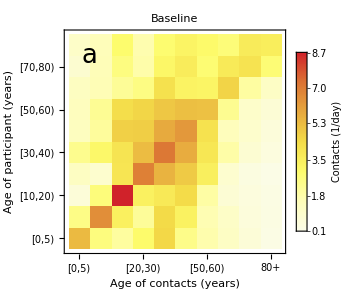

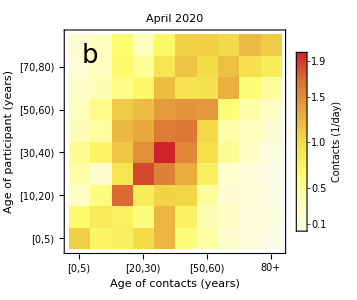

```mathematica
Print[Style["Imported demography PT 10 age groups",18,Blue,"Text"]]
DemographyData10=Flatten[Import["Data//DEMOGRAPHY PT 10.xlsx"]];
DemographyData10//MatrixForm

NumAgeGroups = 10;
AgeGroups= Table[k, {k, 1, NumAgeGroups}];
Demography:=Table[Subscript[NN,k]-> DemographyData10⟦k⟧,{k,AgeGroups}];
AgeLabel={"[0,5) y.o.","[5,10) y.o.","[10,20) y.o.","[20,30) y.o.","[30,40) y.o.","[40,50) y.o.", "[50,60) y.o.","[60,70) y.o.","[70,80) y.o.","80+ y.o."};

AgeLabelShort={"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

Print[Style["Imported demography PT 17 age groups",18,Blue,"Text"]];
DemographyData17=Flatten[Import["Data//DEMOGRAPHY PT 17.xlsx"]];
DemographyData17//MatrixForm

Print[Style["Imported demography NL 10 age groups",18,Blue,"Text"]]
DemographyData10NL=Flatten[Import["Data//DEMOGRAPHY NL 10.xlsx"]];
DemographyData10NL//MatrixForm

Print[Style["Imported demography NL 17 age groups",18,Blue,"Text"]];
DemographyData17NL=Flatten[Import["Data//DEMOGRAPHY NL 17.xlsx"]];
DemographyData17NL//MatrixForm

Print[Style["Imported contact matrix PT before the lockdown 16 age groups",18,Blue,"Text"]];
ContactDataPTBefore16=Import["Data//CONTACT MATRIX PT BEFORE 16.xlsx"]⟦1⟧;
ContactDataPTBefore16//MatrixForm

Print[Style["Imported school contact matrix PT before the lockdown 16 age groups",18,Blue,"Text"]];
SchoolContactDataPTBefore16=Import["Data//SCHOOL CONTACT MATRIX PT BEFORE 16.xlsx"]⟦1⟧;
SchoolContactDataPTBefore16//MatrixForm

(*Print[Style["Function transforming a contact matrix with 16 age groups into a matrix with 10 age groups",18,Blue,"Text"]];*)
MatrixTransform16to10[ContactMatrix16_]:=Block[{ContactMatrix10},
ContactMatrix10=ContactMatrix16;
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10]; 

ContactMatrix10=Join[ContactMatrix10,{ContactMatrix10⟦16,All⟧}];
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10=Join[ContactMatrix10,List/@(ContactMatrix10⟦All,16⟧ DemographyData17⟦17⟧/DemographyData17⟦16⟧),2] ;
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10=Transpose[{ContactMatrix10⟦All,1⟧,ContactMatrix10⟦All,2⟧,ContactMatrix10⟦All,3⟧+ContactMatrix10⟦All,4⟧,ContactMatrix10⟦All,5⟧+ContactMatrix10⟦All,6⟧,ContactMatrix10⟦All,7⟧+ContactMatrix10⟦All,8⟧,ContactMatrix10⟦All,9⟧+ContactMatrix10⟦All,10⟧,ContactMatrix10⟦All,11⟧+ContactMatrix10⟦All,12⟧,ContactMatrix10⟦All,13⟧+ContactMatrix10⟦All,14⟧,ContactMatrix10⟦All,15⟧+ContactMatrix10⟦All,16⟧,ContactMatrix10⟦All,17⟧}];
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10={ContactMatrix10⟦1,All⟧,ContactMatrix10⟦2,All⟧,(ContactMatrix10⟦3,All⟧ DemographyData17⟦3⟧+ContactMatrix10⟦4,All⟧ DemographyData17⟦4⟧)/(DemographyData17⟦3⟧+DemographyData17⟦4⟧),(ContactMatrix10⟦5,All⟧ DemographyData17⟦5⟧+ContactMatrix10⟦6,All⟧ DemographyData17⟦6⟧)/(DemographyData17⟦5⟧+DemographyData17⟦6⟧),
(ContactMatrix10⟦7,All⟧ DemographyData17⟦7⟧+ContactMatrix10⟦8,All⟧ DemographyData17⟦8⟧)/(DemographyData17⟦7⟧+DemographyData17⟦8⟧),
(ContactMatrix10⟦9,All⟧ DemographyData17⟦9⟧+ContactMatrix10⟦10,All⟧ DemographyData17⟦10⟧)/(DemographyData17⟦9⟧+DemographyData17⟦10⟧),
(ContactMatrix10⟦11,All⟧ DemographyData17⟦11⟧+ContactMatrix10⟦12,All⟧ DemographyData17⟦12⟧)/(DemographyData17⟦11⟧+DemographyData17⟦12⟧),
(ContactMatrix10⟦13,All⟧ DemographyData17⟦13⟧+ContactMatrix10⟦14,All⟧ DemographyData17⟦14⟧)/(DemographyData17⟦13⟧+DemographyData17⟦14⟧),
(ContactMatrix10⟦15,All⟧ DemographyData17⟦15⟧+ContactMatrix10⟦16,All⟧ DemographyData17⟦16⟧)/(DemographyData17⟦15⟧+DemographyData17⟦16⟧),ContactMatrix10⟦17,All⟧};

Dimensions[ContactMatrix10];
ContactMatrix10//MatrixForm;
ContactMatrix10
];

Print[Style["Contact matrix PT before the lockdown 10 age groups",18,Green,"Text"]];
ContactDataPTBefore10=MatrixTransform16to10[ContactDataPTBefore16];
ContactDataPTBefore10//MatrixForm
Export["Data//CONTACT MATRIX PT BEFORE 10.csv",ContactDataPTBefore10,"Table"]

Print[Style["School contact matrix PT before the lockdown 10 age groups",18,Green,"Text"]];
SchoolContactDataPTBefore10=MatrixTransform16to10[SchoolContactDataPTBefore16];
SchoolContactDataPTBefore10//MatrixForm
Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 10.csv",SchoolContactDataPTBefore10,"Table"]

Print[Style["Imported contact matrix NL before the lockdown 10 age groups",18,Blue,"Text"]];
ContactDataNLBefore10=Import["Data//CONTACT MATRIX NL BEFORE 10.csv"];
ContactDataNLBefore10//MatrixForm

Print[Style["Imported contact matrix NL after the lockdown 10 age groups",18,Blue,"Text"]];
ContactDataNLAfter10=Import["Data//CONTACT MATRIX NL AFTER 10.csv"];
ContactDataNLAfter10//MatrixForm

Print[Style["Ratio of contacts after and before the lockdown NL 10 age groups",18,Blue,"Text"]];
RatioContactsAfterAndBeforeNL10=ContactDataNLAfter10/ContactDataNLBefore10;
RatioContactsAfterAndBeforeNL10//MatrixForm

Print[Style["Contact matrix PT after the lockdown 10 age groups",18,Green,"Text"]];
ContactDataPTAfter10=ContactDataPTBefore10 RatioContactsAfterAndBeforeNL10 ;
ContactDataPTAfter10//MatrixForm
Export["Data//CONTACT MATRIX PT AFTER 10.csv",ContactDataPTAfter10,"Table"]

ImSize=300;

Print[Style["Plotting contact matrices",18,Blue,"Text"]]

PlotContactMatrix[matrix_,label_,panel_]:=Show[MatrixPlot[matrix,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{label}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},(*Mesh->True,*)Frame->True,PlotTheme-> "Web",FrameTicks->{{{1,"[0,5)",0},{2,"[5,10)",0},{3,"[10,20)",0},{4,"[20,30)",0},{5,"[30,40)",0},{6,"[40,50)",0},{7,"[50,60)",0},{8,"[60,70)",0},{9,"[70,80)",0},{10,"80+",0}},{{1,Rotate["[0,5)",Pi/2],0},{2,Rotate["[5,10)",Pi/2],0},{3,Rotate["[10,20)",Pi/2],0},{4,Rotate["[20,30)",Pi/2],0},{5,Rotate["[30,40)",Pi/2],0},{6,Rotate["[40,50)",Pi/2],0},{7,Rotate["[50,60)",Pi/2],0},{8,Rotate["[60,70)",Pi/2],0},{9,Rotate["[70,80)",Pi/2],0},{10,Rotate["80+",Pi/2],0}}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14(*,Opacity[1],"Helvetica"*)]],{After,Top}]],Graphics[Text[StyleForm[panel,FontSize->26],{10*0.1,10*0.9}]]]

FigContactMatrixBefore=PlotContactMatrix[ContactDataPTBefore10,"Baseline","a"]
FigContactMatrixAfter=PlotContactMatrix[ContactDataPTAfter10,"April 2020","b"]

format={".pdf",".eps"};
FigNames={"SFig1A","SFig1B"};
Figures={FigContactMatrixBefore,FigContactMatrixAfter};
(*Table[Export[StringJoin["Figures//",FigNames⟦j⟧,format⟦i⟧],Figures⟦j⟧],{i,1,Length[format]},{j,1,Length[FigNames]}]*)
```

## Comparison of contact matrices for PT and NL

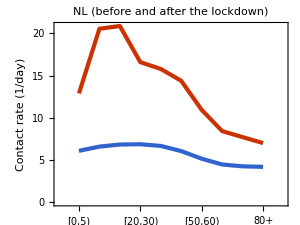

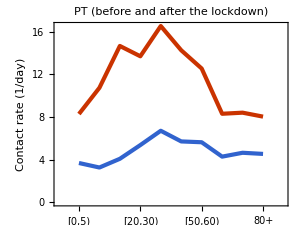

Contact rate before, after and the ratio of the two, PT

{12.1555,5.0685,0.416973}

Contact rate before, after and the ratio of the two, NL

{13.7007,5.79766,0.423164}

```mathematica
CalculateContactsAgeGroups[Matrix10_]:=Table[Total[Matrix10⟦k,All⟧],{k,AgeGroups}];

ContactsAgeGroupsNLBefore=CalculateContactsAgeGroups[ContactDataNLBefore10];
ContactsAgeGroupsPTBefore=CalculateContactsAgeGroups[ContactDataPTBefore10];

ContactsAgeGroupsNLAfter=CalculateContactsAgeGroups[ContactDataNLAfter10];
ContactsAgeGroupsPTAfter=CalculateContactsAgeGroups[ContactDataPTAfter10];

PrintContacts[Before_,After_,Country_]:=ListLinePlot[{Before,After},AspectRatio->0.75,ImageSize->ImSize,PlotRange-> {{0,11},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Contact rate (1/day)",None},{None,None}},PlotRange->All,PlotRangePadding->None,PlotTheme-> "Web",PlotLabel->Style[Row[{Country}],Black,17],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic}]

PrintContacts[ContactsAgeGroupsNLBefore,ContactsAgeGroupsNLAfter,"NL (before and after the lockdown)"]
PrintContacts[ContactsAgeGroupsPTBefore,ContactsAgeGroupsPTAfter,"PT (before and after the lockdown)"]

CalculateAverageContactRate[Demography_,ContactsAgeGroups_]:=Sum[ContactsAgeGroups⟦k⟧ Demography⟦k⟧/Total[Demography],{k,AgeGroups}];

ContactsPTBeforeTotal=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTBefore];
ContactsPTAfterTotal=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTAfter];

ContactsNLBeforeTotal=CalculateAverageContactRate[DemographyData10NL,ContactsAgeGroupsNLBefore];
ContactsNLAfterTotal=CalculateAverageContactRate[DemographyData10NL,ContactsAgeGroupsNLAfter];

Print[Style["Contact rate before, after and the ratio of the two, PT",18,Blue,"Text"]];
{ContactsPTBeforeTotal,ContactsPTAfterTotal,ContactsPTAfterTotal/ContactsPTBeforeTotal}

Print[Style["Contact rate before, after and the ratio of the two, NL",18,Blue,"Text"]];
{ContactsNLBeforeTotal,ContactsNLAfterTotal,ContactsNLAfterTotal/ContactsNLBeforeTotal}
```

## PT contact matrix by Vespignani et al 85 x 85

Imported demography PT 85 age groups

1.02863×10^7

9.554777×10^6

Imported contact matrix PT before the lockdown 85 age groups

Imported school contact matrix PT before the lockdown 85 age groups

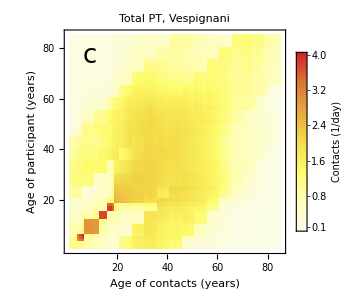

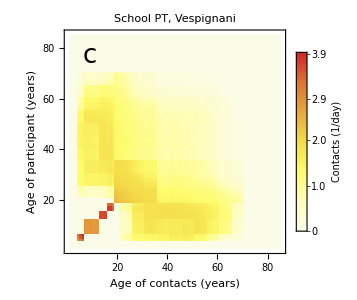

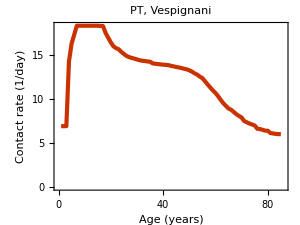

```mathematica
Print[Style["Imported demography PT 85 age groups",18,Blue,"Text"]];
DemographyData85=Import["Data//Portugal_country_level_age_distribution_85.csv"]⟦All,2⟧;
DemographyData85//MatrixForm;

Total[DemographyData10]
Total[DemographyData85]

Print[Style["Imported contact matrix PT before the lockdown 85 age groups",18,Blue,"Text"]];
ContactDataPTBefore85=Import["Data//Portugal_country_level_M_overall_contact_matrix_85.csv"];
ContactDataPTBefore85//MatrixForm;

Print[Style["Imported school contact matrix PT before the lockdown 85 age groups",18,Blue,"Text"]];
SchoolContactDataPTBefore85= 11.41 Import["Data//Portugal_country_level_F_school_setting_85.csv"];
SchoolContactDataPTBefore85//MatrixForm;

Show[MatrixPlot[ContactDataPTBefore85,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{"Total PT, Vespignani"}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},Mesh->None,Frame->True,PlotTheme-> "Web"(*,FrameTicks->{{{1,"[0,5)"},{2,"[5,10)"},{3,"[10,20)"},{4,"[20,30)"},{5,"[30,40)"},{6,"[40,50)"},{7,"[50,60)"},{8,"[60,70)"},{9,"[70,80)"},{10,"80+"}},{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}}}*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14,Opacity[1]]],{After,Top}]],Graphics[Text[StyleForm["c",FontSize->26],{85*0.1,85*0.9}]]]

Show[MatrixPlot[SchoolContactDataPTBefore85,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{"School PT, Vespignani"}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},Mesh->None,Frame->True,PlotTheme-> "Web"(*,FrameTicks->{{{1,"[0,5)"},{2,"[5,10)"},{3,"[10,20)"},{4,"[20,30)"},{5,"[30,40)"},{6,"[40,50)"},{7,"[50,60)"},{8,"[60,70)"},{9,"[70,80)"},{10,"80+"}},{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}}}*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14,Opacity[1]]],{After,Top}]],Graphics[Text[StyleForm["c",FontSize->26],{85*0.1,85*0.9}]]]

CalculateContactsAgeGroups2=Table[Total[ContactDataPTBefore85⟦k,All⟧],{k,85}];

ListLinePlot[CalculateContactsAgeGroups2,AspectRatio->0.75,ImageSize->ImSize,PlotRange-> {{0,86},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotTheme-> "Web",FrameLabel-> {{"Contact rate (1/day)",None},{"Age (years)",None}},PlotRange->All,PlotRangePadding->None,PlotLabel->Style[Row[{"PT, Vespignani"}],Black,17],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}]
```

## PT contact matrix by Vespignani et al 10 x 10

Data//DEMOGRAPHY PT 86 V.csv

Data//DEMOGRAPHY PT 10 V.csv

Data//CONTACT MATRIX PT BEFORE 86 V.csv

Contact matrix PT before the lockdown 10 age groups Vespignani

(2.54599 | 1.79557 | 0.597741 | 1.58124 | 1.88037 | 0.976327 | 0.37358 | 0.285957 | 0.228345 | 0.158905
1.66701 | 7.00627 | 3.50534 | 1.12103 | 2.02307 | 1.60218 | 0.570874 | 0.30405 | 0.228345 | 0.158905
0.277096 | 1.7503 | 7.92572 | 1.77052 | 2.18543 | 2.00318 | 1.28105 | 0.368414 | 0.243935 | 0.163057
0.591971 | 0.45205 | 1.42984 | 3.86932 | 2.78535 | 2.57546 | 1.94659 | 0.985505 | 0.3383 | 0.187177
0.60404 | 0.699997 | 1.5144 | 2.39 | 2.96178 | 2.49673 | 1.84907 | 1.00521 | 0.525449 | 0.191036
0.341158 | 0.603025 | 1.50995 | 2.40387 | 2.71588 | 2.50389 | 1.81707 | 0.969533 | 0.549773 | 0.408321
0.155063 | 0.255228 | 1.14703 | 2.15821 | 2.38921 | 2.15841 | 1.8196 | 1.19895 | 0.620215 | 0.333587
0.145453 | 0.166582 | 0.404239 | 1.33899 | 1.59168 | 1.41131 | 1.46925 | 1.21007 | 1.00448 | 0.523675
0.144409 | 0.155546 | 0.332783 | 0.571482 | 1.03446 | 0.995011 | 0.944983 | 1.24889 | 1.10364 | 0.869867
0.144409 | 0.155546 | 0.319654 | 0.454369 | 0.540446 | 1.06194 | 0.730372 | 0.935621 | 1.24999 | 0.979677)

Data//CONTACT MATRIX PT BEFORE 10 V.csv

Contact matrix PT after the lockdown 10 age groups Vespignani

(0.66379 | 0.896331 | 0.549225 | 1.09857 | 0.813849 | 0.443574 | 0.173255 | 0.108539 | 0.0911416 | 0.0511191
0.836786 | 0.788293 | 1.35811 | 0.648049 | 0.913181 | 0.626547 | 0.271936 | 0.134109 | 0.0969225 | 0.0658767
0.253713 | 0.672021 | 1.31878 | 0.775213 | 1.11967 | 0.760043 | 0.555326 | 0.187472 | 0.129283 | 0.070255
0.399902 | 0.252689 | 0.610879 | 1.25055 | 1.20687 | 1.04786 | 0.802298 | 0.477108 | 0.184186 | 0.0627074
0.252438 | 0.303404 | 0.751813 | 1.02836 | 1.04986 | 0.948123 | 0.833753 | 0.50376 | 0.321531 | 0.0852948
0.160378 | 0.242657 | 0.594879 | 1.04078 | 1.10517 | 0.81283 | 0.818297 | 0.552429 | 0.38795 | 0.268786
0.0703978 | 0.118356 | 0.488453 | 0.895535 | 1.09218 | 0.919597 | 0.76732 | 0.672245 | 0.498172 | 0.247894
0.0546569 | 0.0723389 | 0.204364 | 0.660016 | 0.817845 | 0.769406 | 0.833138 | 0.533537 | 0.656613 | 0.430808
0.0518747 | 0.0590889 | 0.159288 | 0.287988 | 0.589993 | 0.610699 | 0.697817 | 0.74212 | 0.481003 | 0.520121
0.044131 | 0.0609153 | 0.131289 | 0.148709 | 0.23738 | 0.641748 | 0.526675 | 0.738514 | 0.788875 | 0.571973)

Data//CONTACT MATRIX PT AFTER 10 V.csv

School contact matrix PT before the lockdown 10 age groups Vespignani

Data//SCHOOL CONTACT MATRIX PT BEFORE 86 V.csv

(1.94146 | 1.29028 | 0. | 0.0253809 | 0.0592522 | 0.0914605 | 0.0256729 | 0.00205149 | 0. | 0.
1.1979 | 6.37547 | 2.70494 | 0.104617 | 0.287726 | 0.286894 | 0.22302 | 0.0201486 | 0. | 0.
0. | 1.35064 | 6.80854 | 0.924351 | 0.487979 | 0.356924 | 0.222397 | 0.0313604 | 0. | 0.
0.00950192 | 0.0421863 | 0.746488 | 1.42563 | 0.246543 | 0.0608675 | 0.0355611 | 0.0120944 | 0. | 0.
0.0190338 | 0.0995556 | 0.338147 | 0.211549 | 0.0497481 | 0.0220656 | 0.0135955 | 0.00271788 | 0. | 0.
0.0319591 | 0.107981 | 0.269041 | 0.0568123 | 0.0240024 | 0.0167527 | 0.0104474 | 0.0014702 | 0. | 0.
0.0106561 | 0.0997085 | 0.199129 | 0.0394271 | 0.0175669 | 0.01241 | 0.00829965 | 0.00111587 | 0. | 0.
0.00104349 | 0.011039 | 0.0344099 | 0.0164324 | 0.00430357 | 0.00214012 | 0.00136745 | 0.00023978 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Data//SCHOOL CONTACT MATRIX PT BEFORE 10 V.csv

Plotting contact matrices

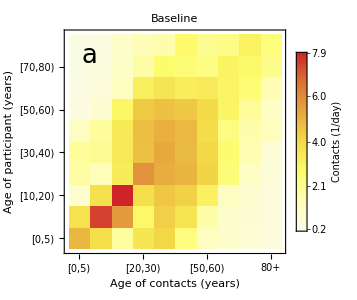
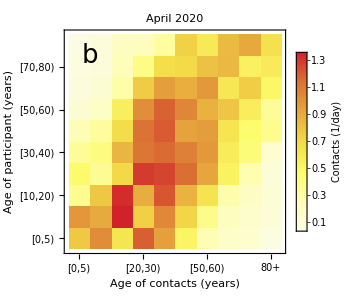
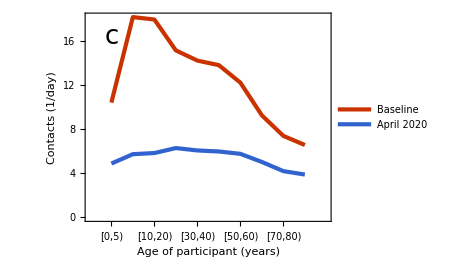
-Graphics- | -Graphics-
-Graphics- |

{12.6132,5.50154,0.436173}

```mathematica
ListTransform86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
(*Demography10Test= Join[Partition[Range[0,85],5]⟦1;;2⟧,Partition[Range[0,85],10]⟦2;;⟧,{Range[0,85]⟦81;;⟧}];*)

(* https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
DemographyData86=Append[DemographyData85,316442];
DemographyData10Vespignani=ListTransform86to10[DemographyData86];

Export["Data//DEMOGRAPHY PT 86 V.csv",DemographyData86,"Table"]

Export["Data//DEMOGRAPHY PT 10 V.csv",DemographyData10Vespignani,"Table"]

(* Join[{v},m]//MatrixForm - join a row v to matrix m
Join[List/@v,m,2]//MatrixForm - join a column v to matrix m *)

ContactDataPTBefore86x85=Join[ContactDataPTBefore85,{ContactDataPTBefore85⟦85⟧}];
(*ContactDataPTBefore86x85//Dimensions
ContactDataPTBefore86x85//MatrixForm*)
ContactDataPTBefore86x86=Join[ContactDataPTBefore86x85,List/@(ContactDataPTBefore86x85⟦All,85⟧ DemographyData86⟦86⟧/DemographyData86⟦85⟧), 2];
(*ContactDataPTBefore86x86//Dimensions
ContactDataPTBefore86x86//MatrixForm*)
Export["Data//CONTACT MATRIX PT BEFORE 86 V.csv",ContactDataPTBefore86x86,"Table"]


Print[Style["Contact matrix PT before the lockdown 10 age groups Vespignani",18,Red,"Text"]];
ContactDataPTBefore10Vespignani=ListTransform86to10[ Transpose[ListTransform86to10[Transpose[ContactDataPTBefore86x86]]] DemographyData86]/DemographyData10Vespignani;
ContactDataPTBefore10Vespignani//MatrixForm
Export["Data//CONTACT MATRIX PT BEFORE 10 V.csv",ContactDataPTBefore10Vespignani,"Table"]

Print[Style["Contact matrix PT after the lockdown 10 age groups Vespignani",18,Red,"Text"]];
ContactDataPTAfter10Vespignani=ContactDataPTBefore10Vespignani RatioContactsAfterAndBeforeNL10 ;
ContactDataPTAfter10Vespignani//MatrixForm
Export["Data//CONTACT MATRIX PT AFTER 10 V.csv",ContactDataPTAfter10Vespignani,"Table"]

Print[Style["School contact matrix PT before the lockdown 10 age groups Vespignani",18,Red,"Text"]];

SchoolContactDataPTBefore86x85=Join[SchoolContactDataPTBefore85,{SchoolContactDataPTBefore85⟦85⟧}];
(*SchoolContactDataPTBefore86x85//Dimensions
SchoolContactDataPTBefore86x85//MatrixForm*)
SchoolContactDataPTBefore86x86=Join[SchoolContactDataPTBefore86x85,List/@(SchoolContactDataPTBefore86x85⟦All,85⟧ DemographyData86⟦86⟧/DemographyData86⟦85⟧), 2];
(*ContactDataPTBefore86x86//Dimensions
ContactDataPTBefore86x86//MatrixForm*)
Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 86 V.csv",SchoolContactDataPTBefore86x86,"Table"]

SchoolContactDataPTBefore10Vespignani=ListTransform86to10[ Transpose[ListTransform86to10[Transpose[SchoolContactDataPTBefore86x86]]] DemographyData86]/DemographyData10Vespignani;
SchoolContactDataPTBefore10Vespignani//MatrixForm
Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 10 V.csv",SchoolContactDataPTBefore10Vespignani,"Table"]

Print[Style["Plotting contact matrices",18,Blue,"Text"]]

FigContactMatrixBeforeV=PlotContactMatrix[ContactDataPTBefore10Vespignani,"Baseline","a"];
FigContactMatrixAfterV=PlotContactMatrix[ContactDataPTAfter10Vespignani,"April 2020","b"];
FigSchoolContactMatrixBeforeV=PlotContactMatrix[SchoolContactDataPTBefore10Vespignani,"Baseline: school contacts","b"];

format={".pdf",".eps"};
FigNames={"SFig1A","SFig1B","SFig1C"};
Figures={FigContactMatrixBeforeV,FigSchoolContactMatrixBeforeV,FigContactMatrixAfterV};
(*Table[Export[StringJoin["Figures//",FigNames⟦j⟧,format⟦i⟧],Figures⟦j⟧],{i,1,Length[format]},{j,1,Length[FigNames]}]*)

BeforeAfterLegends=Style[#,Black]&/@{"Baseline","April 2020"};

PrintContactsPaper[Before_,After_]:=Show[ListLinePlot[{Before,After},AspectRatio->0.75,ImageSize->350,PlotRange-> {{0,11},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Contacts (1/day)",None},{"Age of participant (years)",None}},PlotRange->All,PlotRangePadding->None,PlotTheme-> "Web"(*,PlotLabel->Style[Row[{Country}],Black,17]*),FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic},PlotLegends->Placed[BeforeAfterLegends,Scaled[{{1,1}, {1,1 }}]],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,20},{Automatic,30}}],Graphics[Text[StyleForm["c",FontSize->26],{10*0.1,Max[Before]*0.9}]]]


ContactsAgeGroupsPTBeforeV=CalculateContactsAgeGroups[ContactDataPTBefore10Vespignani];
ContactsAgeGroupsPTAfterV=CalculateContactsAgeGroups[ContactDataPTAfter10Vespignani];

FigBeforeAfter=PrintContactsPaper[ContactsAgeGroupsPTBeforeV,ContactsAgeGroupsPTAfterV];

(*SFig2=Grid[{{FigContactMatrixBeforeV,FigSchoolContactMatrixBeforeV}}]
Table[Export[StringJoin["Figures//SFig2",format⟦i⟧],SFig2],{i,1,Length[format]}]

SFig3=Grid[{{FigBeforeAfter,FigContactMatrixAfterV}}]
Table[Export[StringJoin["Figures//SFig3",format⟦i⟧],SFig3],{i,1,Length[format]}]*)

SFig2=Grid[{{FigContactMatrixBeforeV,FigContactMatrixAfterV},{FigBeforeAfter,SpanFromLeft}}]
(*Table[Export[StringJoin["Figures//SFig2",format⟦i⟧],SFig2],{i,1,Length[format]}]*)

(*ContactsPTBeforeTotalV=CalculateAverageContactRate[DemographyData10Vespignani,ContactsAgeGroupsPTBeforeV];
ContactsPTAfterTotalV=CalculateAverageContactRate[DemographyData10Vespignani,ContactsAgeGroupsPTAfterV];
{ContactsPTBeforeTotalV,ContactsPTAfterTotalV,ContactsPTAfterTotalV/ContactsPTBeforeTotalV}*)

ContactsPTBeforeTotalV=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTBeforeV];
ContactsPTAfterTotalV=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTAfterV];
{ContactsPTBeforeTotalV,ContactsPTAfterTotalV,ContactsPTAfterTotalV/ContactsPTBeforeTotalV}
```

## Serological data

```mathematica
(* 
Grupo etário (anos)
1-9 
10-19 
20-39
40-59
≥60 
*)
```

```mathematica
TotalSamples5={404,377,377,479,664};

Total[TotalSamples5]

PositivePecentage5={2.9,2.2,2.9,3.2,2.9}/100;

Round[TotalSamples5 PositivePecentage5]

SamplesTransform5to10[Variable5_]:=Round[{Variable5⟦1⟧ DemographyData17⟦1⟧/(DemographyData17⟦1⟧+DemographyData17⟦2⟧),Variable5⟦1⟧ DemographyData17⟦2⟧/(DemographyData17⟦1⟧+DemographyData17⟦2⟧),Variable5⟦2⟧,Variable5⟦3⟧ DemographyData10⟦4⟧/(DemographyData10⟦4⟧+DemographyData10⟦5⟧),Variable5⟦3⟧ DemographyData10⟦5⟧/(DemographyData10⟦4⟧+DemographyData10⟦5⟧),Variable5⟦4⟧ DemographyData10⟦6⟧/(DemographyData10⟦6⟧+DemographyData10⟦7⟧),Variable5⟦4⟧ DemographyData10⟦7⟧/(DemographyData10⟦6⟧+DemographyData10⟦7⟧),Variable5⟦5⟧ DemographyData10⟦8⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧),Variable5⟦5⟧ DemographyData10⟦9⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧),Variable5⟦5⟧ DemographyData10⟦10⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧)}];

SamplesTransform5to10[TotalSamples5]

SamplesTransform5to10[TotalSamples5 PositivePecentage5]
```

2301

{12,8,11,15,19}

{196,208,377,176,201,247,232,293,220,151}

{6,6,8,5,6,8,7,8,6,4}

Imported seroprevalence data: SeroData.csv

{{AgeClass,Positive,SampleSize,Day,Frac,Lower,Upper},{[1,10),12,404,93,0.029703,0.0163378,0.0497561},{[10,20),8,377,93,0.0212202,0.010082,0.0396386},{[20,40),11,377,93,0.0291777,0.015599,0.049927},{[40,60),15,479,93,0.0313152,0.0184186,0.0498409},{[60,Inf),19,664,93,0.0286145,0.0179025,0.0434167}}

Header of the imported data

{AgeClass,Positive,SampleSize,Day,Frac,Lower,Upper}

Seroprevalence ISN

([1,10) | 12 | 404 | 93 | 0.029703 | 0.013 | 0.062
[10,20) | 8 | 377 | 93 | 0.0212202 | 0.008 | 0.055
[20,40) | 11 | 377 | 93 | 0.0291777 | 0.012 | 0.07
[40,60) | 15 | 479 | 93 | 0.0313152 | 0.015 | 0.067
[60,Inf) | 19 | 664 | 93 | 0.0286145 | 0.015 | 0.053)

Imported simulated seroprevalence: SeroViolin.csv

Header of the imported data

{[1,10),[10,20),[20,40),[40,60),[60,Inf)}

Median and quantiles, simulated seroprevalence

{{1.7692,2.20121,4.61275,4.2328,2.87343},{0.977295,1.24158,3.47027,3.18265,2.20559},{2.90614,3.55196,5.91196,5.42557,3.65459}}

(1.7692 | 0.977295 | 2.90614
2.20121 | 1.24158 | 3.55196
4.61275 | 3.47027 | 5.91196
4.2328 | 3.18265 | 5.42557
2.87343 | 2.20559 | 3.65459)

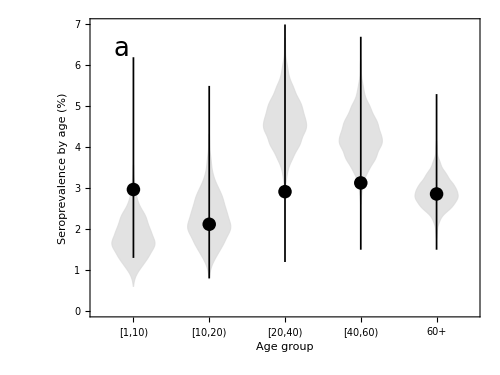

```mathematica
Needs["ErrorBarPlots`"]
Print[Style["Imported seroprevalence data: SeroData.csv",18,Blue,"Text"]]
SeroData=Import["Data//SeroData_Joao.csv"]
Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderSeroData=SeroData⟦1⟧
SeroData=Drop[SeroData,1];
SeroData//MatrixForm;

SeroDataISN=SeroData;
(* Confidence intervals from ISN COVID19 Relatorio 06/08/2020 *)

SeroDataISN⟦1,6⟧=1.3/100;
SeroDataISN⟦1,7⟧=6.2/100;

SeroDataISN⟦2,6⟧=0.8/100;
SeroDataISN⟦2,7⟧=5.5/100;

SeroDataISN⟦3,6⟧=1.2/100;
SeroDataISN⟦3,7⟧=7.0/100;

SeroDataISN⟦4,6⟧=1.5/100;
SeroDataISN⟦4,7⟧=6.7/100;

SeroDataISN⟦5,6⟧=1.5/100;
SeroDataISN⟦5,7⟧=5.3/100;

Print[Style["Seroprevalence ISN",18,Blue,"Text"]]

SeroDataISN//MatrixForm

SeroData=SeroDataISN;

Needs["ErrorBarPlots`"]

Print[Style["Imported simulated seroprevalence: SeroViolin.csv",18,Blue,"Text"]]
SeroViolin=Import["Data//SeroViolin_Joao.csv"];
Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderSeroViolin=SeroViolin⟦1⟧
SeroViolin=Drop[SeroViolin,1];

Print[Style["Median and quantiles, simulated seroprevalence",18,Blue,"Text"]]
{100 Median[SeroViolin],100 Quantile[SeroViolin,0.025],100 Quantile[SeroViolin,0.975]}
{100 Median[SeroViolin],100 Quantile[SeroViolin,0.025],100 Quantile[SeroViolin,0.975]}//Transpose//MatrixForm

mediansero=Median[SeroViolin];

fig4a=Show[DistributionChart[Table[SeroViolin⟦All,i⟧ 100,{i,1,Length[HeaderSeroViolin]}],ChartStyle->Directive[LightGray,Opacity[0.75]],AspectRatio->0.75,ImageSize->500,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Seroprevalence by age (%)",None},{"Age group",None}},PlotRange->{All,{0,7}},PlotRangePadding->None,PlotTheme-> "Web"],ErrorListPlot[Table[{{i,SeroData⟦i,5⟧ 100},ErrorBar[{SeroData⟦i,6⟧ 100-SeroData⟦i,5⟧100,SeroData⟦i,7⟧100-SeroData⟦i,5⟧100}]},{i,Length[SeroData]}], PlotRange->All,PlotStyle->{Black,Thickness[0.0025]},PlotTheme-> "Web"],Graphics[Text[StyleForm["a",FontSize->26],Scaled[{0.08,0.9}]]],FrameTicks->{{{1,Rotate["[1,10)",0]},{2,Rotate["[10,20)",0]},{3,Rotate["[20,40)",0]},{4,Rotate["[40,60)",0]},{5,Rotate["60+",0]}},Automatic},Frame-> {{True,False},{True,False}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{44, Automatic}, {65, 7.5}}]

(*Table[Export[StringJoin["Figures//Fig4a",format⟦i⟧],fig4a],{i,1,Length[format]}];*)
```

## Important dates

```mathematica
Print[Style["Important dates",18,Blue,"Text"]]
Print[Style["Date of starting simulations",18,Blue,"Text"]]
DateObject[{2020, 02, 25}]
t0=0

Print[Style["Date of the start of the pandemic",18,Blue,"Text"]]
DateObject[{2020, 02, 26}]

Print[Style["Date of starting vaccination",18,Blue,"Text"]]
(*tstartvac=255;*)
DateObject[{2020, 12, 27}]
tstartvac=Differences[{DateObject[{2020, 02, 26}],DateObject[{2020, 12, 27}]}]⟦1,1⟧+1

Print[Style["Date of ending vaccination",18,Blue,"Text"]]
(*DateObject[{2021, 07, 31}]*)
DateObject[{2021, 12, 31}]
tendvac=Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,12,31}](*DateObject[{2021, 07, 31}]*)}]⟦1,1⟧+1+10(*days extra*) (* DateObject[{2021, 12, 31}] *)

Print[Style["Last hospitalization date",18,Blue,"Text"]]

tenddata=Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 (* Jan 15 but starting with t=1 *)
```

Important dates

Date of starting simulations

Tue 25 Feb 2020

0

Date of the start of the pandemic

Wed 26 Feb 2020

Date of starting vaccination

Sun 27 Dec 2020

306

Date of ending vaccination

Fri 31 Dec 2021

685

Last hospitalization date

326

## Vaccination plan

```mathematica
Categories={{"Profissionais de saúde","Profissionais e residentes em ERPI e RNCCI","50+ com insuficiência cardíaca","50+ com doença coronária","50+ com insuficiência renal","50+ com DPOC ou doença respiratória crónica","Profissionais das forças de segurança e da Proteção Civil"},{"65+ com ou sem patologias","Entre os 50 e os 64 anos com diabetes","Entre os 50 e os 64 anos com neoplasia maligna ativa","Entre os 50 e os 64 anos com insuficiência hepática","Entre os 50 e os 64 anos com doença renal crónica","Entre os 50 e os 64 anos com obesidade","Entre os 50 e os 64 anos com hipertensão arterial"},{"Restante população"}};

Fase1=1;
Fase2=2;
Fase3=3;

Print[Style["Categories: phase 1",18,Blue,"Text"]];
Categories⟦Fase1⟧
Print[Style["Categories: phase 2",18,Blue,"Text"]];
Categories⟦Fase2⟧
Print[Style["Categories: phase 3",18,Blue,"Text"]];
Categories⟦Fase3⟧

NumberOfCategories={Length[Categories⟦Fase1⟧],Length[Categories⟦Fase2⟧],Length[Categories⟦Fase3⟧]};

Print[Style["Number of categories: phase 1",18,Blue,"Text"]];
NumberOfCategories⟦Fase1⟧
Print[Style["Number of categories: phase 2",18,Blue,"Text"]];
NumberOfCategories⟦Fase2⟧
Print[Style["Number of categories: phase 3",18,Blue,"Text"]];
NumberOfCategories⟦Fase3⟧

PersonsToVaccinate={{199708,148119,207571,169265,8201,128597,75900},{1873349,222864,114246,93004,4222,392959,632547},{6529448}};

Print[Style["Persons to vaccinate per category: phase 1",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase1⟧
Print[Style["Persons to vaccinate per category: phase 2",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase2⟧
Print[Style["Persons to vaccinate per category: phase 3",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase3⟧


Print[Style["Total: phase 1",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]
Print[Style["Total: phase 2",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase2⟧]
Print[Style["Total: phase 3",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase3⟧]
Print[Style["Total: phase 1 and phase 2",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]+Total[PersonsToVaccinate⟦Fase2⟧]
Print[Style["Total: all phases",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]+Total[PersonsToVaccinate⟦Fase2⟧]+Total[PersonsToVaccinate⟦Fase3⟧]

Print[Style["Start and end vaccination dates: all phases",18,Blue,"Text"]];
StartAndEndVaccinationDates={{
{DateObject[{2020, 12, 27}],DateObject[{2021, 02, 28}]},
{DateObject[{2021, 01, 01}],DateObject[{2021, 02, 28}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]}},

{{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]}},

{DateObject[{2021, 08, 01}],DateObject[{2021, 12, 31}]}};

Print[Style["Start and end vaccination dates: phase 1",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase1⟧
Print[Style["Start and end vaccination dates: phase 2",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase2⟧
Print[Style["Start and end vaccination dates: phase 3",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase3⟧

Print[Style["Duration of vaccination per category (days): phase 1",18,Blue,"Text"]];
Duration1=Flatten[Map[Differences,StartAndEndVaccinationDates⟦Fase1⟧]]⟦All,1⟧
Print[Style["Duration of vaccination per category (days): phase 2",18,Blue,"Text"]];
Duration2=Flatten[Map[Differences,StartAndEndVaccinationDates⟦Fase2⟧]]⟦All,1⟧
Print[Style["Duration of vaccination per category (days): phase 3",18,Blue,"Text"]];
Duration3=Differences[StartAndEndVaccinationDates⟦Fase3⟧]⟦All,1⟧

Print[Style["Duration of vaccination per category (days): all phases",18,Blue,"Text"]];
DurationVaccination={Duration1,Duration2,Duration3}

Print[Style["Start vaccination dates: phase 1",18,Blue,"Text"]];
StartVaccinationDates1=Subscript[t, vaccination]+ Prepend[Flatten[Map[Differences,Table[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase1⟧⟦cat,1⟧},{cat,2,Length[StartAndEndVaccinationDates⟦Fase1⟧]}]]]⟦All,1⟧,0]


Print[Style["Start vaccination dates: phase 2",18,Blue,"Text"]];
StartVaccinationDates2=Subscript[t, vaccination]+ Flatten[Map[Differences,Table[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase2⟧⟦cat,1⟧},{cat,1,Length[StartAndEndVaccinationDates⟦Fase2⟧]}]]]⟦All,1⟧


Print[Style["Start vaccination dates: phase 3",18,Blue,"Text"]];
StartVaccinationDates3=Subscript[t, vaccination]+Differences[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase3⟧⟦1⟧}]⟦All,1⟧

Print[Style["Start vaccination dates: all phases",18,Blue,"Text"]];
StartVaccinationDates={StartVaccinationDates1,StartVaccinationDates2,StartVaccinationDates3}

Print[Style["End vaccination dates: all phases",18,Blue,"Text"]];
EndVaccinationDates=StartVaccinationDates+DurationVaccination

Print[Style["Total vaccination rate r = ∑ r_k",18,Blue,"Text"]];
Print[Style["Persons to vaccinate per day for each category and phase",18,Blue,"Text"]];
TotalVacRate=PersonsToVaccinate/DurationVaccination//N
```

Categories: phase 1

{Profissionais de saúde,Profissionais e residentes em ERPI e RNCCI,50+ com insuficiência cardíaca,50+ com doença coronária,50+ com insuficiência renal,50+ com DPOC ou doença respiratória crónica,Profissionais das forças de segurança e da Proteção Civil}

Categories: phase 2

{65+ com ou sem patologias,Entre os 50 e os 64 anos com diabetes,Entre os 50 e os 64 anos com neoplasia maligna ativa,Entre os 50 e os 64 anos com insuficiência hepática,Entre os 50 e os 64 anos com doença renal crónica,Entre os 50 e os 64 anos com obesidade,Entre os 50 e os 64 anos com hipertensão arterial}

Categories: phase 3

{Restante população}

Number of categories: phase 1

7

Number of categories: phase 2

7

Number of categories: phase 3

1

Persons to vaccinate per category: phase 1

{199708,148119,207571,169265,8201,128597,75900}

Persons to vaccinate per category: phase 2

{1873349,222864,114246,93004,4222,392959,632547}

Persons to vaccinate per category: phase 3

{6529448}

Total: phase 1

937361

Total: phase 2

3333191

Total: phase 3

6529448

Total: phase 1 and phase 2

4270552

Total: all phases

10800000

Start and end vaccination dates: all phases

Start and end vaccination dates: phase 1

{{Sun 27 Dec 2020,Sun 28 Feb 2021},{Fri 1 Jan 2021,Sun 28 Feb 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021}}

Start and end vaccination dates: phase 2

{{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021}}

Start and end vaccination dates: phase 3

{Sun 1 Aug 2021,Fri 31 Dec 2021}

Duration of vaccination per category (days): phase 1

{63,58,88,88,88,88,88}

Duration of vaccination per category (days): phase 2

{91,91,91,91,91,91,91}

Duration of vaccination per category (days): phase 3

{152}

Duration of vaccination per category (days): all phases

{{63,58,88,88,88,88,88},{91,91,91,91,91,91,91},{152}}

Start vaccination dates: phase 1

{t_vaccination,5+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination}

Start vaccination dates: phase 2

{125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination}

Start vaccination dates: phase 3

{217+t_vaccination}

Start vaccination dates: all phases

{{t_vaccination,5+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination},{125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination},{217+t_vaccination}}

End vaccination dates: all phases

{{63+t_vaccination,63+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination},{216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination},{369+t_vaccination}}

Total vaccination rate r = ∑ r_k

Persons to vaccinate per day for each category and phase

{{3169.97,2553.78,2358.76,1923.47,93.1932,1461.33,862.5},{20586.3,2449.05,1255.45,1022.02,46.3956,4318.23,6951.07},{42956.9}}

## Vaccination rates

Binary vector of vaccination ages per category
{0-4,5-9,10-19,20-29,30-39,40-49,50-59,60-69,70-79,80+}
Format:1-yes,vaccinate this age group,0-no,do not vaccinate this age group
NB! To vaccinate e.g.60-64 age group,include a correction

```mathematica
Print[Style["Vaccination rates r_k",18,Blue,"Text"]];
Print[Style["Persons to vaccinate per day in each age group",18,Blue,"Text"]];

VacRate[Category_,VaccinationAges_,Correction_,Demography_,TotalVacRate_]:=Block[{PersonsToVaccinate,AgeDistributionVaccination},

Print[Style[Category,18,Red,"Text"]];

(* Persons to vaccinate in different age groups *)

PersonsToVaccinate=VaccinationAges Correction Demography;

(* Age distribution for vaccinations *)

AgeDistributionVaccination=PersonsToVaccinate/Total[PersonsToVaccinate];

TotalVacRate AgeDistributionVaccination
]

R11=VacRate[Categories⟦1,1⟧,{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,1⟧]

R12a=VacRate["Profissionais em ERPI e RNCCI",{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,2⟧ 0.8 (60991+15431)/PersonsToVaccinate⟦Fase1⟧⟦2⟧]

R12b=VacRate["Residentes em ERPI e RNCCI",{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,27500 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),27500 (DemographyData17⟦15⟧+DemographyData17⟦16⟧)/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),82500},TotalVacRate⟦1,2⟧ 0.8 (99234+9493)/PersonsToVaccinate⟦Fase1⟧⟦2⟧]

Print[Style["Profissionais e residentes em ERPI e RNCCI",18,Red,"Text"]];
R12=R12a+R12b

ImportPersonsToVaccinate[column_]:=Reverse[Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧⟦5;;15,column⟧];
PersonsToVaccinate11to10[Vector_]:={0,0,0,0,0,0,Vector⟦1⟧+Vector⟦2⟧,Vector⟦3⟧+Vector⟦4⟧,Vector⟦5⟧+Vector⟦6⟧,Total[Vector⟦7;;11⟧]};

InsuficienciaCardiaca=PersonsToVaccinate11to10[ImportPersonsToVaccinate[5]];
R13=VacRate[Categories⟦1,3⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},InsuficienciaCardiaca,TotalVacRate⟦1,3⟧]
(*Total[InsuficienciaCardiaca] 
PersonsToVaccinate⟦Fase1⟧⟦3⟧*)

DoencaCoronaria=PersonsToVaccinate11to10[ImportPersonsToVaccinate[8]];
R14=VacRate[Categories⟦1,4⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},DoencaCoronaria,TotalVacRate⟦1,4⟧]

(* 65-75: 3361
75+:4840 *)

InsuficienciaRenal={0,0,0,0,0,0,0,3361 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧),3361 DemographyData17⟦15⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧)+4840 DemographyData17⟦16⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧),4840 DemographyData17⟦17⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧)};

R15=VacRate[Categories⟦1,5⟧,{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1},InsuficienciaRenal,TotalVacRate⟦1,5⟧]

DoencaRespiratoriaCronica=PersonsToVaccinate11to10[ImportPersonsToVaccinate[14]];
R16=VacRate[Categories⟦1,6⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},DoencaRespiratoriaCronica,TotalVacRate⟦1,6⟧]

R17=VacRate[Categories⟦1,7⟧,{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,7⟧]

Print[Style["Vector of vaccination rates: phase 1",18,Blue,"Text"]];
VacRatesVector1={R11,R12,R13,R14,R15,R16, R17}

R21=VacRate[Categories⟦2,1⟧,{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1, DemographyData17⟦14⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦2,1⟧]

ImportPersonsToVaccinate50to65[column_]:=Reverse[Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧⟦13;;15,column⟧];
PersonsToVaccinate3to10[Vector_]:={0,0,0,0,0,0,Vector⟦1⟧+Vector⟦2⟧,Vector⟦3⟧,0,0};

Diabetes=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[11]];
R22=VacRate[Categories⟦2,2⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},Diabetes,TotalVacRate⟦2,2⟧]

NeoplasiaMaligna=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[23]];
R23=VacRate[Categories⟦2,3⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},NeoplasiaMaligna,TotalVacRate⟦2,3⟧]

InsuficienciaHepatica=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[29]];
R24=VacRate[Categories⟦2,4⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},InsuficienciaHepatica,TotalVacRate⟦2,4⟧]

DoencaRenalCronica={0,0,0,0,0,0,4222 (DemographyData17⟦11⟧+DemographyData17⟦12⟧)/(DemographyData17⟦11⟧+DemographyData17⟦12⟧+DemographyData17⟦13⟧),4222 DemographyData17⟦13⟧/(DemographyData17⟦11⟧+DemographyData17⟦12⟧+DemographyData17⟦13⟧),0,0};
R25=VacRate[Categories⟦2,5⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},DoencaRenalCronica,TotalVacRate⟦2,5⟧]

Obesidade=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[20]];
R26=VacRate[Categories⟦2,6⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},Obesidade,TotalVacRate⟦2,6⟧]

HipertensaoArterial=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[17]];
R27=VacRate[Categories⟦2,7⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},HipertensaoArterial,TotalVacRate⟦2,7⟧]

Print[Style["Vector of vaccination rates: phase 2",18,Blue,"Text"]];
VacRatesVector2={R21,R22,R23,R24,R25,R26,R27}

Print[Style["Restante população",18,Red,"Text"]];
R31=VacRate[Categories⟦3,1⟧,{0,0,0,1 ,1 ,1 ,1 ,0 ,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦3,1⟧]

(*R31⟦4;;7⟧=R31⟦4;;7⟧ {0.8,0.9,1,0.5}*)

(*R31={0,0,0,0,0,0,0,0,0,0}*)

Print[Style["Vector of vaccination rates: phase 3",18,Blue,"Text"]];
VacRatesVector3={R31}

Print[Style["Vector of vaccination rates: all phases",18,Blue,"Text"]];
VacRatesVector={VacRatesVector1,VacRatesVector2,VacRatesVector3}
```

Vaccination rates r_k

Persons to vaccinate per day in each age group

Profissionais de saúde

{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.}

Profissionais em ERPI e RNCCI

{0.,0.,0.,189.565,217.055,273.43,257.269,116.778,0.,0.}

Residentes em ERPI e RNCCI

{0.,0.,0.,0.,0.,0.,0.,145.987,228.934,1124.76}

Profissionais e residentes em ERPI e RNCCI

{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76}

50+ com insuficiência cardíaca

{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58}

50+ com doença coronária

{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455}

50+ com insuficiência renal

{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501}

50+ com DPOC ou doença respiratória crónica

{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932}

Profissionais das forças de segurança e da Proteção Civil

{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}

Vector of vaccination rates: phase 1

{{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.},{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76},{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58},{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455},{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501},{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932},{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}}

65+ com ou sem patologias

{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54}

Entre os 50 e os 64 anos com diabetes

{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.}

Entre os 50 e os 64 anos com neoplasia maligna ativa

{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.}

Entre os 50 e os 64 anos com insuficiência hepática

{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.}

Entre os 50 e os 64 anos com doença renal crónica

{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.}

Entre os 50 e os 64 anos com obesidade

{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.}

Entre os 50 e os 64 anos com hipertensão arterial

{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}

Vector of vaccination rates: phase 2

{{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54},{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.},{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.},{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.},{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.},{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.},{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}}

Restante população

Restante população

{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}

Vector of vaccination rates: phase 3

{{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}}

Vector of vaccination rates: all phases

{{{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.},{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76},{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58},{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455},{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501},{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932},{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54},{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.},{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.},{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.},{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.},{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.},{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}},{{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}}}

## Age distribution of vaccination categories

The coordinates of Scaled are :
{{Position on graphic in x, Position on graphic in y}, {Part of plot legend that should be at the assigned position on graphic}}
{{0.9, 0.9}, {1, 1}} assigns a location on my graphic 90 % up the graphic and 90 % to the right, and puts the upper right corner of my plot legend at this point
{{0.5, 0.5}, {0.5, 0.5}} puts the middle of my plot legend in the middle of my graphic

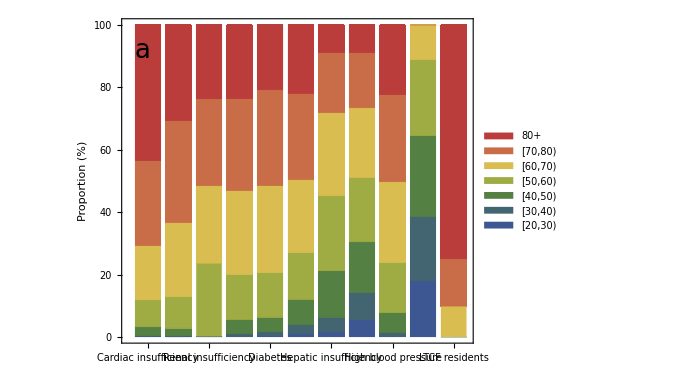
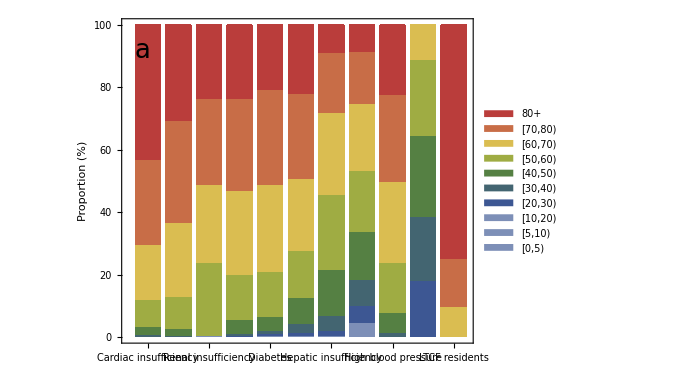

```mathematica
CategoriesAgeDistribution=Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧;
ImportCategoriesAgeDistribution[i_]:=Join[{Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦1⟧+Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦2⟧,Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦3⟧},Total/@Partition[Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦4;;17⟧,2],{Total[Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦18;;22⟧]}];

A11=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];
A12a=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];
(*A12b=Join[{0,0,0,0,0,0,0,DemographyData17⟦14⟧},DemographyData10⟦9;;10⟧];*)

A12b={0,0,0,0,0,0,0,27500 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),27500 (DemographyData17⟦15⟧+DemographyData17⟦16⟧)/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),82500};

A13=ImportCategoriesAgeDistribution[5];
A14=ImportCategoriesAgeDistribution[8];
A15={72 DemographyData17⟦1⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],72 DemographyData17⟦2⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],72 (DemographyData17⟦3⟧+DemographyData17⟦4⟧)/Sum[DemographyData17⟦i⟧,{i,1,5}],72 DemographyData17⟦5⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],0,0,4222 (DemographyData17⟦11⟧+DemographyData17⟦12⟧)/Sum[DemographyData17⟦i⟧,{i,11,13}],4222 DemographyData17⟦13⟧/Sum[DemographyData17⟦i⟧,{i,11,13}]+3361 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧),3361 DemographyData17⟦15⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧)+4840 DemographyData17⟦16⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧),4840 DemographyData17⟦17⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧)};
(*Manuel said that the 20-65 are all in the 50-65 age groups*)
A16=ImportCategoriesAgeDistribution[14];
A17=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];

A22=ImportCategoriesAgeDistribution[11];
A23=ImportCategoriesAgeDistribution[23];
A24=ImportCategoriesAgeDistribution[29];
(* A25 Same disease as A15 so I grouped them *)
A26=ImportCategoriesAgeDistribution[20];
A27=ImportCategoriesAgeDistribution[17];

BarChartFormat[x_]:=100 x/Total[x];

AgeDistributionChartLabel={"Cardiac insufficiency","Coronary heart disease","Renal insufficiency", "COPD","Diabetes","Neoplasm","Hepatic insufficiency","Obesity","High blood pressure","HCW, LTCF staff, FRP","LTCF residents"};

BarChartLegends=Style[#,Black]&/@{"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

ChartStyleColors=Join[{Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]](*ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0]*)},ColorData["DarkRainbow"]/@Rescale[AgeGroups⟦1;;7⟧]];

AspRat=0.75;

PlotBarChart[StartAgeGroup_,colors_]:=Show[BarChart[BarChartFormat/@(#⟦StartAgeGroup;;⟧&/@{A13,A14,A15,A16,A22,A23,A24,A26,A27,A11,A12b}),ChartLayout->"Stacked",ImageSize->500,ChartLabels->{Rotate[Style[#,Black,14],Pi/2]&/@AgeDistributionChartLabel,None},ChartLegends->Placed[BarChartLegends⟦StartAgeGroup;;⟧,(*{After,Top}*){Scaled[ {{1.1, 0.5}, {0.5,0.5 }}]}], PlotTheme->"Web",Joined->False,BarSpacing->0.2,AspectRatio->AspRat,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],ChartStyle->colors,FrameLabel-> {{"Proportion (%)",None},{None,None}},PlotRange->{All,{0,100}},PlotRangePadding->None,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}],Graphics[Text[StyleForm["a",FontSize->26],Scaled[{0.06,0.9}]]]]

{PlotBarChart[4,"DarkRainbow"],fig1A=PlotBarChart[1,ChartStyleColors]}

format={".pdf",".eps"};

(*Table[Export[StringJoin["Figures//Fig1A",format⟦i⟧],fig1A],{i,1,Length[format]}];*)
```

## Vaccination rates as piece-wise functions

```mathematica
Clear[CreatePiecewiseRate,Rates,UnconstrainedRates,OrderIntervals]

CreatePiecewiseRate[Rate_,StartVaccinationDate_,EndVaccinationDate_]:=
Piecewise[{{0,t<0},{0,Subscript[t, start]≤t<StartVaccinationDate},{Rate,StartVaccinationDate≤t≤EndVaccinationDate},{0,t> EndVaccinationDate}}]/.{Subscript[t, vaccination]->tstartvac,Subscript[t, start]-> t0}

UnconstrainedRates=Table[ PiecewiseExpand[Sum[Sum[CreatePiecewiseRate[VacRatesVector⟦Fase⟧⟦Category⟧⟦k⟧,StartVaccinationDates⟦Fase⟧⟦Category⟧,EndVaccinationDates⟦Fase⟧⟦Category⟧],{Category,1,NumberOfCategories⟦Fase⟧}],
{Fase,{Fase1,Fase2,Fase3}}]],{k,AgeGroups}];
Print[Style["Vaccination rates with unordered intervals and without constraints on the number of vaccines",18,Blue,"Text"]]
Rates=UnconstrainedRates

PiecewiseDomains[HoldPattern[Piecewise[cases_,default_]]]:=Module[{dl=Last/@cases},Append[dl,Not[Or@@dl]]]
OrderIntervals=Table[Quiet@Maximize[{t,#},t]&/@PiecewiseDomains[UnconstrainedRates⟦k⟧]//N//Ordering,{k,AgeGroups}];
Table[Rates⟦k⟧⟦1⟧=Table[UnconstrainedRates⟦k⟧⟦1⟧⟦PosInt⟧,{PosInt,OrderIntervals⟦k⟧⟦1;;Length[OrderIntervals⟦k⟧]-1⟧}],{k,AgeGroups}];

Print[Style["Vaccination rates with ordered intervals but without constraints on the number of vaccines",18,Blue,"Text"]];
Rates

Table[Rates⟦k⟧⟦1⟧=Table[{Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦1⟧,Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦2⟧&&Sum[Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦1⟧ (Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦2⟧⟦5⟧-Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦2⟧⟦1⟧),{PosIntSum,1,PosInt-1}]+Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦1⟧ (t-Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦2⟧⟦1⟧)≤(*If[k==3,2/10,1]*)0.9 Subscript[NN, k]/.Demography//Simplify},{PosInt,1,Length[Rates⟦k⟧⟦1⟧]}],{k,AgeGroups}];

Print[Style["Vaccination rates with constraints on the number of vaccines",18,Blue,"Text"]];
Table[Rates⟦k⟧=Subscript[r,k]->Rates⟦k⟧,{k,AgeGroups}]
```

Vaccination rates with unordered intervals and without constraints on the number of vaccines

{Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {155.109, 369<t≤430}, {570.076, 306≤t<311}, {759.64, 311≤t<342}, {914.749, 342≤t≤369}, {8687.68, 523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {177.602, 369<t≤430}, {652.745, 306≤t<311}, {869.8, 311≤t<342}, {1047.4, 342≤t≤369}, {9947.52, 523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {223.73, 369<t≤430}, {822.282, 306≤t<311}, {1095.71, 311≤t<342}, {1319.44, 342≤t≤369}, {12531.2, 523≤t≤675}, {0, True}}],Piecewise[{{773.68, 306≤t<311}, {844.984, 369<t≤430}, {1030.95, 311≤t<342}, {1875.93, 342≤t≤369}, {9518.87, 431≤t≤522}, {11790.5, 523≤t≤675}, {0, True}}],Piecewise[{{0., 523≤t≤675}, {351.186, 306≤t<311}, {613.951, 311≤t<342}, {1429.86, 369<t≤430}, {2043.81, 342≤t≤369}, {12170., 431≤t≤522}, {0, True}}],Piecewise[{{0., 306≤t<311||523≤t≤675}, {228.934, 311≤t<342}, {1811.5, 369<t≤430}, {2040.43, 342≤t≤369}, {8855.03, 431≤t≤522}, {0, True}}],Piecewise[{{0., 306≤t<311||523≤t≤675}, {1124.76, 311≤t<342}, {2056.47, 369<t≤430}, {3181.23, 342≤t≤369}, {6084.54, 431≤t≤522}, {0, True}}]}

Vaccination rates with ordered intervals but without constraints on the number of vaccines

{Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{570.076, 306≤t<311}, {759.64, 311≤t<342}, {914.749, 342≤t≤369}, {155.109, 369<t≤430}, {0., 431≤t≤522}, {8687.68, 523≤t≤675}, {0, True}}],Piecewise[{{652.745, 306≤t<311}, {869.8, 311≤t<342}, {1047.4, 342≤t≤369}, {177.602, 369<t≤430}, {0., 431≤t≤522}, {9947.52, 523≤t≤675}, {0, True}}],Piecewise[{{822.282, 306≤t<311}, {1095.71, 311≤t<342}, {1319.44, 342≤t≤369}, {223.73, 369<t≤430}, {0., 431≤t≤522}, {12531.2, 523≤t≤675}, {0, True}}],Piecewise[{{773.68, 306≤t<311}, {1030.95, 311≤t<342}, {1875.93, 342≤t≤369}, {844.984, 369<t≤430}, {9518.87, 431≤t≤522}, {11790.5, 523≤t≤675}, {0, True}}],Piecewise[{{351.186, 306≤t<311}, {613.951, 311≤t<342}, {2043.81, 342≤t≤369}, {1429.86, 369<t≤430}, {12170., 431≤t≤522}, {0., 523≤t≤675}, {0, True}}],Piecewise[{{228.934, 311≤t<342}, {2040.43, 342≤t≤369}, {1811.5, 369<t≤430}, {8855.03, 431≤t≤522}, {0., 306≤t<311||523≤t≤675}, {0, True}}],Piecewise[{{1124.76, 311≤t<342}, {3181.23, 342≤t≤369}, {2056.47, 369<t≤430}, {6084.54, 431≤t≤522}, {0., 306≤t<311||523≤t≤675}, {0, True}}]}

Vaccination rates with constraints on the number of vaccines

{r_1→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_2→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_3→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_4→Piecewise[{{570.076, 306.≤t<311.}, {759.64, 311.≤t<342.}, {914.749, 342.≤t≤369.}, {155.109, 369.<t≤430.}, {0., 431≤t≤522}, {8687.68, 523.≤t≤629.163}, {0, True}}],r_5→Piecewise[{{652.745, 306.≤t<311.}, {869.8, 311.≤t<342.}, {1047.4, 342.≤t≤369.}, {177.602, 369.<t≤430.}, {0., 431≤t≤522}, {9947.52, 523.≤t≤629.163}, {0, True}}],r_6→Piecewise[{{822.282, 306.≤t<311.}, {1095.71, 311.≤t<342.}, {1319.44, 342.≤t≤369.}, {223.73, 369.<t≤430.}, {0., 431≤t≤522}, {12531.2, 523.≤t≤629.163}, {0, True}}],r_7→Piecewise[{{773.68, 306.≤t<311.}, {1030.95, 311.≤t<342.}, {1875.93, 342.≤t≤369.}, {844.984, 369.<t≤430.}, {9518.87, 431.≤t≤522.}, {11790.5, 523.≤t≤550.961}, {0, True}}],r_8→Piecewise[{{351.186, 306.≤t<311.}, {613.951, 311.≤t<342.}, {2043.81, 342.≤t≤369.}, {1429.86, 369.<t≤430.}, {12170., 431.≤t≤513.233}, {0, True}}],r_9→Piecewise[{{228.934, 311.≤t<342.}, {2040.43, 342.≤t≤369.}, {1811.5, 369.<t≤430.}, {8855.03, 431.≤t≤510.404}, {0, True}}],r_10→Piecewise[{{1124.76, 311.≤t<342.}, {3181.23, 342.≤t≤369.}, {2056.47, 369.<t≤430.}, {6084.54, 431.≤t≤489.441}, {0, True}}]}

## Plotting vaccination rates

Vaccination rate (persons per day) for each age group

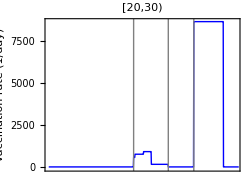
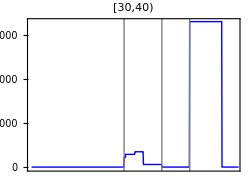
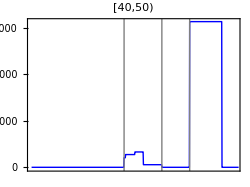
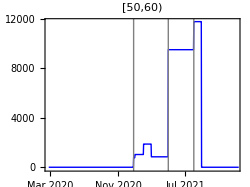
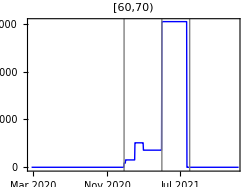
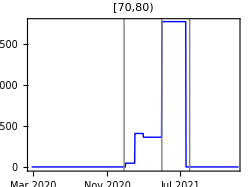
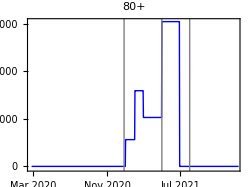
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

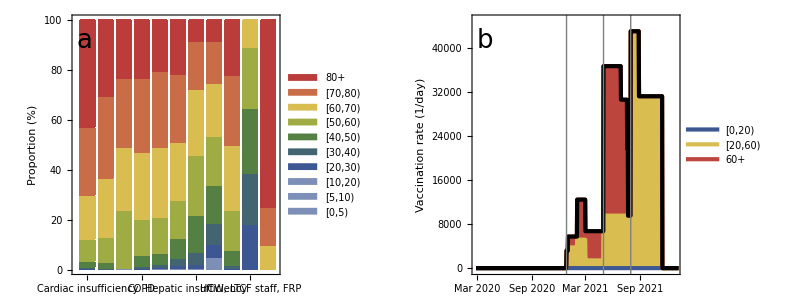

```mathematica
Subscript[t, start]=t0;
Subscript[t, end]=tendvac;

AspRat=0.75; ImSize=350;

FigNames={"A","B","C","D","E","F","G","H","I","J"};
PanelLetter[AgeGroup_]:=Graphics[Text[StyleForm[FigNames⟦AgeGroup⟧,FontSize->26],Scaled[{0.9,0.9}]]];

UniqueStartVaccinationDatesAll=DeleteDuplicates[Join[StartAndEndVaccinationDates⟦1⟧⟦All,1⟧,StartAndEndVaccinationDates⟦2⟧⟦All,1⟧,{StartAndEndVaccinationDates⟦3⟧⟦1⟧}]];

UniqueStartVaccinationDates=UniqueStartVaccinationDatesAll⟦1⟧+UniqueStartVaccinationDatesAll⟦4⟧+UniqueStartVaccinationDatesAll⟦5⟧;

UniqueStartVaccinationDays=DeleteDuplicates[Flatten[StartVaccinationDates]]/.Subscript[t, vaccination]->tstartvac;

VaccinationLines:=Table[DateListPlot[{{UniqueStartVaccinationDates⟦i⟧,0},{UniqueStartVaccinationDates⟦i⟧,10000}},PlotStyle->{Dashed,Gray},DateTicksFormat->{"MonthShort","/","YearShort"}],{i,1,Length[UniqueStartVaccinationDates]}];

Print[Style["Vaccination rate (persons per day) for each age group",24,Blue,"Text"]];

tickValues=DateRange[{2020,3,1},{2022,1,1},{4,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

SFig4=Table[Show[DateListPlot[Table[Rates⟦k,2⟧,{t,Subscript[t, start],Subscript[t, end]}],"February 25, 2020",PlotRange->{{"February 25, 2020","January 01, 2022"},{-75,All}},ImageSize->250,PlotRangePadding->None,
PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,14],Frame-> {{True,False},{True,False}},FrameTicks->{{Automatic,None},{If[k≥ 7,ticks,None],None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)FrameLabel-> {{If[k==4||k==7,"Vaccination rate (1/day)",None],None},{None,None}},Prolog->Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],Filling->None,PlotStyle->{Blue,Thick},PlotLabel->Style[Row[{AgeLabelShort⟦k⟧}],Black,14],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{If[k==4||k== 7,65,42], Automatic}, {Automatic, Automatic}}](*,Graphics[Text[StyleForm[FigNames⟦k⟧,FontSize->26],Scaled[{0.9,0.9}]]]*)],{k,Range[4,10]}];
SFig4all=Grid[{SFig4⟦1;;3⟧,SFig4⟦4;;7⟧}]

(*Table[Export[StringJoin["Figures//SFig3",format⟦i⟧],SFig4all],{i,1,Length[format]}];*) 

VaccinationRatesPlot=Table[Table[Rates⟦k,2⟧,{t,Subscript[t, start],Subscript[t, end]}],{k,AgeGroups}];
VaccinationRatesLegends=Style[#,Black]&/@{"[0,20)","[20,60)","60+"};
lineColors=Part[(ColorData["DarkRainbow"]/@Rescale[{1,2,3,4,5,6,7,8,9,10}]),{1,7,9}];

(*lineColors=ColorData["DarkRainbow"]/@Rescale[{1,2,3}];*)
lineWidths={Thickness[0.01],Thickness[0.01],Thickness[0.01]};

ListLinePlot[{Total[VaccinationRatesPlot⟦1;;3⟧],Total[VaccinationRatesPlot⟦1;;7⟧],Total[VaccinationRatesPlot⟦1;;10⟧]},PlotRange->All,ImageSize->ImSize,PlotLegends->VaccinationRatesLegends,Filling->{3-> {2},2-> {1},1-> Axis},PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameLabel-> {{"Vaccination rate\n(1/day)",None},{"Days",None}},PlotStyle->Transpose[{lineColors,lineWidths}],AxesOrigin->{0,0},PlotRangePadding->None];

tickValues=DateRange[{2020,3,1},{2022,1,1},{2,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

fig1B=Show[DateListPlot[{Total[VaccinationRatesPlot⟦1;;3⟧],Total[VaccinationRatesPlot⟦1;;7⟧],Total[VaccinationRatesPlot⟦1;;10⟧]},"February 25, 2020",PlotRange->{{"February 25, 2020","January 01, 2022"},{-250,45000}},ImageSize->500,PlotLegends->Placed[VaccinationRatesLegends,Scaled[{{0.1, 0.7}, {0,1 }}]],Filling->{3-> {{2},lineColors⟦3⟧},2-> {{1},lineColors⟦2⟧},1-> Axis},PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)FrameLabel-> {{"Vaccination rate (1/day)",None},{None,None}},Prolog->Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotStyle->lineColors(*Transpose[{lineColors,lineWidths}]*),AxesOrigin->{"February 25, 2020",0},PlotRangePadding->None,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{80, Automatic}, {160, Automatic}}],DateListPlot[Total[VaccinationRatesPlot⟦1;;10⟧],"February 25, 2020",PlotStyle->{Black},PlotTheme->"Web"],Graphics[Text[StyleForm["b",FontSize->26],Scaled[{0.06,0.9}]]]];

(*Table[Export[StringJoin["Figures//Fig1B",format⟦i⟧],fig1B],{i,1,Length[format]}];*)

DateListPlot[Table[Total[VaccinationRatesPlot⟦1;;k⟧],{k,AgeGroups}],"February 25, 2020",DateTicksFormat->{"MonthShort","/","YearShort"},PlotRange->All,ImageSize->500,PlotLegends->(Style[#,Black,17]&/@AgeLabel)(*,Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]*),Filling->Table[If[k≤ 9,(k+1)-> {k}],{k,AgeGroups}],PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameLabel-> {{"Vaccination rate (1/day)",None},{None,None}},PlotStyle->"CMYKColors",AxesOrigin->{"February 25, 2020",0},PlotRangePadding->None];

(*fig1=Grid[{{fig1A},{fig1B}}]*)
fig1=Grid[{{fig1A,fig1B}}]

Table[Export[StringJoin["Figures//Fig4",format⟦i⟧],fig1],{i,1,Length[format]}];
```

## Importing hospitalization data and parameter estimates

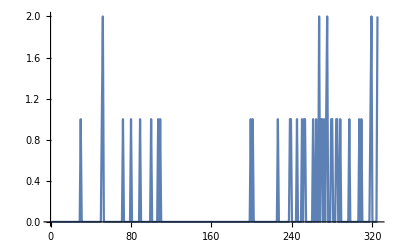
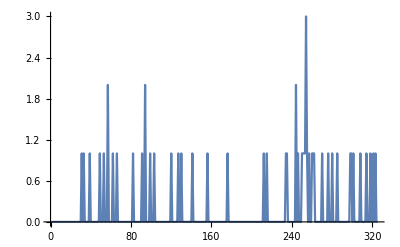
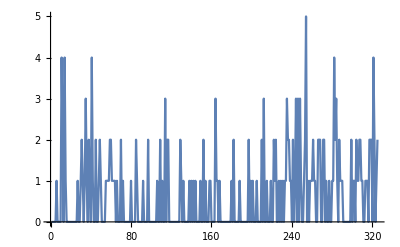
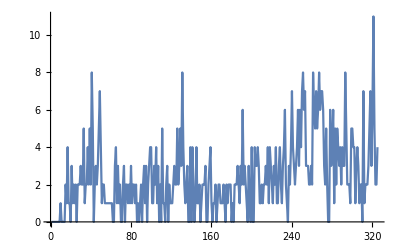
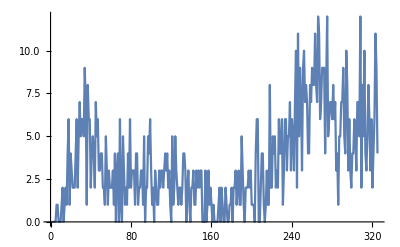
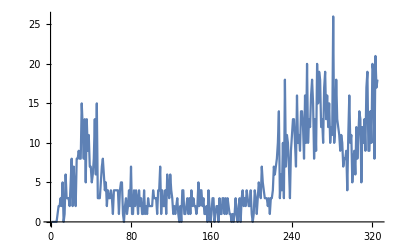
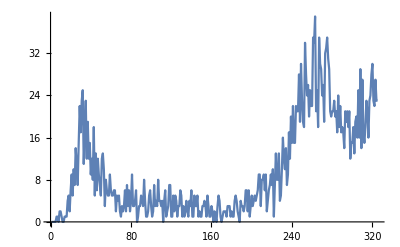
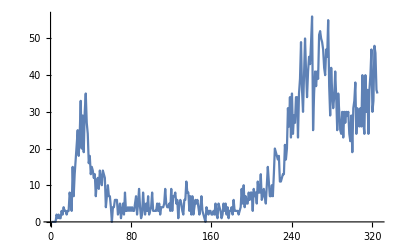

28482

```mathematica
HospitalisationsData=Import["Data//hospitalisations_selected PT 15 Jan 2021 3.csv"];
HospitalisationsData=Drop[HospitalisationsData,1];
Total[Total[HospitalisationsData]];
Dimensions[HospitalisationsData];
TableForm[HospitalisationsData];

Table[ListLinePlot[{HospitalisationsData⟦All,k⟧},PlotRange-> All],{k,AgeGroups}]

Total[Total[HospitalisationsData]]
```

```mathematica
(*Transpose[Insert[Transpose[a],column,2]]*)

HospitalisationsData=Import["Data//hospitalisations_selected PT 15 Jan 2021 3.csv"](*⟦1;;255,All⟧*);
HospitalisationsData=Drop[HospitalisationsData,1];
Dimensions[HospitalisationsData];
TableForm[HospitalisationsData];

ContactRates:=
Flatten[Table[{Subscript[c,{k,l}]->ContactDataPTBefore10Vespignani⟦k,l⟧,Subscript[d,{k,l}]->ContactDataPTAfter10Vespignani⟦k,l⟧(*,Subscript[s,{k,l}]->SchoolContactDataPTBefore10Vespignani⟦k,l⟧*)},{k,1,NumAgeGroups},{l,1,NumAgeGroups}]];

Print[Style["Imported estimated parameters",18,Blue,"Text"]]
(*EstimatesData=Import["Data//fit_19012021_PT.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_187days.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days_2.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days_corrected_prior_omegaV_beta_std_02_constant_alpha_gamma_sero_classes.csv"];*)
(*EstimatesData=Import["Data//tempU4.csv"];*)

(*EstimatesData=Import["Data//daily_short_run.csv"];*)
EstimatesData=Import["Data//fullU4_daily_Joao.csv"];

(*Pos=Dimensions[EstimatesData]⟦2⟧;

EstimatesData=Transpose[Insert[Transpose[EstimatesData],Table[alpha,{i,1,Dimensions[EstimatesData]⟦1⟧}],Pos+1]];
EstimatesData=Transpose[Insert[Transpose[EstimatesData],Table[gamma,{i,1,Dimensions[EstimatesData]⟦1⟧}],Pos+2]];*)

Print[Style["Dimensions of the imported data",18,Blue,"Text"]]
Dimensions[EstimatesData]

Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderParameters=EstimatesData⟦1⟧

EstimatesData=Drop[EstimatesData,1];

(*DischargeRate:=δ->1/5;*)

(*https://bmcmedicine.biomedcentral.com/articles/10.1186/s12916-020-01726-3*)

ProbTransm[sample_]:=ϵ->EstimatesData⟦sample,1⟧;
zeta[sample_]:=ζ-> EstimatesData⟦sample,2⟧;

(* hosp_classes=c(1,2,3,4,5,6,7,8,9,10) *)
(* susc_classes=c(1,1,1,2,2,2,2,3,3,3) *)

nu[sample_]:=Table[Subscript[ν,k]->EstimatesData⟦sample,2+k⟧,{k,1,10}];

Inoculum[sample_]:=Flatten[Table[{Subscript[S0,k]-> 1-EstimatesData⟦sample,13⟧,Subscript[EE0,k]-> 0.5 EstimatesData⟦sample,13⟧,Subscript[II0,k]-> 0.5 EstimatesData⟦sample,13⟧,Subscript[R0,k]-> 0,Subscript[H0,k]-> 0},{k,AgeGroups}]];

Susceptibility[sample_]:=Flatten[Join[Table[Subscript[β,k]->EstimatesData⟦sample,14⟧ ,{k,1,3}],Table[Subscript[β,k]->EstimatesData⟦sample,15⟧ ,{k,4,7}],Table[Subscript[β,k]->EstimatesData⟦sample,16⟧ ,{k,8,10}]]];

rOverDisp[sample_]:=EstimatesData⟦sample,17⟧;

LogFunction[sample_]:={Subscript[x, 0]-> EstimatesData⟦sample,20⟧,Subscript[K, 0]-> EstimatesData⟦sample,21⟧,Subscript[x, 1]-> EstimatesData⟦sample,22⟧,Subscript[K, 1]-> EstimatesData⟦sample,23⟧,Subscript[x, 2]-> EstimatesData⟦sample,24⟧,Subscript[K, 2]-> EstimatesData⟦sample,25⟧,Subscript[x, 3]-> EstimatesData⟦sample,26⟧,Subscript[K, 3]-> EstimatesData⟦sample,27⟧,Subscript[x, 4]-> EstimatesData⟦sample,28⟧,Subscript[K, 4]-> EstimatesData⟦sample,29⟧};

RelaxationFraction[sample_]:={Subscript[u, 1]-> EstimatesData⟦sample,30⟧,Subscript[u, 2]-> EstimatesData⟦sample,31⟧,Subscript[u, 3]-> EstimatesData⟦sample,32⟧,Subscript[u, 4]-> EstimatesData⟦sample,33⟧} ;

LatRate[sample_]:=α->EstimatesData⟦sample,18⟧;
RecRate[sample_]:=γ->EstimatesData⟦sample,19⟧;

Parameters[sample_]:=
Flatten[{(*DischargeRate,*)ContactRates,Demography,ProbTransm[sample],zeta[sample],nu[sample],Inoculum[sample],Susceptibility[sample],LogFunction[sample],RelaxationFraction[sample],LatRate[sample],RecRate[sample]}];

(*VaccineEfficacy[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]:={Subscript[ω, 1]->x1,Subscript[ω, 2]->x2,Subscript[ω, 3]->x3,Subscript[ω, 4]->x4,Subscript[ω, 5]->x5,Subscript[ω, 6]->x6,Subscript[ω, 7]->x7,Subscript[ω, 8]->x8,Subscript[ω, 9]->x9,Subscript[ω, 10]->x10};

VacEffHigh=VaccineEfficacy[0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95];
VacEffLow=VaccineEfficacy[0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5];*)

Ef1:=Subscript[ω, 1]-> 0.94
Ef2:=(Solve[0.94==Subscript[ω, 1]+(1–Subscript[ω, 1]) Subscript[ω, 2],Subscript[ω, 2]]/.Ef1)⟦1,1⟧
Ef3:=(Solve[0.98==Subscript[ω, 1]+(1-Subscript[ω, 1]) Subscript[ω, 2] + (1-Subscript[ω, 1]) (1-Subscript[ω, 2]) Subscript[ω, 3],Subscript[ω, 3]]/.{Ef1,Ef2})⟦1,1⟧

{Ef1,Ef2,Ef3}
```

Imported estimated parameters

Dimensions of the imported data

{2001,33}

Header of the imported data

{epsilon,zeta,nu_short[1],nu_short[2],nu_short[3],nu_short[4],nu_short[5],nu_short[6],nu_short[7],nu_short[8],nu_short[9],nu_short[10],inoculum,beta_short[1],beta_short[2],beta_short[3],r,alpha,gamma,x0,k0,x1,k1,x2,k2,x3,k3,x4,k4,u1,u2,u3,u4}

{ω_1→0.94,ω_2→0.,ω_3→0.666667}

## Parameters vector

```mathematica
ParametersMAP=Parameters[200];

NumSamples=Dimensions[EstimatesData]⟦1⟧;

ParametersMAPNoVaccination=Join[ParametersMAP,Table[Subscript[r,k]-> 0,{k,AgeGroups}],{Subscript[ω, 1]->0,Subscript[ω, 2]->0,Subscript[ω, 3]->0}];
ParametersMAPVaccination=Join[ParametersMAP,Rates,{Ef1,Ef2,Ef3}];

ParametersNoVaccination[sample_]:=Join[Parameters[sample],Table[Subscript[r,k]-> 0,{k,AgeGroups}],{Subscript[ω, 1]->0,Subscript[ω, 2]->0,Subscript[ω, 3]->0}];
ParametersVaccination[sample_]:=Join[Parameters[sample],Rates,{Ef1,Ef2,Ef3}];
```

## Plotting parameter estimates

{{Probability of transmission per contact, ϵ,5.27901,4.41028,6.42444},{Reduction in probability of
transmission per contact, (1-ζ),0.752311,0.633031,0.87473},{Initial number of infected persons, θ,1258.,818.768,1899.49},{Susceptibility of [0,20) y.o. relative to 60+ y.o., β_([0, 20)),0.483416,0.309177,0.687058},{Susceptibility of [20,60) y.o. relative to 60+ y.o., β_([20, 60)),0.971615,0.875444,0.998666},{Overdispersion parameter, r,55.6371,40.2178,80.6598},{t_0 (days),28.3318,27.0459,29.3207},{K_0 (1/day),0.890255,0.369727,3.29852},{t_1 (days),63.4394,60.6155,66.3353},{K_1 (1/day),1.33325,0.396819,4.64938},{t_2 (days),179.238,176.679,182.136},{K_2 (1/day),1.04634,0.28995,3.8361},{t_3 (days),260.653,257.572,263.94},{K_3 (1/day),0.643029,0.265004,3.32574},{t_4 (days),297.352,294.29,300.463},{K_4 (1/day),0.94917,0.280681,3.94408},{u_1,0.2085,0.182182,0.236039},{u_2,0.413161,0.369492,0.455872},{u_3,0.2341,0.189428,0.284781},{u_4,0.465172,0.391362,0.554641},{Latent period (days), 1/α,2.89229,2.17165,3.75828},{Infectious period (days), 1/γ,3.64633,2.98867,4.38462}}

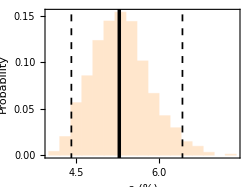
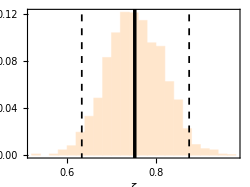
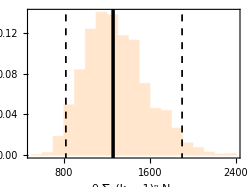
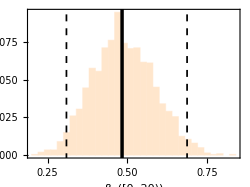
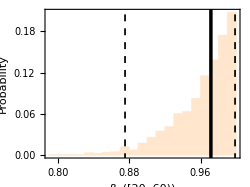
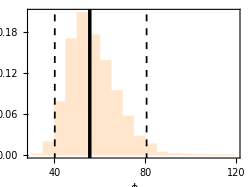
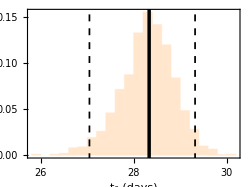
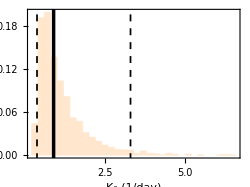
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
AspRat=0.75; ImSize=400;

HistPlot[vals_,xlab_,panel_,panelindex_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->250,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,14],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},PlotTheme->"Web",FrameLabel-> {{If[panelindex==1||panelindex==5||panelindex==9||panelindex==13||panelindex==17||panelindex==21,"Probability",None],None},{xlab,None}},ChartStyle->LightOrange,FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{If[panelindex==1||panelindex==5||panelindex==9||panelindex==13||panelindex==17||panelindex==21,52.5,52.5], Automatic}, {Automatic, Automatic}}],Graphics[{Thickness[0.01],Black,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}](*,Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.9,0.9}]]]*)]

(*ImagePadding->{{If[panelindex==1||panelindex==5||panelindex==9||panelindex==13||panelindex==17,60,60], Automatic}, {Automatic, 0}}*)

(*InfiniteLine[{StartVaccinationDates⟦i⟧,0},{0,1}]*)

vals={EstimatesData⟦All,1⟧ 100,EstimatesData⟦All,2⟧,EstimatesData⟦All,13⟧ Total[DemographyData10],EstimatesData⟦All,14⟧,EstimatesData⟦All,15⟧,EstimatesData⟦All,17⟧,EstimatesData⟦All,20⟧,EstimatesData⟦All,21⟧,EstimatesData⟦All,22⟧,EstimatesData⟦All,23⟧,EstimatesData⟦All,24⟧,EstimatesData⟦All,25⟧,EstimatesData⟦All,26⟧,EstimatesData⟦All,27⟧,EstimatesData⟦All,28⟧,EstimatesData⟦All,29⟧,EstimatesData⟦All,30⟧,EstimatesData⟦All,31⟧,EstimatesData⟦All,32⟧,EstimatesData⟦All,33⟧,1/EstimatesData⟦All,18⟧,1/EstimatesData⟦All,19⟧};

xlabshort={"ϵ (%)","ζ","θ ∑_(k = 1)^n N_k","β_([0, 20))",
"β_([20, 60))","ϕ","t_0 (days)","K_0 (1/day)","t_1 (days)","K_1 (1/day)","t_2 (days)","K_2 (1/day)","t_3 (days)","K_3 (1/day)","t_4 (days)","K_4 (1/day)","u_1","u_2","u_3","u_4","1/α (days)","1/γ (days)"};

xlab={"Probability of transmission per contact, ϵ","Reduction in probability of\ntransmission per contact, (1-ζ)","Initial number of infected persons, θ","Susceptibility of [0,20) y.o. relative to 60+ y.o., β_([0, 20))",
"Susceptibility of [20,60) y.o. relative to 60+ y.o., β_([20, 60))","Overdispersion parameter, r","t_0 (days)","K_0 (1/day)","t_1 (days)","K_1 (1/day)","t_2 (days)","K_2 (1/day)","t_3 (days)","K_3 (1/day)","t_4 (days)","K_4 (1/day)","u_1","u_2","u_3","u_4","Latent period (days), 1/α","Infectious period (days), 1/γ"};

(*"Midpoint value of the logistic function (days), t_1","Logistic growth rate (1/day), K_1","Proportion of contacts during relaxation, u"*)

FigNames={"A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R", "S","T","U","V"};

Table[{xlab⟦i⟧,Median[vals⟦i⟧],Quantile[vals⟦i⟧,0.025],Quantile[vals⟦i⟧,0.975]},{i,1,Length[vals]}]

fig=Table[HistPlot[vals⟦i⟧,xlabshort⟦i⟧,FigNames⟦i⟧,i],{i,1,Length[vals]}];

SFig4=Grid[{fig⟦1;;4⟧,fig⟦5;;8⟧,fig⟦9;;12⟧,fig⟦13;;16⟧,fig⟦17;;20⟧,fig⟦21;;22⟧}]

(*Table[Export[StringJoin["Figures//SFig2",format⟦i⟧],SFig4],{i,1,Length[format]}]*)
```

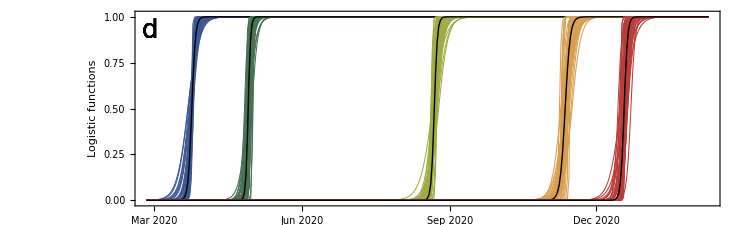
-Graphics- | -Graphics-
-Graphics- | 
-Graphics- |

```mathematica
(* PlotLogisticTransition[midpointindex_,slopeindex_,tend_,ylabel_]:=Show[Plot[Table[(1/(1+Exp[-KK (t-xx)]))/.{xx-> EstimatesData⟦sample,midpointindex⟧,KK->EstimatesData⟦sample,slopeindex⟧},{sample,1,NumSamples,25}],{t,0,tend},AxesOrigin->{0,0},PlotTheme->"Web",PlotRange->{{0,tend},{-0.01,1.01}},PlotStyle->{Gray,Thickness[0.001]},AspectRatio->0.2,ImageSize->1000,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{ylabel,None},{"t (days)",None}}],Plot[(1/(1+Exp[-KK (t-xx)]))/.{xx-> Median[EstimatesData⟦All,midpointindex⟧],KK->Median[EstimatesData⟦All,slopeindex⟧]},{t,0,tend},PlotStyle->{Red,Thick},PlotTheme->"Web",PlotRange->All],Graphics[{Thickness[0.001],Black,Dashed,Line[{{Median[EstimatesData⟦All,midpointindex⟧],0},{Median[EstimatesData⟦All,midpointindex⟧],1}}]}],Graphics[{Thickness[0.001],Black,Dashed,Line[{{0,0.5},{tend,0.5}}]}]]
(*Graphics[Text[StyleForm["t_1",FontSize->17],{31,0.05}]],Graphics[Text[StyleForm["K_1",FontSize->17],{34,0.7}]]*)

Show[PlotLogisticTransition[20,21,350,"Contribution"],PlotLogisticTransition[22,23,350,"Contribution"],PlotLogisticTransition[24,25,350,"Contribution"],PlotLogisticTransition[26,27,350,"Contribution"],PlotLogisticTransition[28,29,350,"Contribution"]]; *)


tickValues=DateRange[{2020,3,1},{2022,1,1},{1,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;
lineColors=ColorData["DarkRainbow"]/@Rescale[{1,2,3,4,5}];

(* plot about 50 samples *)

PlotLogisticTransition[midpointindex_,slopeindex_,color_]:=Show[Join[Table[DateListPlot[Table[(1/(1+Exp[-KK (t-xx)]))/.{xx-> EstimatesData⟦sample,midpointindex⟧,KK->EstimatesData⟦sample,slopeindex⟧},{t,Subscript[t, start],350}],"February 25, 2020",AxesOrigin->{"February 25, 2020",0},PlotTheme->"Web",PlotRange->{{"February 25, 2020",Automatic},{-0.01,1.01}},PlotStyle->{color,Thickness[0.001]},AspectRatio->0.3,ImageSize->750,Frame-> {{True,False},{True,False}},FrameLabel-> {{"Logistic functions",None},{None,None}},FrameTicks->{{Automatic,None},{ticks,None}},FrameStyle->Directive[Black,17],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic, Automatic}, {Automatic, 40}}],{sample,1,NumSamples,40} ],
{DateListPlot[Table[(1/(1+Exp[-KK (t-xx)]))/.{xx-> Median[EstimatesData⟦All,midpointindex⟧],KK->Median[EstimatesData⟦All,slopeindex⟧]},{t,Subscript[t, start],350}],"February 25, 2020",PlotStyle->{Black,Thick},PlotTheme->"Web",PlotRange->All](*,
Graphics[{Thickness[0.001],Black,Dashed,Line[{{Median[EstimatesData⟦All,midpointindex⟧],0},{Median[EstimatesData⟦All,midpointindex⟧],1}}]}],Graphics[{Thickness[0.001],Black,Dashed,Line[{{0,0.5},{tend,0.5}}]}]*)}],Graphics[Text[StyleForm["d",FontSize->26],Scaled[{0.025,0.9}]]]]
(*Graphics[Text[StyleForm["t_1",FontSize->17],{31,0.05}]],Graphics[Text[StyleForm["K_1",FontSize->17],{34,0.7}]]*)

fig6=Show[PlotLogisticTransition[20,21,lineColors⟦1⟧],PlotLogisticTransition[22,23,lineColors⟦2⟧],PlotLogisticTransition[24,25,lineColors⟦3⟧],PlotLogisticTransition[26,27,lineColors⟦4⟧],PlotLogisticTransition[28,29,lineColors⟦5⟧]];

fig9=Grid[{{FigContactMatrixBeforeV,FigContactMatrixAfterV},{FigBeforeAfter,SpanFromLeft},{fig6,SpanFromLeft}}]

 (* Table[Export[StringJoin["Figures//Fig9",format⟦i⟧],fig9],{i,1,Length[format]}] *)
```

## Plotting probabilities of hospitalization

{{[0,5),0.119014,0.0673469,0.225735},{[5,10),0.102348,0.0559479,0.206271},{[10,20),0.165867,0.100604,0.304569},{[20,30),0.296249,0.210498,0.432817},{[30,40),0.404927,0.290369,0.583292},{[40,50),0.546202,0.388367,0.792462},{[50,60),1.01486,0.721882,1.44678},{[60,70),2.12567,1.49935,3.02624},{[70,80),4.623,3.26146,6.71228},{80+,14.2433,9.91362,21.2284}}

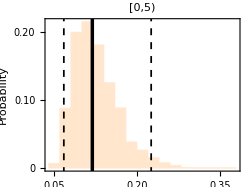
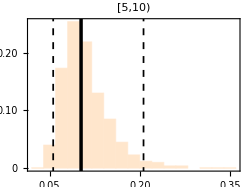
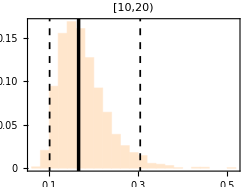
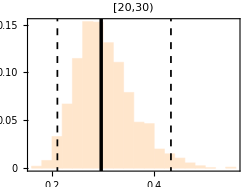
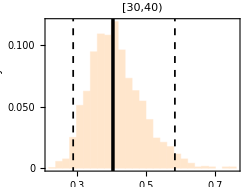
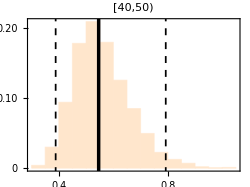
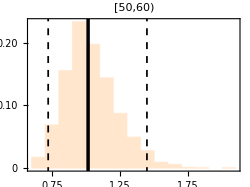
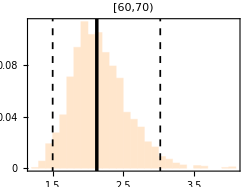
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
HistPlotLabel[vals_,xlab_,label_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->400,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability",None},{xlab,None}},ChartStyle->LightGray,PlotLabel->Style[Row[{label}],Black,14],PlotTheme->"Web",FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}],Graphics[{Thickness[0.01],Red,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}]]

HistPlotLabelPanel[vals_,xlab_,label_,panel_,panelindex_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->250,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,14],FrameLabel-> {{If[panelindex==1||panelindex==5||panelindex==9,"Probability",None],None},{If[panelindex≥ 9,xlab,None],None}},ChartStyle->LightOrange,PlotLabel->Style[Row[{label}],Black,14],PlotTheme->"Web",FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{If[panelindex==1||panelindex==5||panelindex==9||panelindex==13||panelindex==17,60,60], Automatic}, {Automatic, Automatic}}],Graphics[{Thickness[0.01],Black,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}](*,Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.9,0.9}]]]*)]

vals=Table[365 EstimatesData⟦All,2+i⟧,{i,1,10}];
xlab="Hosp. rate (1/year)";

Table[{AgeLabelShort⟦i⟧,Median[vals⟦i⟧],Quantile[vals⟦i⟧,0.025],Quantile[vals⟦i⟧,0.975]},{i,1,Length[vals]}]

FigNames={"A","B","C","D","E","F","G","H","I","J"};

fig7=Grid[Partition[Table[HistPlotLabelPanel[vals⟦i⟧,xlab,AgeLabelShort⟦i⟧,FigNames⟦i⟧,i],{i,1,Length[vals]}],4,4,1,{}]]

(*Table[Export[StringJoin["Figures//SFig1",format⟦i⟧],fig7],{i,1,Length[format]}]*)
```

## Contact matrix Analytical form

```mathematica
ContactMatrix[t_]:=
Subscript[c,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[x, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[x, 0])]) ζ Subscript[d,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[x, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[x, 1])]) (Subscript[u, 1] Subscript[c,{k,l}]+(1-Subscript[u, 1])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[x, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[x, 2])]) (Subscript[u, 2] Subscript[c,{k,l}]+(1-Subscript[u, 2])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[x, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[x, 3])]) (Subscript[u, 3] Subscript[c,{k,l}]+(1-Subscript[u, 3])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[x, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[x, 4])]) (Subscript[u, 4] Subscript[c,{k,l}]+(1-Subscript[u, 4])ζ Subscript[d,{k,l}]);

ContactMatrixV[t_]:=
Subscript[c,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[x, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[x, 0])]) ζ Subscript[d,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[x, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[x, 1])]) (Subscript[u, 1] Subscript[c,{k,l}]+(1-Subscript[u, 1])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[x, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[x, 2])]) (Subscript[u, 2] Subscript[c,{k,l}]+(1-Subscript[u, 2])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[x, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[x, 3])]) (Subscript[u, 3] Subscript[c,{k,l}]+(1-Subscript[u, 3])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[x, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[x, 4])]) (Subscript[u, 4] Subscript[c,{k,l}]+(1-Subscript[u, 4])ζ Subscript[d,{k,l}]);
```

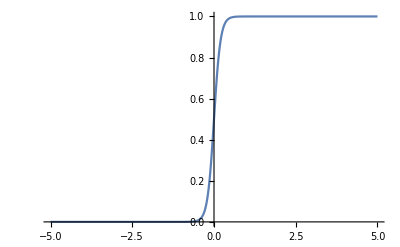

```mathematica
Plot[1/(1+Exp[-10t]),{t,-5,5}]
```

## Model equations

```mathematica
TotNumVariables=11;
VarNumbers= Table[j, {j, 1, TotNumVariables}]
EqNumbers=Table[k,{k,1,NumAgeGroups TotNumVariables}]

Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-Subscript[r,k] Subscript[S,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t]-Subscript[r,k] Subscript[EE,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t]-Subscript[r,k] Subscript[R,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*+δ Subscript[H,k][t]*),
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]-Subscript[r,k] Subscript[H,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*-δ Subscript[H,k][t]*),
eq[Intervention_][6,k]:=Subscript[SV,k]'[t]==-Subscript[λV,k][Intervention][t]Subscript[β,k](1-Subscript[ω,1])Subscript[SV,k][t]+Subscript[r,k] Subscript[S,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][7,k]:=Subscript[EEV,k]'[t]== Subscript[λV,k][Intervention][t]Subscript[β,k] (1-Subscript[ω,1]) Subscript[SV,k][t]-α Subscript[EEV,k][t]+Subscript[r,k] Subscript[EE,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][8,k]:=Subscript[IIV,k]'[t]== α Subscript[EEV,k][t]-(γ+Subscript[ν,k] (1-Subscript[ω,3])) Subscript[IIV,k][t],
eq[Intervention_][9,k]:=Subscript[RV,k]'[t]== γ Subscript[IIV,k][t]+Subscript[r,k] Subscript[R,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*+δ Subscript[HV,k][t]*),
eq[Intervention_][10,k]:=Subscript[P,k]'[t]== 0,
eq[Intervention_][11,k]:=Subscript[HV,k]'[t]==Subscript[ν,k] (1-Subscript[ω,3]) Subscript[IIV,k][t]+Subscript[r,k] Subscript[H,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*-δ Subscript[HV,k][t]*)
(*eq[Intervention_][10,k]:=Subscript[VV,k]'[t]==Subscript[r,k]*)
},{k,AgeGroups}];

(*Table[Subscript[NN,k][t]=(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[II,k][t]+Subscript[R,k][t]+Subscript[H,k][t]+Subscript[SV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[RV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t]),{k,AgeGroups}];*)

NNtot=Sum[Subscript[NN,k],{k,AgeGroups}];

Table[Subscript[V,k][t]=Subscript[SV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[RV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t],{k,AgeGroups}];

(* Table[Subscript[λ,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[((1-1/(1+Exp[-K0 (t-x0)])) Subscript[c,{k,l}]+1/(1+Exp[-KK (t-x0)]) ζ Subscript[d,{k,l}]) Subscript[II,l][t]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; *)

Table[Subscript[λ,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[ContactMatrix[t] (Subscript[II,l][t]+(1-Subscript[ω,2]) Subscript[IIV,l][t])/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; 

Table[Subscript[λV,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[ContactMatrixV[t] (Subscript[II,l][t]+(1-Subscript[ω,2]) Subscript[IIV,l][t])/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; 

Eqs[Intervention_]:=Table[eq[Intervention][j,k],{j,TotNumVariables},{k,AgeGroups}]

TableForm[Eqs[Intervention]]

EqsList[Intervention_]:=Flatten[Flatten[Eqs[Intervention]]];

Total[EqsList[Intervention]⟦All,2⟧]//Simplify
```

{1,2,3,4,5,6,7,8,9,10,11}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110}

S_1'[t]==-(r_1 S_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])-β_1 S_1[t] λ_1[Intervention][t] | S_2'[t]==-(r_2 S_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])-β_2 S_2[t] λ_2[Intervention][t] | S_3'[t]==-(r_3 S_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])-β_3 S_3[t] λ_3[Intervention][t] | S_4'[t]==-(r_4 S_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])-β_4 S_4[t] λ_4[Intervention][t] | S_5'[t]==-(r_5 S_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])-β_5 S_5[t] λ_5[Intervention][t] | S_6'[t]==-(r_6 S_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])-β_6 S_6[t] λ_6[Intervention][t] | S_7'[t]==-(r_7 S_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])-β_7 S_7[t] λ_7[Intervention][t] | S_8'[t]==-(r_8 S_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])-β_8 S_8[t] λ_8[Intervention][t] | S_9'[t]==-(r_9 S_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])-β_9 S_9[t] λ_9[Intervention][t] | S_10'[t]==-(r_10 S_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])-β_10 S_10[t] λ_10[Intervention][t]
EE_1'[t]==-α EE_1[t]-(r_1 EE_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])+β_1 S_1[t] λ_1[Intervention][t] | EE_2'[t]==-α EE_2[t]-(r_2 EE_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])+β_2 S_2[t] λ_2[Intervention][t] | EE_3'[t]==-α EE_3[t]-(r_3 EE_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])+β_3 S_3[t] λ_3[Intervention][t] | EE_4'[t]==-α EE_4[t]-(r_4 EE_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])+β_4 S_4[t] λ_4[Intervention][t] | EE_5'[t]==-α EE_5[t]-(r_5 EE_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])+β_5 S_5[t] λ_5[Intervention][t] | EE_6'[t]==-α EE_6[t]-(r_6 EE_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])+β_6 S_6[t] λ_6[Intervention][t] | EE_7'[t]==-α EE_7[t]-(r_7 EE_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])+β_7 S_7[t] λ_7[Intervention][t] | EE_8'[t]==-α EE_8[t]-(r_8 EE_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])+β_8 S_8[t] λ_8[Intervention][t] | EE_9'[t]==-α EE_9[t]-(r_9 EE_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])+β_9 S_9[t] λ_9[Intervention][t] | EE_10'[t]==-α EE_10[t]-(r_10 EE_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])+β_10 S_10[t] λ_10[Intervention][t]
II_1'[t]==α EE_1[t]-(γ+ν_1) II_1[t] | II_2'[t]==α EE_2[t]-(γ+ν_2) II_2[t] | II_3'[t]==α EE_3[t]-(γ+ν_3) II_3[t] | II_4'[t]==α EE_4[t]-(γ+ν_4) II_4[t] | II_5'[t]==α EE_5[t]-(γ+ν_5) II_5[t] | II_6'[t]==α EE_6[t]-(γ+ν_6) II_6[t] | II_7'[t]==α EE_7[t]-(γ+ν_7) II_7[t] | II_8'[t]==α EE_8[t]-(γ+ν_8) II_8[t] | II_9'[t]==α EE_9[t]-(γ+ν_9) II_9[t] | II_10'[t]==α EE_10[t]-(γ+ν_10) II_10[t]
R_1'[t]==γ II_1[t]-(r_1 R_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | R_2'[t]==γ II_2[t]-(r_2 R_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | R_3'[t]==γ II_3[t]-(r_3 R_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | R_4'[t]==γ II_4[t]-(r_4 R_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | R_5'[t]==γ II_5[t]-(r_5 R_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | R_6'[t]==γ II_6[t]-(r_6 R_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | R_7'[t]==γ II_7[t]-(r_7 R_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | R_8'[t]==γ II_8[t]-(r_8 R_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | R_9'[t]==γ II_9[t]-(r_9 R_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | R_10'[t]==γ II_10[t]-(r_10 R_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
H_1'[t]==ν_1 II_1[t]-(r_1 H_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | H_2'[t]==ν_2 II_2[t]-(r_2 H_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | H_3'[t]==ν_3 II_3[t]-(r_3 H_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | H_4'[t]==ν_4 II_4[t]-(r_4 H_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | H_5'[t]==ν_5 II_5[t]-(r_5 H_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | H_6'[t]==ν_6 II_6[t]-(r_6 H_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | H_7'[t]==ν_7 II_7[t]-(r_7 H_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | H_8'[t]==ν_8 II_8[t]-(r_8 H_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | H_9'[t]==ν_9 II_9[t]-(r_9 H_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | H_10'[t]==ν_10 II_10[t]-(r_10 H_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
SV_1'[t]==(r_1 S_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])-β_1 (1-ω_1) SV_1[t] λV_1[Intervention][t] | SV_2'[t]==(r_2 S_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])-β_2 (1-ω_1) SV_2[t] λV_2[Intervention][t] | SV_3'[t]==(r_3 S_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])-β_3 (1-ω_1) SV_3[t] λV_3[Intervention][t] | SV_4'[t]==(r_4 S_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])-β_4 (1-ω_1) SV_4[t] λV_4[Intervention][t] | SV_5'[t]==(r_5 S_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])-β_5 (1-ω_1) SV_5[t] λV_5[Intervention][t] | SV_6'[t]==(r_6 S_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])-β_6 (1-ω_1) SV_6[t] λV_6[Intervention][t] | SV_7'[t]==(r_7 S_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])-β_7 (1-ω_1) SV_7[t] λV_7[Intervention][t] | SV_8'[t]==(r_8 S_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])-β_8 (1-ω_1) SV_8[t] λV_8[Intervention][t] | SV_9'[t]==(r_9 S_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])-β_9 (1-ω_1) SV_9[t] λV_9[Intervention][t] | SV_10'[t]==(r_10 S_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])-β_10 (1-ω_1) SV_10[t] λV_10[Intervention][t]
EEV_1'[t]==-α EEV_1[t]+(r_1 EE_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])+β_1 (1-ω_1) SV_1[t] λV_1[Intervention][t] | EEV_2'[t]==-α EEV_2[t]+(r_2 EE_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])+β_2 (1-ω_1) SV_2[t] λV_2[Intervention][t] | EEV_3'[t]==-α EEV_3[t]+(r_3 EE_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])+β_3 (1-ω_1) SV_3[t] λV_3[Intervention][t] | EEV_4'[t]==-α EEV_4[t]+(r_4 EE_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])+β_4 (1-ω_1) SV_4[t] λV_4[Intervention][t] | EEV_5'[t]==-α EEV_5[t]+(r_5 EE_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])+β_5 (1-ω_1) SV_5[t] λV_5[Intervention][t] | EEV_6'[t]==-α EEV_6[t]+(r_6 EE_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])+β_6 (1-ω_1) SV_6[t] λV_6[Intervention][t] | EEV_7'[t]==-α EEV_7[t]+(r_7 EE_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])+β_7 (1-ω_1) SV_7[t] λV_7[Intervention][t] | EEV_8'[t]==-α EEV_8[t]+(r_8 EE_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])+β_8 (1-ω_1) SV_8[t] λV_8[Intervention][t] | EEV_9'[t]==-α EEV_9[t]+(r_9 EE_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])+β_9 (1-ω_1) SV_9[t] λV_9[Intervention][t] | EEV_10'[t]==-α EEV_10[t]+(r_10 EE_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])+β_10 (1-ω_1) SV_10[t] λV_10[Intervention][t]
IIV_1'[t]==α EEV_1[t]-(γ+ν_1 (1-ω_3)) IIV_1[t] | IIV_2'[t]==α EEV_2[t]-(γ+ν_2 (1-ω_3)) IIV_2[t] | IIV_3'[t]==α EEV_3[t]-(γ+ν_3 (1-ω_3)) IIV_3[t] | IIV_4'[t]==α EEV_4[t]-(γ+ν_4 (1-ω_3)) IIV_4[t] | IIV_5'[t]==α EEV_5[t]-(γ+ν_5 (1-ω_3)) IIV_5[t] | IIV_6'[t]==α EEV_6[t]-(γ+ν_6 (1-ω_3)) IIV_6[t] | IIV_7'[t]==α EEV_7[t]-(γ+ν_7 (1-ω_3)) IIV_7[t] | IIV_8'[t]==α EEV_8[t]-(γ+ν_8 (1-ω_3)) IIV_8[t] | IIV_9'[t]==α EEV_9[t]-(γ+ν_9 (1-ω_3)) IIV_9[t] | IIV_10'[t]==α EEV_10[t]-(γ+ν_10 (1-ω_3)) IIV_10[t]
RV_1'[t]==γ IIV_1[t]+(r_1 R_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | RV_2'[t]==γ IIV_2[t]+(r_2 R_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | RV_3'[t]==γ IIV_3[t]+(r_3 R_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | RV_4'[t]==γ IIV_4[t]+(r_4 R_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | RV_5'[t]==γ IIV_5[t]+(r_5 R_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | RV_6'[t]==γ IIV_6[t]+(r_6 R_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | RV_7'[t]==γ IIV_7[t]+(r_7 R_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | RV_8'[t]==γ IIV_8[t]+(r_8 R_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | RV_9'[t]==γ IIV_9[t]+(r_9 R_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | RV_10'[t]==γ IIV_10[t]+(r_10 R_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
P_1'[t]==0 | P_2'[t]==0 | P_3'[t]==0 | P_4'[t]==0 | P_5'[t]==0 | P_6'[t]==0 | P_7'[t]==0 | P_8'[t]==0 | P_9'[t]==0 | P_10'[t]==0
HV_1'[t]==ν_1 (1-ω_3) IIV_1[t]+(r_1 H_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | HV_2'[t]==ν_2 (1-ω_3) IIV_2[t]+(r_2 H_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | HV_3'[t]==ν_3 (1-ω_3) IIV_3[t]+(r_3 H_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | HV_4'[t]==ν_4 (1-ω_3) IIV_4[t]+(r_4 H_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | HV_5'[t]==ν_5 (1-ω_3) IIV_5[t]+(r_5 H_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | HV_6'[t]==ν_6 (1-ω_3) IIV_6[t]+(r_6 H_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | HV_7'[t]==ν_7 (1-ω_3) IIV_7[t]+(r_7 H_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | HV_8'[t]==ν_8 (1-ω_3) IIV_8[t]+(r_8 H_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | HV_9'[t]==ν_9 (1-ω_3) IIV_9[t]+(r_9 H_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | HV_10'[t]==ν_10 (1-ω_3) IIV_10[t]+(r_10 H_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])

0

## Model variables

```mathematica
varsS=Table[Subscript[S,k][t],{k,AgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,AgeGroups}];
varsII=Table[Subscript[II,k][t],{k,AgeGroups}];
varsR=Table[Subscript[R,k][t],{k,AgeGroups}];
varsH=Table[Subscript[H,k][t],{k,AgeGroups}];

varsSV=Table[Subscript[SV,k][t],{k,AgeGroups}];
varsEEV=Table[Subscript[EEV,k][t],{k,AgeGroups}];
varsIIV=Table[Subscript[IIV,k][t],{k,AgeGroups}];
varsRV=Table[Subscript[RV,k][t],{k,AgeGroups}];
varsP=Table[Subscript[P,k][t],{k,AgeGroups}];
varsHV=Table[Subscript[HV,k][t],{k,AgeGroups}];

totS=Total[Total[varsS]];
totEE=Total[Total[varsEE]];
totII=Total[Total[varsII]];
totR=Total[Total[varsR]];
totH=Total[Total[varsH]];

totSV=Total[Total[varsSV]];
totEEV=Total[Total[varsEEV]];
totIIV=Total[Total[varsIIV]];
totRV=Total[Total[varsRV]];
totP=Total[Total[varsP]];
totHV=Total[Total[varsHV]];

totVars={totS,totEE,totII,totR,totH,totSV,totEEV,totIIV,totRV,totP,totHV};
totVarsYlab={"S(t)","E(t)","I(t)","R(t)","H(t)","S^V(t)","E^V(t)","I^V(t)","R^V(t)","P(t)","H^V(t)"};

ageVars={Subscript[S,k][t],Subscript[EE,k][t],Subscript[II,k][t],Subscript[R,k][t],Subscript[H,k][t],Subscript[SV,k][t],Subscript[EEV,k][t],Subscript[IIV,k][t],Subscript[RV,k][t],Subscript[P,k][t],Subscript[HV,k][t],Subscript[V,k][t]};
ageVarsYlab={"S_k(t)","E_k(t)","I_k(t)","R_k(t)","H_k(t)","(S^V)_k(t)","(E^V)_k(t)","(I^V)_k(t)","(R^V)_k(t)","P_k(t)","(H^V)_k(t)","V_k(t)"};

Vars=Join[varsS,varsEE,varsII,varsR,varsH,varsSV,varsEEV,varsIIV,varsRV,varsP,varsHV];
VarsList=Flatten[Vars];

hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]+Subscript[IIV,k][t]),{k,AgeGroups}];

InfIncidenceVars=Table[α (Subscript[EE,k][t]+Subscript[EEV,k][t]),{k,AgeGroups}];

VacPropVars=Table[Subscript[V,k][t]/Subscript[NN,k],{k,AgeGroups}];
```

## Initial conditions Solving equations with and without vaccination Vaccination stops when all individuals in a given age group get vaccinated Other conditions are possible MAP parameter sample

```mathematica
Subscript[t, start]=t0;
Subscript[t, end]=tendvac;

ICs=Table[ic[j,k],{j,VarNumbers},{k,AgeGroups}];
ICsList=Flatten[Flatten[ICs]];
Dimensions[ICsList];

Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[6,k]=0==Subscript[SV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[7,k]=0==Subscript[EEV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[8,k]=0==Subscript[IIV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[9,k]=0==Subscript[RV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[10,k]=0==Subscript[P,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[11,k]=0==Subscript[HV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];

intList={"Estimation"};

solution[Intervention_,pars_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.pars,VarsList,{t,Subscript[t, start],Subscript[t, end]}, Method->"StiffnessSwitching"];

Table[sol[it]=solution[intList⟦it⟧,ParametersMAPNoVaccination],{it,1,Length[intList]}];
Table[solVac[it]=solution[intList⟦it⟧,ParametersMAPVaccination],{it,1,Length[intList]}];

AspRat=0.75;
ImSize=250;

PlottotVars[sol_]:=Grid[Table[Table[Plot[Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.sol[it]],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->{Thick,Darker[Blue]},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{totVarsYlab⟦i⟧,None},{"Days",None}}],{i,1,Length[totVars]}],{it,1,Length[intList]}]];

PlotageVars[sol_]:=Grid[Table[Table[Plot[
Evaluate[Table[(ageVars⟦i⟧/Subscript[NN,k]/.Demography)/.sol[it],{k,AgeGroups}]],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->"DarkRainbow",AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{ageVarsYlab⟦i⟧,None},{"Days",None}},PlotLegends->Placed[AgeLabelShort,Right]],{i,1,Length[ageVars]}],{it,1,Length[intList]}]];

PlottotVarsComparison=Grid[Table[Table[Plot[{Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.sol[it]],Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.solVac[it]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Red]}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{totVarsYlab⟦i⟧,None},{"Days",None}}],{i,1,Length[totVars]}],{it,1,Length[intList]}]];
```

## Prevalence of individuals in different classes Prevalence of individuals in different classes per age group

Solutions without vaccination

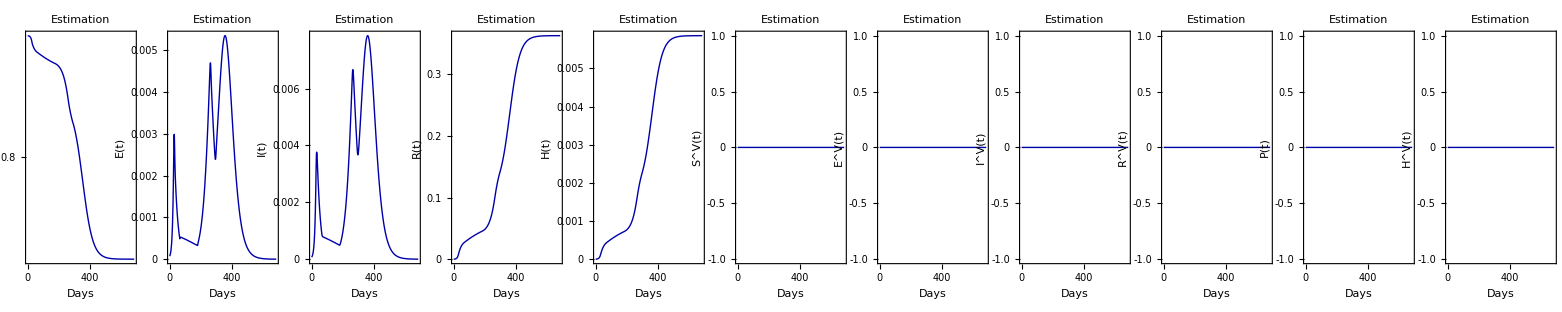

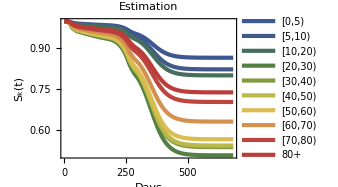
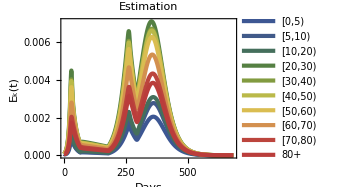
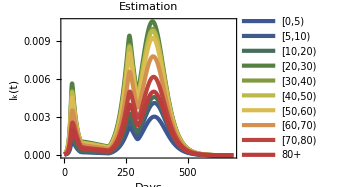
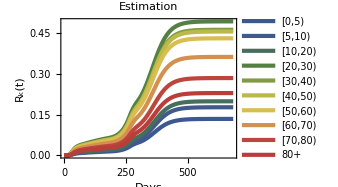
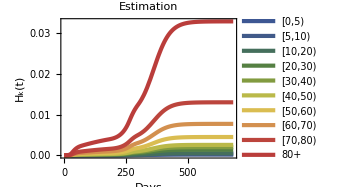
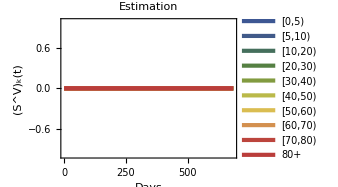
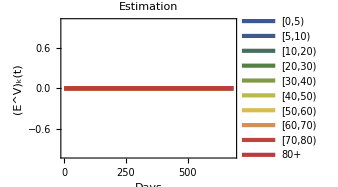
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Solutions with vaccination

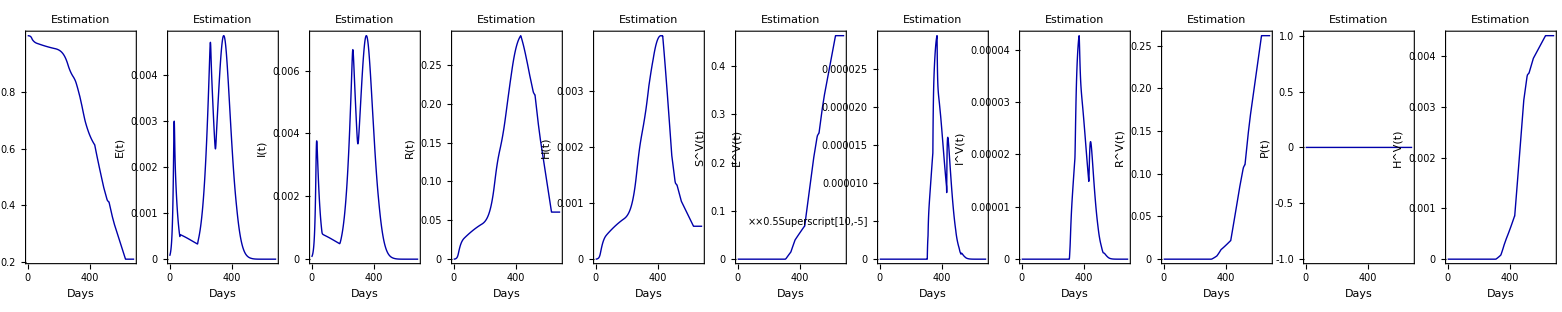

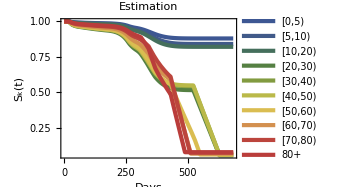
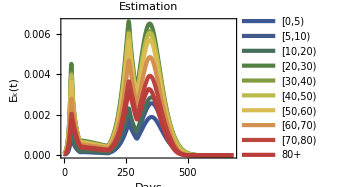
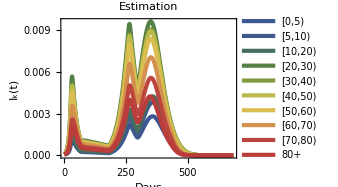
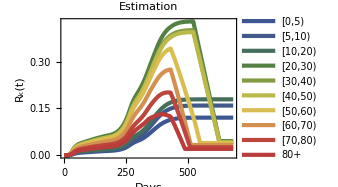
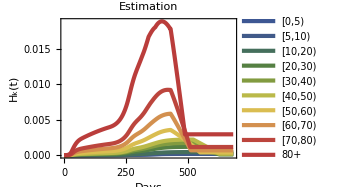
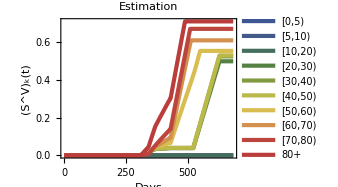
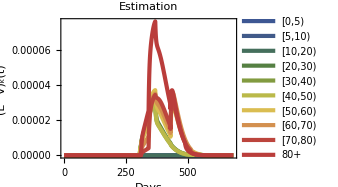
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Comparison solutions without and with vaccination

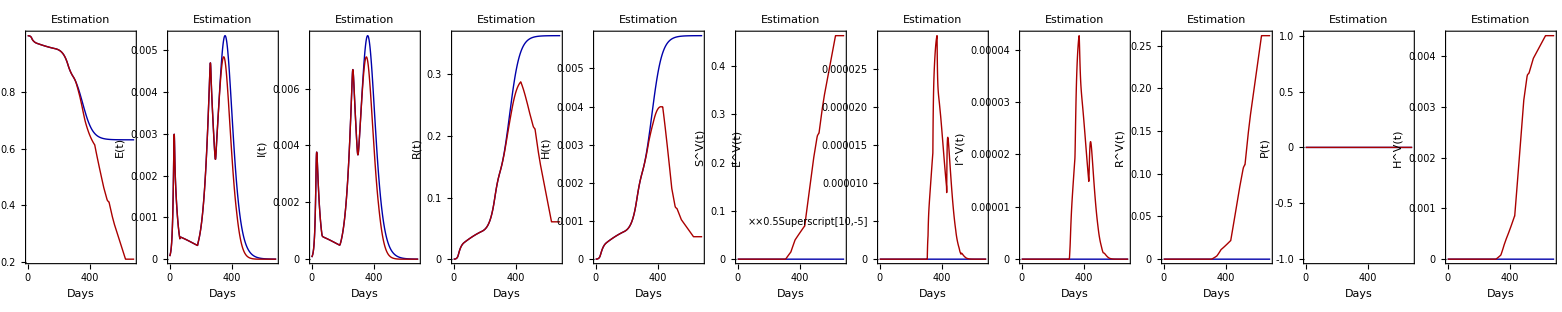

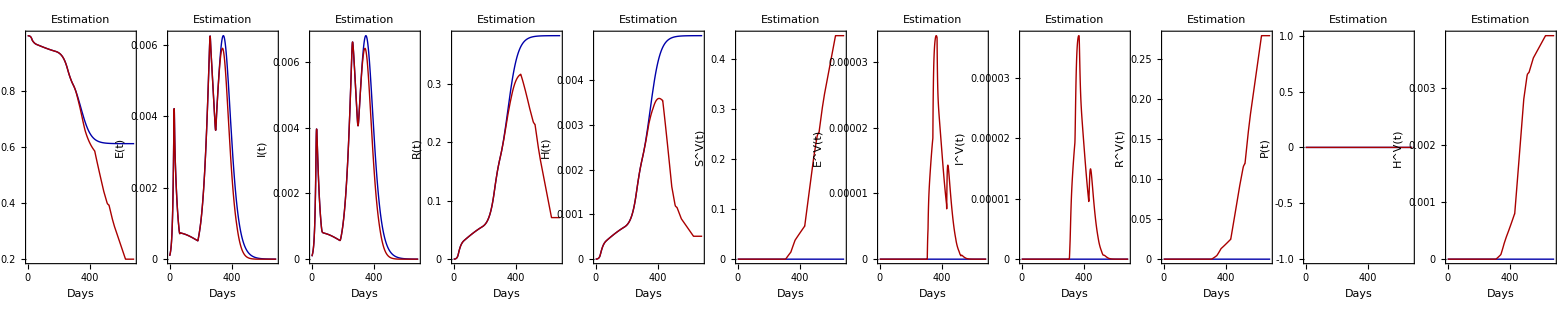

```mathematica
Print[Style["Solutions without vaccination",18,Blue,"Text"]]
PlottotVars[sol]
PlotageVars[sol]

Print[Style["Solutions with vaccination",18,Blue,"Text"]]
PlottotVars[solVac]
PlotageVars[solVac]

Print[Style["Comparison solutions without and with vaccination",18,Blue,"Text"]]
PlottotVarsComparison
```

```mathematica
Memory
```

Memory Used:125.683 MB

# Execution

## Choose times and samples

```mathematica
Subscript[t, step]=1;
Subscript[t, end]=tenddata;

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=1;
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];

HospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[ListSamples⟦sample⟧]]],0],{k,AgeGroups},{sample,1,Length[ListSamples]},{t,1,Dimensions[var]⟦3⟧}];

ExportData[var_,filename_]:=Table[Export[StringJoin["MathematicaFiles//ModelFit//",filename,ToString[k],".txt"],var⟦k⟧,"Table"],{k,AgeGroups}];
```

## Solutions with credible intervals

## No vaccination

```mathematica
(**********************************************************)


ParametersAllNoVaccination=Table[ParametersNoVaccination[i],{i,1,nSamples,stepSamples}];

solAll=Table[NDSolve[Join[EqsList["Estimation"],ICsList]/.ParametersAllNoVaccination⟦i⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]} ,Method->"StiffnessSwitching"],{i,1,Length[ListSamples]}];

Trajectories[var_]:=Table[Table[Table[Evaluate[(var⟦k⟧/.ParametersAllNoVaccination⟦i⟧)/.First@solAll⟦i⟧],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}],{k,AgeGroups}];

TrajectoriesS[var_]:=Table[Table[Table[Evaluate[((If[k==1,(DemographyData10⟦1⟧-86579)/DemographyData10⟦1⟧,1] var⟦k⟧/.ParametersAllNoVaccination⟦i⟧)+If[k==1,86579,0])/.First@solAll⟦i⟧],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}],{k,AgeGroups}];

HospIncidence=Trajectories[hospVars];
ExportData[HospIncidence,"HospIncidence"];

(*InfIncidence=Trajectories[InfIncidenceVars];
ExportData[InfIncidence,"InfIncidence"];*)

HospIncidenceSimulated=HospSimulated[HospIncidence];
ExportData[HospIncidenceSimulated,"HospIncidenceSimulated"];

Susceptible=TrajectoriesS[varsS];
ExportData[Susceptible,"Susceptible"];

(*SusceptibleVaccinated=Trajectories[varsSV];
ExportData[SusceptibleVaccinated,"SusceptibleVaccinated"];*)

Memory
```

Memory Used:1763.94 MB

## Solutions with credible intervals

## Vaccination

```mathematica
(*Clear[solAll,Trajectories]

ParametersAllVaccination=Table[ParametersVaccination[i],{i,1,nSamples,stepSamples}];

solAll=Table[NDSolve[Join[EqsList["Estimation"],ICsList]/.ParametersAllVaccination⟦i⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]} ,Method->"StiffnessSwitching"],{i,1,Length[ListSamples]}];

Trajectories[var_]:=Table[Table[Table[Evaluate[(var⟦k⟧/.ParametersAllVaccination⟦i⟧)/.First@solAll⟦i⟧],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}],{k,AgeGroups}];

VaccinatedProportion=Trajectories[VacPropVars];
ExportData[VaccinatedProportion,"VaccinatedProportion"];

Memory*)
```

Memory Used:189.475 MB

# Plotting

## Preliminaries

```mathematica
HospIncidence=Table[Import[StringJoin["MathematicaFiles//ModelFit//HospIncidence",ToString[k],".txt"],"Table"],{k,AgeGroups}];
(*InfIncidence=Table[Import[StringJoin["MathematicaFiles//ModelFit//InfIncidence",ToString[k],".txt"],"Table"],{k,AgeGroups}];*)
HospIncidenceSimulated=Table[Import[StringJoin["MathematicaFiles//ModelFit//HospIncidenceSimulated",ToString[k],".txt"],"Table"],{k,AgeGroups}];

VaccinatedProportion=Table[Import[StringJoin["MathematicaFiles//ModelFit//VaccinatedProportion",ToString[k],".txt"],"Table"],{k,AgeGroups}];

Susceptible=Table[Import[StringJoin["MathematicaFiles//ModelFit//Susceptible",ToString[k],".txt"],"Table"],{k,AgeGroups}];
(*SusceptibleVaccinated=Table[Import[StringJoin["MathematicaFiles//ModelFit//SusceptibleVaccinated",ToString[k],".txt"],"Table"],{k,AgeGroups}];*)
```

## Plot vaccination coverage

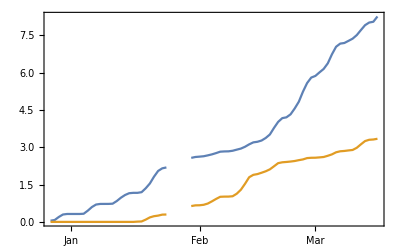

```mathematica
VacDataRaw=Import["Data//VaccinationsOWD.xlsx"];
VacData1dose=Transpose[{VacDataRaw⟦1⟧⟦All,2⟧,100 VacDataRaw⟦1⟧⟦All,6⟧/Total[DemographyData10]}];
VacData2doses=Transpose[{VacDataRaw⟦1⟧⟦All,2⟧,100 VacDataRaw⟦1⟧⟦All,7⟧/Total[DemographyData10]}];
DateListPlot[{VacData1dose,VacData2doses}]
```

Vaccinated proportion (%) in each age group

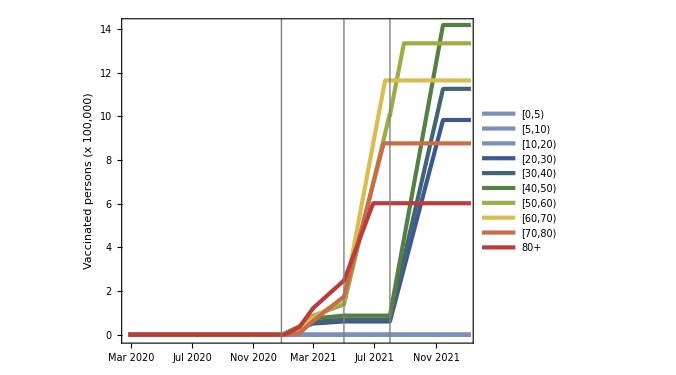

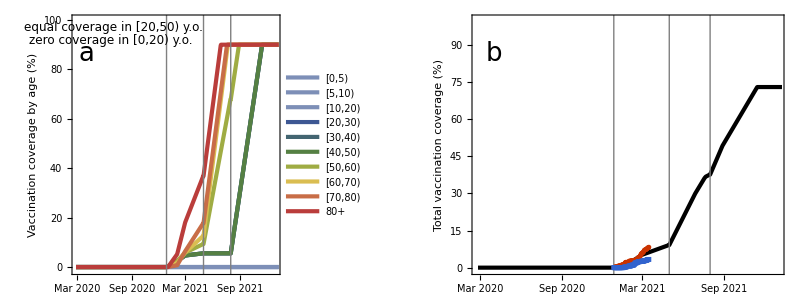

```mathematica
Print[Style["Vaccinated proportion (%) in each age group",24,Blue,"Text"]];

AspRat=0.75; ImSize=500;

tickValues=DateRange[{2020,3,1},{2022,1,1},{2,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

BarChartLegends=Style[#,Black]&/@{"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

ChartStyleColors=Join[{Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]](*ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0]*)},ColorData["DarkRainbow"]/@Rescale[AgeGroups⟦1;;7⟧]];

LineWidthsAll=Table[Thickness[0.005],{k,AgeGroups}];

fig2A=Show[
DateListPlot[Table[VaccinatedProportion⟦k,1⟧ 100,{k,AgeGroups}],"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-1,100}},AspectRatio->AspRat,ImageSize->ImSize,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{"Vaccination coverage by age (%)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotLegends->Placed[BarChartLegends,Scaled[{{0.25, 0.450}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->ChartStyleColors(*Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],Graphics[Text[StyleForm["equal coverage in [20,50) y.o.",FontSize->12],Scaled[{0.2,0.95}]]],Graphics[Text[StyleForm["zero coverage in [0,20) y.o.",FontSize->12],Scaled[{0.185,0.9}]]],Graphics[Text[StyleForm["a",FontSize->26],Scaled[{0.07,0.85}]]]];

SFig5=Show[
DateListPlot[Table[VaccinatedProportion⟦k,1⟧ DemographyData10⟦k⟧,{k,AgeGroups}]/100000,"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-0.1,All}},AspectRatio->AspRat,ImageSize->ImSize,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{"Vaccinated persons (x 100,000)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotLegends->Placed[BarChartLegends,Scaled[{{0.25, 0.50}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->ChartStyleColors(*Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}]]

(* !!! Table[Export[StringJoin["Figures//SFig4",format⟦i⟧],SFig5],{i,1,Length[format]}]; *)

fig2B=Show[
DateListPlot[Sum[VaccinatedProportion⟦k,1⟧ DemographyData10⟦k⟧,{k,AgeGroups}] 100/Total[DemographyData10],"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-0.75,100}},AspectRatio->AspRat,ImageSize->ImSize,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{"Total vaccination coverage (%)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotStyle->{Black}(*,PlotLegends->Placed[Style[#,Black]&/@{"[20,80+) y.o."},Scaled[{{0.25, 0.50}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}],DateListPlot[{VacData1dose,VacData2doses},PlotMarkers->{Automatic,5},Joined-> False,PlotTheme->"Web"],Graphics[Text[StyleForm["b",FontSize->26],Scaled[{0.07,0.85}]]]];


fig2=Grid[{{fig2A,fig2B}}]

(* !!! Table[Export[StringJoin["Figures//Fig5",format⟦i⟧],fig2],{i,1,Length[format]}]; *)
```

```mathematica
Join[{DateRange[{2020,02,25},{2022,1,10},{1,"Day"}]},Table[VaccinatedProportion⟦k,1⟧ 100,{k,AgeGroups}]]//MatrixForm

{DateRange[{2020,02,25},{2022,1,10},{1,"Day"}],Sum[VaccinatedProportion⟦k,1⟧ DemographyData10⟦k⟧,{k,AgeGroups}] 100/Total[DemographyData10]}//MatrixForm
```

({2020,2,25} | {2020,2,26} | {2020,2,27} | {2020,2,28} | {2020,2,29} | {2020,3,1} | {2020,3,2} | {2020,3,3} | {2020,3,4} | {2020,3,5} | {2020,3,6} | {2020,3,7} | {2020,3,8} | {2020,3,9} | {2020,3,10} | {2020,3,11} | {2020,3,12} | {2020,3,13} | {2020,3,14} | {2020,3,15} | {2020,3,16} | {2020,3,17} | {2020,3,18} | {2020,3,19} | {2020,3,20} | {2020,3,21} | {2020,3,22} | {2020,3,23} | {2020,3,24} | {2020,3,25} | {2020,3,26} | {2020,3,27} | {2020,3,28} | {2020,3,29} | {2020,3,30} | {2020,3,31} | {2020,4,1} | {2020,4,2} | {2020,4,3} | {2020,4,4} | {2020,4,5} | {2020,4,6} | {2020,4,7} | {2020,4,8} | {2020,4,9} | {2020,4,10} | {2020,4,11} | {2020,4,12} | {2020,4,13} | {2020,4,14} | {2020,4,15} | {2020,4,16} | {2020,4,17} | {2020,4,18} | {2020,4,19} | {2020,4,20} | {2020,4,21} | {2020,4,22} | {2020,4,23} | {2020,4,24} | {2020,4,25} | {2020,4,26} | {2020,4,27} | {2020,4,28} | {2020,4,29} | {2020,4,30} | {2020,5,1} | {2020,5,2} | {2020,5,3} | {2020,5,4} | {2020,5,5} | {2020,5,6} | {2020,5,7} | {2020,5,8} | {2020,5,9} | {2020,5,10} | {2020,5,11} | {2020,5,12} | {2020,5,13} | {2020,5,14} | {2020,5,15} | {2020,5,16} | {2020,5,17} | {2020,5,18} | {2020,5,19} | {2020,5,20} | {2020,5,21} | {2020,5,22} | {2020,5,23} | {2020,5,24} | {2020,5,25} | {2020,5,26} | {2020,5,27} | {2020,5,28} | {2020,5,29} | {2020,5,30} | {2020,5,31} | {2020,6,1} | {2020,6,2} | {2020,6,3} | {2020,6,4} | {2020,6,5} | {2020,6,6} | {2020,6,7} | {2020,6,8} | {2020,6,9} | {2020,6,10} | {2020,6,11} | {2020,6,12} | {2020,6,13} | {2020,6,14} | {2020,6,15} | {2020,6,16} | {2020,6,17} | {2020,6,18} | {2020,6,19} | {2020,6,20} | {2020,6,21} | {2020,6,22} | {2020,6,23} | {2020,6,24} | {2020,6,25} | {2020,6,26} | {2020,6,27} | {2020,6,28} | {2020,6,29} | {2020,6,30} | {2020,7,1} | {2020,7,2} | {2020,7,3} | {2020,7,4} | {2020,7,5} | {2020,7,6} | {2020,7,7} | {2020,7,8} | {2020,7,9} | {2020,7,10} | {2020,7,11} | {2020,7,12} | {2020,7,13} | {2020,7,14} | {2020,7,15} | {2020,7,16} | {2020,7,17} | {2020,7,18} | {2020,7,19} | {2020,7,20} | {2020,7,21} | {2020,7,22} | {2020,7,23} | {2020,7,24} | {2020,7,25} | {2020,7,26} | {2020,7,27} | {2020,7,28} | {2020,7,29} | {2020,7,30} | {2020,7,31} | {2020,8,1} | {2020,8,2} | {2020,8,3} | {2020,8,4} | {2020,8,5} | {2020,8,6} | {2020,8,7} | {2020,8,8} | {2020,8,9} | {2020,8,10} | {2020,8,11} | {2020,8,12} | {2020,8,13} | {2020,8,14} | {2020,8,15} | {2020,8,16} | {2020,8,17} | {2020,8,18} | {2020,8,19} | {2020,8,20} | {2020,8,21} | {2020,8,22} | {2020,8,23} | {2020,8,24} | {2020,8,25} | {2020,8,26} | {2020,8,27} | {2020,8,28} | {2020,8,29} | {2020,8,30} | {2020,8,31} | {2020,9,1} | {2020,9,2} | {2020,9,3} | {2020,9,4} | {2020,9,5} | {2020,9,6} | {2020,9,7} | {2020,9,8} | {2020,9,9} | {2020,9,10} | {2020,9,11} | {2020,9,12} | {2020,9,13} | {2020,9,14} | {2020,9,15} | {2020,9,16} | {2020,9,17} | {2020,9,18} | {2020,9,19} | {2020,9,20} | {2020,9,21} | {2020,9,22} | {2020,9,23} | {2020,9,24} | {2020,9,25} | {2020,9,26} | {2020,9,27} | {2020,9,28} | {2020,9,29} | {2020,9,30} | {2020,10,1} | {2020,10,2} | {2020,10,3} | {2020,10,4} | {2020,10,5} | {2020,10,6} | {2020,10,7} | {2020,10,8} | {2020,10,9} | {2020,10,10} | {2020,10,11} | {2020,10,12} | {2020,10,13} | {2020,10,14} | {2020,10,15} | {2020,10,16} | {2020,10,17} | {2020,10,18} | {2020,10,19} | {2020,10,20} | {2020,10,21} | {2020,10,22} | {2020,10,23} | {2020,10,24} | {2020,10,25} | {2020,10,26} | {2020,10,27} | {2020,10,28} | {2020,10,29} | {2020,10,30} | {2020,10,31} | {2020,11,1} | {2020,11,2} | {2020,11,3} | {2020,11,4} | {2020,11,5} | {2020,11,6} | {2020,11,7} | {2020,11,8} | {2020,11,9} | {2020,11,10} | {2020,11,11} | {2020,11,12} | {2020,11,13} | {2020,11,14} | {2020,11,15} | {2020,11,16} | {2020,11,17} | {2020,11,18} | {2020,11,19} | {2020,11,20} | {2020,11,21} | {2020,11,22} | {2020,11,23} | {2020,11,24} | {2020,11,25} | {2020,11,26} | {2020,11,27} | {2020,11,28} | {2020,11,29} | {2020,11,30} | {2020,12,1} | {2020,12,2} | {2020,12,3} | {2020,12,4} | {2020,12,5} | {2020,12,6} | {2020,12,7} | {2020,12,8} | {2020,12,9} | {2020,12,10} | {2020,12,11} | {2020,12,12} | {2020,12,13} | {2020,12,14} | {2020,12,15} | {2020,12,16} | {2020,12,17} | {2020,12,18} | {2020,12,19} | {2020,12,20} | {2020,12,21} | {2020,12,22} | {2020,12,23} | {2020,12,24} | {2020,12,25} | {2020,12,26} | {2020,12,27} | {2020,12,28} | {2020,12,29} | {2020,12,30} | {2020,12,31} | {2021,1,1} | {2021,1,2} | {2021,1,3} | {2021,1,4} | {2021,1,5} | {2021,1,6} | {2021,1,7} | {2021,1,8} | {2021,1,9} | {2021,1,10} | {2021,1,11} | {2021,1,12} | {2021,1,13} | {2021,1,14} | {2021,1,15} | {2021,1,16} | {2021,1,17} | {2021,1,18} | {2021,1,19} | {2021,1,20} | {2021,1,21} | {2021,1,22} | {2021,1,23} | {2021,1,24} | {2021,1,25} | {2021,1,26} | {2021,1,27} | {2021,1,28} | {2021,1,29} | {2021,1,30} | {2021,1,31} | {2021,2,1} | {2021,2,2} | {2021,2,3} | {2021,2,4} | {2021,2,5} | {2021,2,6} | {2021,2,7} | {2021,2,8} | {2021,2,9} | {2021,2,10} | {2021,2,11} | {2021,2,12} | {2021,2,13} | {2021,2,14} | {2021,2,15} | {2021,2,16} | {2021,2,17} | {2021,2,18} | {2021,2,19} | {2021,2,20} | {2021,2,21} | {2021,2,22} | {2021,2,23} | {2021,2,24} | {2021,2,25} | {2021,2,26} | {2021,2,27} | {2021,2,28} | {2021,3,1} | {2021,3,2} | {2021,3,3} | {2021,3,4} | {2021,3,5} | {2021,3,6} | {2021,3,7} | {2021,3,8} | {2021,3,9} | {2021,3,10} | {2021,3,11} | {2021,3,12} | {2021,3,13} | {2021,3,14} | {2021,3,15} | {2021,3,16} | {2021,3,17} | {2021,3,18} | {2021,3,19} | {2021,3,20} | {2021,3,21} | {2021,3,22} | {2021,3,23} | {2021,3,24} | {2021,3,25} | {2021,3,26} | {2021,3,27} | {2021,3,28} | {2021,3,29} | {2021,3,30} | {2021,3,31} | {2021,4,1} | {2021,4,2} | {2021,4,3} | {2021,4,4} | {2021,4,5} | {2021,4,6} | {2021,4,7} | {2021,4,8} | {2021,4,9} | {2021,4,10} | {2021,4,11} | {2021,4,12} | {2021,4,13} | {2021,4,14} | {2021,4,15} | {2021,4,16} | {2021,4,17} | {2021,4,18} | {2021,4,19} | {2021,4,20} | {2021,4,21} | {2021,4,22} | {2021,4,23} | {2021,4,24} | {2021,4,25} | {2021,4,26} | {2021,4,27} | {2021,4,28} | {2021,4,29} | {2021,4,30} | {2021,5,1} | {2021,5,2} | {2021,5,3} | {2021,5,4} | {2021,5,5} | {2021,5,6} | {2021,5,7} | {2021,5,8} | {2021,5,9} | {2021,5,10} | {2021,5,11} | {2021,5,12} | {2021,5,13} | {2021,5,14} | {2021,5,15} | {2021,5,16} | {2021,5,17} | {2021,5,18} | {2021,5,19} | {2021,5,20} | {2021,5,21} | {2021,5,22} | {2021,5,23} | {2021,5,24} | {2021,5,25} | {2021,5,26} | {2021,5,27} | {2021,5,28} | {2021,5,29} | {2021,5,30} | {2021,5,31} | {2021,6,1} | {2021,6,2} | {2021,6,3} | {2021,6,4} | {2021,6,5} | {2021,6,6} | {2021,6,7} | {2021,6,8} | {2021,6,9} | {2021,6,10} | {2021,6,11} | {2021,6,12} | {2021,6,13} | {2021,6,14} | {2021,6,15} | {2021,6,16} | {2021,6,17} | {2021,6,18} | {2021,6,19} | {2021,6,20} | {2021,6,21} | {2021,6,22} | {2021,6,23} | {2021,6,24} | {2021,6,25} | {2021,6,26} | {2021,6,27} | {2021,6,28} | {2021,6,29} | {2021,6,30} | {2021,7,1} | {2021,7,2} | {2021,7,3} | {2021,7,4} | {2021,7,5} | {2021,7,6} | {2021,7,7} | {2021,7,8} | {2021,7,9} | {2021,7,10} | {2021,7,11} | {2021,7,12} | {2021,7,13} | {2021,7,14} | {2021,7,15} | {2021,7,16} | {2021,7,17} | {2021,7,18} | {2021,7,19} | {2021,7,20} | {2021,7,21} | {2021,7,22} | {2021,7,23} | {2021,7,24} | {2021,7,25} | {2021,7,26} | {2021,7,27} | {2021,7,28} | {2021,7,29} | {2021,7,30} | {2021,7,31} | {2021,8,1} | {2021,8,2} | {2021,8,3} | {2021,8,4} | {2021,8,5} | {2021,8,6} | {2021,8,7} | {2021,8,8} | {2021,8,9} | {2021,8,10} | {2021,8,11} | {2021,8,12} | {2021,8,13} | {2021,8,14} | {2021,8,15} | {2021,8,16} | {2021,8,17} | {2021,8,18} | {2021,8,19} | {2021,8,20} | {2021,8,21} | {2021,8,22} | {2021,8,23} | {2021,8,24} | {2021,8,25} | {2021,8,26} | {2021,8,27} | {2021,8,28} | {2021,8,29} | {2021,8,30} | {2021,8,31} | {2021,9,1} | {2021,9,2} | {2021,9,3} | {2021,9,4} | {2021,9,5} | {2021,9,6} | {2021,9,7} | {2021,9,8} | {2021,9,9} | {2021,9,10} | {2021,9,11} | {2021,9,12} | {2021,9,13} | {2021,9,14} | {2021,9,15} | {2021,9,16} | {2021,9,17} | {2021,9,18} | {2021,9,19} | {2021,9,20} | {2021,9,21} | {2021,9,22} | {2021,9,23} | {2021,9,24} | {2021,9,25} | {2021,9,26} | {2021,9,27} | {2021,9,28} | {2021,9,29} | {2021,9,30} | {2021,10,1} | {2021,10,2} | {2021,10,3} | {2021,10,4} | {2021,10,5} | {2021,10,6} | {2021,10,7} | {2021,10,8} | {2021,10,9} | {2021,10,10} | {2021,10,11} | {2021,10,12} | {2021,10,13} | {2021,10,14} | {2021,10,15} | {2021,10,16} | {2021,10,17} | {2021,10,18} | {2021,10,19} | {2021,10,20} | {2021,10,21} | {2021,10,22} | {2021,10,23} | {2021,10,24} | {2021,10,25} | {2021,10,26} | {2021,10,27} | {2021,10,28} | {2021,10,29} | {2021,10,30} | {2021,10,31} | {2021,11,1} | {2021,11,2} | {2021,11,3} | {2021,11,4} | {2021,11,5} | {2021,11,6} | {2021,11,7} | {2021,11,8} | {2021,11,9} | {2021,11,10} | {2021,11,11} | {2021,11,12} | {2021,11,13} | {2021,11,14} | {2021,11,15} | {2021,11,16} | {2021,11,17} | {2021,11,18} | {2021,11,19} | {2021,11,20} | {2021,11,21} | {2021,11,22} | {2021,11,23} | {2021,11,24} | {2021,11,25} | {2021,11,26} | {2021,11,27} | {2021,11,28} | {2021,11,29} | {2021,11,30} | {2021,12,1} | {2021,12,2} | {2021,12,3} | {2021,12,4} | {2021,12,5} | {2021,12,6} | {2021,12,7} | {2021,12,8} | {2021,12,9} | {2021,12,10} | {2021,12,11} | {2021,12,12} | {2021,12,13} | {2021,12,14} | {2021,12,15} | {2021,12,16} | {2021,12,17} | {2021,12,18} | {2021,12,19} | {2021,12,20} | {2021,12,21} | {2021,12,22} | {2021,12,23} | {2021,12,24} | {2021,12,25} | {2021,12,26} | {2021,12,27} | {2021,12,28} | {2021,12,29} | {2021,12,30} | {2021,12,31} | {2022,1,1} | {2022,1,2} | {2022,1,3} | {2022,1,4} | {2022,1,5} | {2022,1,6} | {2022,1,7} | {2022,1,8} | {2022,1,9} | {2022,1,10}
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.09925×10^-11 | 0.0522009 | 0.104402 | 0.156603 | 0.208804 | 0.261004 | 0.330564 | 0.400123 | 0.469682 | 0.539241 | 0.6088 | 0.678359 | 0.747918 | 0.817477 | 0.887036 | 0.956595 | 1.02615 | 1.09571 | 1.16527 | 1.23483 | 1.30439 | 1.37395 | 1.44351 | 1.51307 | 1.58263 | 1.65219 | 1.72174 | 1.7913 | 1.86086 | 1.93042 | 1.99998 | 2.06954 | 2.1391 | 2.20866 | 2.27822 | 2.34778 | 2.41733 | 2.5011 | 2.58486 | 2.66862 | 2.75238 | 2.83615 | 2.91991 | 3.00367 | 3.08743 | 3.17119 | 3.25496 | 3.33872 | 3.42248 | 3.50624 | 3.59 | 3.67377 | 3.75753 | 3.84129 | 3.92505 | 4.00881 | 4.09258 | 4.17634 | 4.2601 | 4.34386 | 4.42763 | 4.51139 | 4.59515 | 4.67891 | 4.69312 | 4.70732 | 4.72152 | 4.73572 | 4.74993 | 4.76413 | 4.77833 | 4.79254 | 4.80674 | 4.82094 | 4.83515 | 4.84935 | 4.86355 | 4.87776 | 4.89196 | 4.90616 | 4.92036 | 4.93457 | 4.94877 | 4.96297 | 4.97718 | 4.99138 | 5.00558 | 5.01979 | 5.03399 | 5.04819 | 5.06239 | 5.0766 | 5.0908 | 5.105 | 5.11921 | 5.13341 | 5.14761 | 5.16182 | 5.17602 | 5.19022 | 5.20443 | 5.21863 | 5.23283 | 5.24703 | 5.26124 | 5.27544 | 5.28964 | 5.30385 | 5.31805 | 5.33225 | 5.34646 | 5.36066 | 5.37486 | 5.38907 | 5.40327 | 5.41747 | 5.43167 | 5.44588 | 5.46008 | 5.47428 | 5.48849 | 5.50269 | 5.51689 | 5.5311 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 6.34081 | 7.13633 | 7.93185 | 8.72736 | 9.52288 | 10.3184 | 11.1139 | 11.9094 | 12.7049 | 13.5005 | 14.296 | 15.0915 | 15.887 | 16.6825 | 17.478 | 18.2736 | 19.0691 | 19.8646 | 20.6601 | 21.4556 | 22.2511 | 23.0467 | 23.8422 | 24.6377 | 25.4332 | 26.2287 | 27.0242 | 27.8198 | 28.6153 | 29.4108 | 30.2063 | 31.0018 | 31.7973 | 32.5929 | 33.3884 | 34.1839 | 34.9794 | 35.7749 | 36.5704 | 37.366 | 38.1615 | 38.957 | 39.7525 | 40.548 | 41.3435 | 42.1391 | 42.9346 | 43.7301 | 44.5256 | 45.3211 | 46.1166 | 46.9122 | 47.7077 | 48.5032 | 49.2987 | 50.0942 | 50.8897 | 51.6853 | 52.4808 | 53.2763 | 54.0718 | 54.8673 | 55.6628 | 56.4584 | 57.2539 | 58.0494 | 58.8449 | 59.6404 | 60.4359 | 61.2315 | 62.027 | 62.8225 | 63.618 | 64.4135 | 65.209 | 66.0046 | 66.8001 | 67.5956 | 68.3911 | 69.1866 | 69.9821 | 70.7777 | 71.5732 | 72.3687 | 73.1642 | 73.9597 | 74.7552 | 75.5508 | 76.3463 | 77.1418 | 77.9373 | 78.7328 | 79.5283 | 80.3239 | 81.1194 | 81.9149 | 82.7104 | 83.5059 | 84.3014 | 85.097 | 85.8925 | 86.688 | 87.4835 | 88.279 | 89.0745 | 89.8701 | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.09925×10^-11 | 0.0522009 | 0.104402 | 0.156603 | 0.208804 | 0.261004 | 0.330564 | 0.400123 | 0.469682 | 0.539241 | 0.6088 | 0.678359 | 0.747918 | 0.817477 | 0.887036 | 0.956595 | 1.02615 | 1.09571 | 1.16527 | 1.23483 | 1.30439 | 1.37395 | 1.44351 | 1.51307 | 1.58263 | 1.65219 | 1.72174 | 1.7913 | 1.86086 | 1.93042 | 1.99998 | 2.06954 | 2.1391 | 2.20866 | 2.27822 | 2.34778 | 2.41733 | 2.5011 | 2.58486 | 2.66862 | 2.75238 | 2.83615 | 2.91991 | 3.00367 | 3.08743 | 3.17119 | 3.25496 | 3.33872 | 3.42248 | 3.50624 | 3.59 | 3.67377 | 3.75753 | 3.84129 | 3.92505 | 4.00881 | 4.09258 | 4.17634 | 4.2601 | 4.34386 | 4.42763 | 4.51139 | 4.59515 | 4.67891 | 4.69312 | 4.70732 | 4.72152 | 4.73572 | 4.74993 | 4.76413 | 4.77833 | 4.79254 | 4.80674 | 4.82094 | 4.83515 | 4.84935 | 4.86355 | 4.87776 | 4.89196 | 4.90616 | 4.92036 | 4.93457 | 4.94877 | 4.96297 | 4.97718 | 4.99138 | 5.00558 | 5.01979 | 5.03399 | 5.04819 | 5.06239 | 5.0766 | 5.0908 | 5.105 | 5.11921 | 5.13341 | 5.14761 | 5.16182 | 5.17602 | 5.19022 | 5.20443 | 5.21863 | 5.23283 | 5.24703 | 5.26124 | 5.27544 | 5.28964 | 5.30385 | 5.31805 | 5.33225 | 5.34646 | 5.36066 | 5.37486 | 5.38907 | 5.40327 | 5.41747 | 5.43167 | 5.44588 | 5.46008 | 5.47428 | 5.48849 | 5.50269 | 5.51689 | 5.5311 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 6.34081 | 7.13633 | 7.93185 | 8.72736 | 9.52288 | 10.3184 | 11.1139 | 11.9094 | 12.7049 | 13.5005 | 14.296 | 15.0915 | 15.887 | 16.6825 | 17.478 | 18.2736 | 19.0691 | 19.8646 | 20.6601 | 21.4556 | 22.2511 | 23.0467 | 23.8422 | 24.6377 | 25.4332 | 26.2287 | 27.0242 | 27.8198 | 28.6153 | 29.4108 | 30.2063 | 31.0018 | 31.7973 | 32.5929 | 33.3884 | 34.1839 | 34.9794 | 35.7749 | 36.5704 | 37.366 | 38.1615 | 38.957 | 39.7525 | 40.548 | 41.3435 | 42.1391 | 42.9346 | 43.7301 | 44.5256 | 45.3211 | 46.1166 | 46.9122 | 47.7077 | 48.5032 | 49.2987 | 50.0942 | 50.8897 | 51.6853 | 52.4808 | 53.2763 | 54.0718 | 54.8673 | 55.6628 | 56.4584 | 57.2539 | 58.0494 | 58.8449 | 59.6404 | 60.4359 | 61.2315 | 62.027 | 62.8225 | 63.618 | 64.4135 | 65.209 | 66.0046 | 66.8001 | 67.5956 | 68.3911 | 69.1866 | 69.9821 | 70.7777 | 71.5732 | 72.3687 | 73.1642 | 73.9597 | 74.7552 | 75.5508 | 76.3463 | 77.1418 | 77.9373 | 78.7328 | 79.5283 | 80.3239 | 81.1194 | 81.9149 | 82.7104 | 83.5059 | 84.3014 | 85.097 | 85.8925 | 86.688 | 87.4835 | 88.279 | 89.0745 | 89.8701 | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.09925×10^-11 | 0.0522009 | 0.104402 | 0.156603 | 0.208804 | 0.261004 | 0.330564 | 0.400123 | 0.469682 | 0.539241 | 0.6088 | 0.678359 | 0.747918 | 0.817477 | 0.887036 | 0.956595 | 1.02615 | 1.09571 | 1.16527 | 1.23483 | 1.30439 | 1.37395 | 1.44351 | 1.51307 | 1.58263 | 1.65219 | 1.72174 | 1.7913 | 1.86086 | 1.93042 | 1.99998 | 2.06954 | 2.1391 | 2.20866 | 2.27822 | 2.34778 | 2.41733 | 2.5011 | 2.58486 | 2.66862 | 2.75238 | 2.83615 | 2.91991 | 3.00367 | 3.08743 | 3.17119 | 3.25496 | 3.33872 | 3.42248 | 3.50624 | 3.59 | 3.67377 | 3.75753 | 3.84129 | 3.92505 | 4.00881 | 4.09258 | 4.17634 | 4.2601 | 4.34386 | 4.42763 | 4.51139 | 4.59515 | 4.67891 | 4.69312 | 4.70732 | 4.72152 | 4.73572 | 4.74993 | 4.76413 | 4.77833 | 4.79254 | 4.80674 | 4.82094 | 4.83515 | 4.84935 | 4.86355 | 4.87776 | 4.89196 | 4.90616 | 4.92036 | 4.93457 | 4.94877 | 4.96297 | 4.97718 | 4.99138 | 5.00558 | 5.01979 | 5.03399 | 5.04819 | 5.06239 | 5.0766 | 5.0908 | 5.105 | 5.11921 | 5.13341 | 5.14761 | 5.16182 | 5.17602 | 5.19022 | 5.20443 | 5.21863 | 5.23283 | 5.24703 | 5.26124 | 5.27544 | 5.28964 | 5.30385 | 5.31805 | 5.33225 | 5.34646 | 5.36066 | 5.37486 | 5.38907 | 5.40327 | 5.41747 | 5.43167 | 5.44588 | 5.46008 | 5.47428 | 5.48849 | 5.50269 | 5.51689 | 5.5311 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 5.5453 | 6.34081 | 7.13633 | 7.93185 | 8.72736 | 9.52288 | 10.3184 | 11.1139 | 11.9094 | 12.7049 | 13.5005 | 14.296 | 15.0915 | 15.887 | 16.6825 | 17.478 | 18.2736 | 19.0691 | 19.8646 | 20.6601 | 21.4556 | 22.2511 | 23.0467 | 23.8422 | 24.6377 | 25.4332 | 26.2287 | 27.0242 | 27.8198 | 28.6153 | 29.4108 | 30.2063 | 31.0018 | 31.7973 | 32.5929 | 33.3884 | 34.1839 | 34.9794 | 35.7749 | 36.5704 | 37.366 | 38.1615 | 38.957 | 39.7525 | 40.548 | 41.3435 | 42.1391 | 42.9346 | 43.7301 | 44.5256 | 45.3211 | 46.1166 | 46.9122 | 47.7077 | 48.5032 | 49.2987 | 50.0942 | 50.8897 | 51.6853 | 52.4808 | 53.2763 | 54.0718 | 54.8673 | 55.6628 | 56.4584 | 57.2539 | 58.0494 | 58.8449 | 59.6404 | 60.4359 | 61.2315 | 62.027 | 62.8225 | 63.618 | 64.4135 | 65.209 | 66.0046 | 66.8001 | 67.5956 | 68.3911 | 69.1866 | 69.9821 | 70.7777 | 71.5732 | 72.3687 | 73.1642 | 73.9597 | 74.7552 | 75.5508 | 76.3463 | 77.1418 | 77.9373 | 78.7328 | 79.5283 | 80.3239 | 81.1194 | 81.9149 | 82.7104 | 83.5059 | 84.3014 | 85.097 | 85.8925 | 86.688 | 87.4835 | 88.279 | 89.0745 | 89.8701 | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.09925×10^-11 | 0.0522009 | 0.104402 | 0.156603 | 0.208804 | 0.261004 | 0.330564 | 0.400123 | 0.469682 | 0.539241 | 0.6088 | 0.678359 | 0.747918 | 0.817477 | 0.887036 | 0.956595 | 1.02615 | 1.09571 | 1.16527 | 1.23483 | 1.30439 | 1.37395 | 1.44351 | 1.51307 | 1.58263 | 1.65219 | 1.72174 | 1.7913 | 1.86086 | 1.93042 | 1.99998 | 2.06954 | 2.1391 | 2.20866 | 2.27822 | 2.34778 | 2.41733 | 2.54391 | 2.67048 | 2.79705 | 2.92362 | 3.05019 | 3.17676 | 3.30333 | 3.4299 | 3.55647 | 3.68304 | 3.80961 | 3.93619 | 4.06276 | 4.18933 | 4.3159 | 4.44247 | 4.56904 | 4.69561 | 4.82218 | 4.94875 | 5.07532 | 5.20189 | 5.32846 | 5.45504 | 5.58161 | 5.70818 | 5.83475 | 5.89176 | 5.94877 | 6.00578 | 6.0628 | 6.11981 | 6.17682 | 6.23383 | 6.29084 | 6.34785 | 6.40487 | 6.46188 | 6.51889 | 6.5759 | 6.63291 | 6.68993 | 6.74694 | 6.80395 | 6.86096 | 6.91797 | 6.97498 | 7.032 | 7.08901 | 7.14602 | 7.20303 | 7.26004 | 7.31705 | 7.37407 | 7.43108 | 7.48809 | 7.5451 | 7.60211 | 7.65913 | 7.71614 | 7.77315 | 7.83016 | 7.88717 | 7.94418 | 8.0012 | 8.05821 | 8.11522 | 8.17223 | 8.22924 | 8.28626 | 8.34327 | 8.40028 | 8.45729 | 8.5143 | 8.57131 | 8.62833 | 8.68534 | 8.74235 | 8.79936 | 8.85637 | 8.91339 | 8.9704 | 9.02741 | 9.08442 | 9.14143 | 9.19844 | 9.25546 | 9.31247 | 9.31248 | 9.95472 | 10.597 | 11.2392 | 11.8815 | 12.5237 | 13.1659 | 13.8082 | 14.4504 | 15.0927 | 15.7349 | 16.3772 | 17.0194 | 17.6617 | 18.3039 | 18.9462 | 19.5884 | 20.2307 | 20.8729 | 21.5152 | 22.1574 | 22.7996 | 23.4419 | 24.0841 | 24.7264 | 25.3686 | 26.0109 | 26.6531 | 27.2954 | 27.9376 | 28.5799 | 29.2221 | 29.8644 | 30.5066 | 31.1488 | 31.7911 | 32.4333 | 33.0756 | 33.7178 | 34.3601 | 35.0023 | 35.6446 | 36.2868 | 36.9291 | 37.5713 | 38.2136 | 38.8558 | 39.498 | 40.1403 | 40.7825 | 41.4248 | 42.067 | 42.7093 | 43.3515 | 43.9938 | 44.636 | 45.2783 | 45.9205 | 46.5628 | 47.205 | 47.8472 | 48.4895 | 49.1317 | 49.774 | 50.4162 | 51.0585 | 51.7007 | 52.343 | 52.9852 | 53.6275 | 54.2697 | 54.912 | 55.5542 | 56.1964 | 56.8387 | 57.4809 | 58.1232 | 58.7654 | 59.4077 | 60.0499 | 60.6922 | 61.3344 | 61.9767 | 62.6189 | 63.2612 | 63.9034 | 64.5457 | 65.1879 | 65.8301 | 66.4724 | 67.1146 | 67.7568 | 67.7569 | 68.5524 | 69.3479 | 70.1434 | 70.9389 | 71.7345 | 72.53 | 73.3255 | 74.121 | 74.9165 | 75.712 | 76.5076 | 77.3031 | 78.0986 | 78.8941 | 79.6896 | 80.4851 | 81.2807 | 82.0762 | 82.8717 | 83.6672 | 84.4627 | 85.2582 | 86.0538 | 86.8493 | 87.6448 | 88.4403 | 89.2358 | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.13237×10^-11 | 0.0271542 | 0.0543084 | 0.0814626 | 0.108617 | 0.135771 | 0.183243 | 0.230714 | 0.278186 | 0.325658 | 0.373129 | 0.420601 | 0.468072 | 0.515544 | 0.563016 | 0.610487 | 0.657959 | 0.705431 | 0.752902 | 0.800374 | 0.847845 | 0.895317 | 0.942789 | 0.99026 | 1.03773 | 1.0852 | 1.13268 | 1.18015 | 1.22762 | 1.27509 | 1.32256 | 1.37003 | 1.4175 | 1.46498 | 1.51245 | 1.55992 | 1.60739 | 1.76542 | 1.92345 | 2.08148 | 2.23951 | 2.39754 | 2.55557 | 2.7136 | 2.87163 | 3.02967 | 3.1877 | 3.34573 | 3.50376 | 3.66179 | 3.81982 | 3.97785 | 4.13588 | 4.29391 | 4.45194 | 4.60997 | 4.768 | 4.92603 | 5.08406 | 5.24209 | 5.40012 | 5.55815 | 5.71618 | 5.87421 | 5.98477 | 6.09533 | 6.20589 | 6.31645 | 6.42701 | 6.53757 | 6.64813 | 6.75868 | 6.86924 | 6.9798 | 7.09036 | 7.20092 | 7.31148 | 7.42204 | 7.5326 | 7.64315 | 7.75371 | 7.86427 | 7.97483 | 8.08539 | 8.19595 | 8.30651 | 8.41707 | 8.52763 | 8.63818 | 8.74874 | 8.8593 | 8.96986 | 9.08042 | 9.19098 | 9.30154 | 9.4121 | 9.52265 | 9.63321 | 9.74377 | 9.85433 | 9.96489 | 10.0754 | 10.186 | 10.2966 | 10.4071 | 10.5177 | 10.6282 | 10.7388 | 10.8494 | 10.9599 | 11.0705 | 11.181 | 11.2916 | 11.4022 | 11.5127 | 11.6233 | 11.7338 | 11.8444 | 11.9549 | 12.0655 | 12.1761 | 12.2866 | 12.3972 | 12.5077 | 12.6183 | 12.6183 | 13.5593 | 14.5003 | 15.4413 | 16.3823 | 17.3233 | 18.2643 | 19.2054 | 20.1464 | 21.0874 | 22.0284 | 22.9694 | 23.9104 | 24.8514 | 25.7924 | 26.7334 | 27.6744 | 28.6154 | 29.5564 | 30.4974 | 31.4384 | 32.3794 | 33.3204 | 34.2615 | 35.2025 | 36.1435 | 37.0845 | 38.0255 | 38.9665 | 39.9075 | 40.8485 | 41.7895 | 42.7305 | 43.6715 | 44.6125 | 45.5535 | 46.4945 | 47.4355 | 48.3765 | 49.3176 | 50.2586 | 51.1996 | 52.1406 | 53.0816 | 54.0226 | 54.9636 | 55.9046 | 56.8456 | 57.7866 | 58.7276 | 59.6686 | 60.6096 | 61.5506 | 62.4916 | 63.4326 | 64.3737 | 65.3147 | 66.2557 | 67.1967 | 68.1377 | 69.0787 | 70.0197 | 70.9607 | 71.9017 | 72.8427 | 73.7837 | 74.7247 | 75.6657 | 76.6067 | 77.5477 | 78.4887 | 79.4298 | 80.3708 | 81.3118 | 82.2528 | 83.1938 | 84.1348 | 85.0758 | 86.0168 | 86.9578 | 87.8988 | 88.8398 | 89.7808 | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6.02112×10^-11 | 0.0235257 | 0.0470514 | 0.070577 | 0.0941027 | 0.117628 | 0.141154 | 0.16468 | 0.188205 | 0.211731 | 0.235257 | 0.258782 | 0.282308 | 0.305834 | 0.329359 | 0.352885 | 0.376411 | 0.399936 | 0.423462 | 0.446988 | 0.470514 | 0.494039 | 0.517565 | 0.541091 | 0.564616 | 0.588142 | 0.611668 | 0.635193 | 0.658719 | 0.682245 | 0.70577 | 0.729296 | 0.938975 | 1.14865 | 1.35833 | 1.56801 | 1.77769 | 1.98737 | 2.19705 | 2.40673 | 2.61641 | 2.82608 | 3.03576 | 3.24544 | 3.45512 | 3.6648 | 3.87448 | 4.08416 | 4.29384 | 4.50352 | 4.71319 | 4.92287 | 5.13255 | 5.34223 | 5.55191 | 5.76159 | 5.97127 | 6.18095 | 6.39063 | 6.57678 | 6.76293 | 6.94909 | 7.13524 | 7.32139 | 7.50755 | 7.6937 | 7.87985 | 8.06601 | 8.25216 | 8.43831 | 8.62446 | 8.81062 | 8.99677 | 9.18292 | 9.36908 | 9.55523 | 9.74138 | 9.92754 | 10.1137 | 10.2998 | 10.486 | 10.6722 | 10.8583 | 11.0445 | 11.2306 | 11.4168 | 11.6029 | 11.7891 | 11.9752 | 12.1614 | 12.3475 | 12.5337 | 12.7198 | 12.906 | 13.0921 | 13.2783 | 13.4644 | 13.6506 | 13.8368 | 14.0229 | 14.2091 | 14.3952 | 14.5814 | 14.7675 | 14.9537 | 15.1398 | 15.326 | 15.5121 | 15.6983 | 15.8844 | 16.0706 | 16.2567 | 16.4429 | 16.6291 | 16.8152 | 17.0014 | 17.1875 | 17.3737 | 17.5598 | 17.746 | 17.746 | 18.6559 | 19.5659 | 20.4759 | 21.3858 | 22.2958 | 23.2057 | 24.1157 | 25.0257 | 25.9356 | 26.8456 | 27.7555 | 28.6655 | 29.5755 | 30.4854 | 31.3954 | 32.3053 | 33.2153 | 34.1253 | 35.0352 | 35.9452 | 36.8551 | 37.7651 | 38.675 | 39.585 | 40.495 | 41.4049 | 42.3149 | 43.2248 | 44.1348 | 45.0448 | 45.9547 | 46.8647 | 47.7746 | 48.6846 | 49.5946 | 50.5045 | 51.4145 | 52.3244 | 53.2344 | 54.1444 | 55.0543 | 55.9643 | 56.8742 | 57.7842 | 58.6942 | 59.6041 | 60.5141 | 61.424 | 62.334 | 63.244 | 64.1539 | 65.0639 | 65.9738 | 66.8838 | 67.7938 | 68.7037 | 69.6137 | 70.5236 | 71.4336 | 72.3436 | 73.2535 | 74.1635 | 75.0734 | 75.9834 | 76.8934 | 77.8033 | 78.7133 | 79.6232 | 80.5332 | 81.4432 | 82.3531 | 83.2631 | 84.173 | 85.083 | 85.9929 | 86.9029 | 87.8129 | 88.7228 | 89.6328 | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4.30517×10^-10 | 0.168211 | 0.336423 | 0.504634 | 0.672845 | 0.841057 | 1.00927 | 1.17748 | 1.34569 | 1.5139 | 1.68211 | 1.85032 | 2.01854 | 2.18675 | 2.35496 | 2.52317 | 2.69138 | 2.85959 | 3.0278 | 3.19602 | 3.36423 | 3.53244 | 3.70065 | 3.86886 | 4.03707 | 4.20528 | 4.3735 | 4.54171 | 4.70992 | 4.87813 | 5.04634 | 5.21455 | 5.69031 | 6.16608 | 6.64184 | 7.1176 | 7.59336 | 8.06912 | 8.54488 | 9.02065 | 9.49641 | 9.97217 | 10.4479 | 10.9237 | 11.3995 | 11.8752 | 12.351 | 12.8267 | 13.3025 | 13.7783 | 14.254 | 14.7298 | 15.2056 | 15.6813 | 16.1571 | 16.6328 | 17.1086 | 17.5844 | 18.0601 | 18.3677 | 18.6752 | 18.9828 | 19.2903 | 19.5979 | 19.9054 | 20.213 | 20.5205 | 20.8281 | 21.1356 | 21.4432 | 21.7507 | 22.0583 | 22.3658 | 22.6734 | 22.9809 | 23.2885 | 23.596 | 23.9036 | 24.2111 | 24.5187 | 24.8262 | 25.1338 | 25.4413 | 25.7489 | 26.0564 | 26.364 | 26.6715 | 26.9791 | 27.2866 | 27.5942 | 27.9017 | 28.2093 | 28.5168 | 28.8244 | 29.1319 | 29.4395 | 29.747 | 30.0546 | 30.3621 | 30.6697 | 30.9772 | 31.2848 | 31.5923 | 31.8999 | 32.2074 | 32.515 | 32.8225 | 33.1301 | 33.4376 | 33.7452 | 34.0527 | 34.3603 | 34.6678 | 34.9754 | 35.2829 | 35.5905 | 35.898 | 36.2056 | 36.5131 | 36.8207 | 36.8207 | 37.7307 | 38.6406 | 39.5506 | 40.4605 | 41.3705 | 42.2805 | 43.1904 | 44.1004 | 45.0103 | 45.9203 | 46.8303 | 47.7402 | 48.6502 | 49.5601 | 50.4701 | 51.3801 | 52.29 | 53.2 | 54.1099 | 55.0199 | 55.9299 | 56.8398 | 57.7498 | 58.6597 | 59.5697 | 60.4797 | 61.3896 | 62.2996 | 63.2095 | 64.1195 | 65.0295 | 65.9394 | 66.8494 | 67.7593 | 68.6693 | 69.5793 | 70.4892 | 71.3992 | 72.3091 | 73.2191 | 74.1291 | 75.039 | 75.949 | 76.8589 | 77.7689 | 78.6788 | 79.5888 | 80.4988 | 81.4087 | 82.3187 | 83.2286 | 84.1386 | 85.0486 | 85.9585 | 86.8685 | 87.7784 | 88.6884 | 89.5984 | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90. | 90.)

({2020,2,25} | {2020,2,26} | {2020,2,27} | {2020,2,28} | {2020,2,29} | {2020,3,1} | {2020,3,2} | {2020,3,3} | {2020,3,4} | {2020,3,5} | {2020,3,6} | {2020,3,7} | {2020,3,8} | {2020,3,9} | {2020,3,10} | {2020,3,11} | {2020,3,12} | {2020,3,13} | {2020,3,14} | {2020,3,15} | {2020,3,16} | {2020,3,17} | {2020,3,18} | {2020,3,19} | {2020,3,20} | {2020,3,21} | {2020,3,22} | {2020,3,23} | {2020,3,24} | {2020,3,25} | {2020,3,26} | {2020,3,27} | {2020,3,28} | {2020,3,29} | {2020,3,30} | {2020,3,31} | {2020,4,1} | {2020,4,2} | {2020,4,3} | {2020,4,4} | {2020,4,5} | {2020,4,6} | {2020,4,7} | {2020,4,8} | {2020,4,9} | {2020,4,10} | {2020,4,11} | {2020,4,12} | {2020,4,13} | {2020,4,14} | {2020,4,15} | {2020,4,16} | {2020,4,17} | {2020,4,18} | {2020,4,19} | {2020,4,20} | {2020,4,21} | {2020,4,22} | {2020,4,23} | {2020,4,24} | {2020,4,25} | {2020,4,26} | {2020,4,27} | {2020,4,28} | {2020,4,29} | {2020,4,30} | {2020,5,1} | {2020,5,2} | {2020,5,3} | {2020,5,4} | {2020,5,5} | {2020,5,6} | {2020,5,7} | {2020,5,8} | {2020,5,9} | {2020,5,10} | {2020,5,11} | {2020,5,12} | {2020,5,13} | {2020,5,14} | {2020,5,15} | {2020,5,16} | {2020,5,17} | {2020,5,18} | {2020,5,19} | {2020,5,20} | {2020,5,21} | {2020,5,22} | {2020,5,23} | {2020,5,24} | {2020,5,25} | {2020,5,26} | {2020,5,27} | {2020,5,28} | {2020,5,29} | {2020,5,30} | {2020,5,31} | {2020,6,1} | {2020,6,2} | {2020,6,3} | {2020,6,4} | {2020,6,5} | {2020,6,6} | {2020,6,7} | {2020,6,8} | {2020,6,9} | {2020,6,10} | {2020,6,11} | {2020,6,12} | {2020,6,13} | {2020,6,14} | {2020,6,15} | {2020,6,16} | {2020,6,17} | {2020,6,18} | {2020,6,19} | {2020,6,20} | {2020,6,21} | {2020,6,22} | {2020,6,23} | {2020,6,24} | {2020,6,25} | {2020,6,26} | {2020,6,27} | {2020,6,28} | {2020,6,29} | {2020,6,30} | {2020,7,1} | {2020,7,2} | {2020,7,3} | {2020,7,4} | {2020,7,5} | {2020,7,6} | {2020,7,7} | {2020,7,8} | {2020,7,9} | {2020,7,10} | {2020,7,11} | {2020,7,12} | {2020,7,13} | {2020,7,14} | {2020,7,15} | {2020,7,16} | {2020,7,17} | {2020,7,18} | {2020,7,19} | {2020,7,20} | {2020,7,21} | {2020,7,22} | {2020,7,23} | {2020,7,24} | {2020,7,25} | {2020,7,26} | {2020,7,27} | {2020,7,28} | {2020,7,29} | {2020,7,30} | {2020,7,31} | {2020,8,1} | {2020,8,2} | {2020,8,3} | {2020,8,4} | {2020,8,5} | {2020,8,6} | {2020,8,7} | {2020,8,8} | {2020,8,9} | {2020,8,10} | {2020,8,11} | {2020,8,12} | {2020,8,13} | {2020,8,14} | {2020,8,15} | {2020,8,16} | {2020,8,17} | {2020,8,18} | {2020,8,19} | {2020,8,20} | {2020,8,21} | {2020,8,22} | {2020,8,23} | {2020,8,24} | {2020,8,25} | {2020,8,26} | {2020,8,27} | {2020,8,28} | {2020,8,29} | {2020,8,30} | {2020,8,31} | {2020,9,1} | {2020,9,2} | {2020,9,3} | {2020,9,4} | {2020,9,5} | {2020,9,6} | {2020,9,7} | {2020,9,8} | {2020,9,9} | {2020,9,10} | {2020,9,11} | {2020,9,12} | {2020,9,13} | {2020,9,14} | {2020,9,15} | {2020,9,16} | {2020,9,17} | {2020,9,18} | {2020,9,19} | {2020,9,20} | {2020,9,21} | {2020,9,22} | {2020,9,23} | {2020,9,24} | {2020,9,25} | {2020,9,26} | {2020,9,27} | {2020,9,28} | {2020,9,29} | {2020,9,30} | {2020,10,1} | {2020,10,2} | {2020,10,3} | {2020,10,4} | {2020,10,5} | {2020,10,6} | {2020,10,7} | {2020,10,8} | {2020,10,9} | {2020,10,10} | {2020,10,11} | {2020,10,12} | {2020,10,13} | {2020,10,14} | {2020,10,15} | {2020,10,16} | {2020,10,17} | {2020,10,18} | {2020,10,19} | {2020,10,20} | {2020,10,21} | {2020,10,22} | {2020,10,23} | {2020,10,24} | {2020,10,25} | {2020,10,26} | {2020,10,27} | {2020,10,28} | {2020,10,29} | {2020,10,30} | {2020,10,31} | {2020,11,1} | {2020,11,2} | {2020,11,3} | {2020,11,4} | {2020,11,5} | {2020,11,6} | {2020,11,7} | {2020,11,8} | {2020,11,9} | {2020,11,10} | {2020,11,11} | {2020,11,12} | {2020,11,13} | {2020,11,14} | {2020,11,15} | {2020,11,16} | {2020,11,17} | {2020,11,18} | {2020,11,19} | {2020,11,20} | {2020,11,21} | {2020,11,22} | {2020,11,23} | {2020,11,24} | {2020,11,25} | {2020,11,26} | {2020,11,27} | {2020,11,28} | {2020,11,29} | {2020,11,30} | {2020,12,1} | {2020,12,2} | {2020,12,3} | {2020,12,4} | {2020,12,5} | {2020,12,6} | {2020,12,7} | {2020,12,8} | {2020,12,9} | {2020,12,10} | {2020,12,11} | {2020,12,12} | {2020,12,13} | {2020,12,14} | {2020,12,15} | {2020,12,16} | {2020,12,17} | {2020,12,18} | {2020,12,19} | {2020,12,20} | {2020,12,21} | {2020,12,22} | {2020,12,23} | {2020,12,24} | {2020,12,25} | {2020,12,26} | {2020,12,27} | {2020,12,28} | {2020,12,29} | {2020,12,30} | {2020,12,31} | {2021,1,1} | {2021,1,2} | {2021,1,3} | {2021,1,4} | {2021,1,5} | {2021,1,6} | {2021,1,7} | {2021,1,8} | {2021,1,9} | {2021,1,10} | {2021,1,11} | {2021,1,12} | {2021,1,13} | {2021,1,14} | {2021,1,15} | {2021,1,16} | {2021,1,17} | {2021,1,18} | {2021,1,19} | {2021,1,20} | {2021,1,21} | {2021,1,22} | {2021,1,23} | {2021,1,24} | {2021,1,25} | {2021,1,26} | {2021,1,27} | {2021,1,28} | {2021,1,29} | {2021,1,30} | {2021,1,31} | {2021,2,1} | {2021,2,2} | {2021,2,3} | {2021,2,4} | {2021,2,5} | {2021,2,6} | {2021,2,7} | {2021,2,8} | {2021,2,9} | {2021,2,10} | {2021,2,11} | {2021,2,12} | {2021,2,13} | {2021,2,14} | {2021,2,15} | {2021,2,16} | {2021,2,17} | {2021,2,18} | {2021,2,19} | {2021,2,20} | {2021,2,21} | {2021,2,22} | {2021,2,23} | {2021,2,24} | {2021,2,25} | {2021,2,26} | {2021,2,27} | {2021,2,28} | {2021,3,1} | {2021,3,2} | {2021,3,3} | {2021,3,4} | {2021,3,5} | {2021,3,6} | {2021,3,7} | {2021,3,8} | {2021,3,9} | {2021,3,10} | {2021,3,11} | {2021,3,12} | {2021,3,13} | {2021,3,14} | {2021,3,15} | {2021,3,16} | {2021,3,17} | {2021,3,18} | {2021,3,19} | {2021,3,20} | {2021,3,21} | {2021,3,22} | {2021,3,23} | {2021,3,24} | {2021,3,25} | {2021,3,26} | {2021,3,27} | {2021,3,28} | {2021,3,29} | {2021,3,30} | {2021,3,31} | {2021,4,1} | {2021,4,2} | {2021,4,3} | {2021,4,4} | {2021,4,5} | {2021,4,6} | {2021,4,7} | {2021,4,8} | {2021,4,9} | {2021,4,10} | {2021,4,11} | {2021,4,12} | {2021,4,13} | {2021,4,14} | {2021,4,15} | {2021,4,16} | {2021,4,17} | {2021,4,18} | {2021,4,19} | {2021,4,20} | {2021,4,21} | {2021,4,22} | {2021,4,23} | {2021,4,24} | {2021,4,25} | {2021,4,26} | {2021,4,27} | {2021,4,28} | {2021,4,29} | {2021,4,30} | {2021,5,1} | {2021,5,2} | {2021,5,3} | {2021,5,4} | {2021,5,5} | {2021,5,6} | {2021,5,7} | {2021,5,8} | {2021,5,9} | {2021,5,10} | {2021,5,11} | {2021,5,12} | {2021,5,13} | {2021,5,14} | {2021,5,15} | {2021,5,16} | {2021,5,17} | {2021,5,18} | {2021,5,19} | {2021,5,20} | {2021,5,21} | {2021,5,22} | {2021,5,23} | {2021,5,24} | {2021,5,25} | {2021,5,26} | {2021,5,27} | {2021,5,28} | {2021,5,29} | {2021,5,30} | {2021,5,31} | {2021,6,1} | {2021,6,2} | {2021,6,3} | {2021,6,4} | {2021,6,5} | {2021,6,6} | {2021,6,7} | {2021,6,8} | {2021,6,9} | {2021,6,10} | {2021,6,11} | {2021,6,12} | {2021,6,13} | {2021,6,14} | {2021,6,15} | {2021,6,16} | {2021,6,17} | {2021,6,18} | {2021,6,19} | {2021,6,20} | {2021,6,21} | {2021,6,22} | {2021,6,23} | {2021,6,24} | {2021,6,25} | {2021,6,26} | {2021,6,27} | {2021,6,28} | {2021,6,29} | {2021,6,30} | {2021,7,1} | {2021,7,2} | {2021,7,3} | {2021,7,4} | {2021,7,5} | {2021,7,6} | {2021,7,7} | {2021,7,8} | {2021,7,9} | {2021,7,10} | {2021,7,11} | {2021,7,12} | {2021,7,13} | {2021,7,14} | {2021,7,15} | {2021,7,16} | {2021,7,17} | {2021,7,18} | {2021,7,19} | {2021,7,20} | {2021,7,21} | {2021,7,22} | {2021,7,23} | {2021,7,24} | {2021,7,25} | {2021,7,26} | {2021,7,27} | {2021,7,28} | {2021,7,29} | {2021,7,30} | {2021,7,31} | {2021,8,1} | {2021,8,2} | {2021,8,3} | {2021,8,4} | {2021,8,5} | {2021,8,6} | {2021,8,7} | {2021,8,8} | {2021,8,9} | {2021,8,10} | {2021,8,11} | {2021,8,12} | {2021,8,13} | {2021,8,14} | {2021,8,15} | {2021,8,16} | {2021,8,17} | {2021,8,18} | {2021,8,19} | {2021,8,20} | {2021,8,21} | {2021,8,22} | {2021,8,23} | {2021,8,24} | {2021,8,25} | {2021,8,26} | {2021,8,27} | {2021,8,28} | {2021,8,29} | {2021,8,30} | {2021,8,31} | {2021,9,1} | {2021,9,2} | {2021,9,3} | {2021,9,4} | {2021,9,5} | {2021,9,6} | {2021,9,7} | {2021,9,8} | {2021,9,9} | {2021,9,10} | {2021,9,11} | {2021,9,12} | {2021,9,13} | {2021,9,14} | {2021,9,15} | {2021,9,16} | {2021,9,17} | {2021,9,18} | {2021,9,19} | {2021,9,20} | {2021,9,21} | {2021,9,22} | {2021,9,23} | {2021,9,24} | {2021,9,25} | {2021,9,26} | {2021,9,27} | {2021,9,28} | {2021,9,29} | {2021,9,30} | {2021,10,1} | {2021,10,2} | {2021,10,3} | {2021,10,4} | {2021,10,5} | {2021,10,6} | {2021,10,7} | {2021,10,8} | {2021,10,9} | {2021,10,10} | {2021,10,11} | {2021,10,12} | {2021,10,13} | {2021,10,14} | {2021,10,15} | {2021,10,16} | {2021,10,17} | {2021,10,18} | {2021,10,19} | {2021,10,20} | {2021,10,21} | {2021,10,22} | {2021,10,23} | {2021,10,24} | {2021,10,25} | {2021,10,26} | {2021,10,27} | {2021,10,28} | {2021,10,29} | {2021,10,30} | {2021,10,31} | {2021,11,1} | {2021,11,2} | {2021,11,3} | {2021,11,4} | {2021,11,5} | {2021,11,6} | {2021,11,7} | {2021,11,8} | {2021,11,9} | {2021,11,10} | {2021,11,11} | {2021,11,12} | {2021,11,13} | {2021,11,14} | {2021,11,15} | {2021,11,16} | {2021,11,17} | {2021,11,18} | {2021,11,19} | {2021,11,20} | {2021,11,21} | {2021,11,22} | {2021,11,23} | {2021,11,24} | {2021,11,25} | {2021,11,26} | {2021,11,27} | {2021,11,28} | {2021,11,29} | {2021,11,30} | {2021,12,1} | {2021,12,2} | {2021,12,3} | {2021,12,4} | {2021,12,5} | {2021,12,6} | {2021,12,7} | {2021,12,8} | {2021,12,9} | {2021,12,10} | {2021,12,11} | {2021,12,12} | {2021,12,13} | {2021,12,14} | {2021,12,15} | {2021,12,16} | {2021,12,17} | {2021,12,18} | {2021,12,19} | {2021,12,20} | {2021,12,21} | {2021,12,22} | {2021,12,23} | {2021,12,24} | {2021,12,25} | {2021,12,26} | {2021,12,27} | {2021,12,28} | {2021,12,29} | {2021,12,30} | {2021,12,31} | {2022,1,1} | {2022,1,2} | {2022,1,3} | {2022,1,4} | {2022,1,5} | {2022,1,6} | {2022,1,7} | {2022,1,8} | {2022,1,9} | {2022,1,10}
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.42004×10^-11 | 0.0308175 | 0.061635 | 0.0924524 | 0.12327 | 0.154087 | 0.209732 | 0.265376 | 0.321021 | 0.376666 | 0.43231 | 0.487955 | 0.543599 | 0.599244 | 0.654888 | 0.710533 | 0.766177 | 0.821822 | 0.877467 | 0.933111 | 0.988756 | 1.0444 | 1.10004 | 1.15569 | 1.21133 | 1.26698 | 1.32262 | 1.37827 | 1.43391 | 1.48956 | 1.5452 | 1.60085 | 1.65649 | 1.71213 | 1.76778 | 1.82342 | 1.87907 | 1.99984 | 2.12061 | 2.24139 | 2.36216 | 2.48293 | 2.6037 | 2.72448 | 2.84525 | 2.96602 | 3.08679 | 3.20757 | 3.32834 | 3.44911 | 3.56989 | 3.69066 | 3.81143 | 3.9322 | 4.05298 | 4.17375 | 4.29452 | 4.41529 | 4.53607 | 4.65684 | 4.77761 | 4.89838 | 5.01916 | 5.13993 | 5.20506 | 5.27019 | 5.33531 | 5.40044 | 5.46557 | 5.5307 | 5.59583 | 5.66095 | 5.72608 | 5.79121 | 5.85634 | 5.92147 | 5.9866 | 6.05172 | 6.11685 | 6.18198 | 6.24711 | 6.31224 | 6.37736 | 6.44249 | 6.50762 | 6.57275 | 6.63788 | 6.703 | 6.76813 | 6.83326 | 6.89839 | 6.96352 | 7.02864 | 7.09377 | 7.1589 | 7.22403 | 7.28916 | 7.35429 | 7.41941 | 7.48454 | 7.54967 | 7.6148 | 7.67993 | 7.74505 | 7.81018 | 7.87531 | 7.94044 | 8.00557 | 8.07069 | 8.13582 | 8.20095 | 8.26608 | 8.33121 | 8.39633 | 8.46146 | 8.52659 | 8.59172 | 8.65685 | 8.72198 | 8.7871 | 8.85223 | 8.91736 | 8.98249 | 9.04762 | 9.11274 | 9.11275 | 9.46884 | 9.82493 | 10.181 | 10.5371 | 10.8932 | 11.2493 | 11.6054 | 11.9615 | 12.3176 | 12.6737 | 13.0297 | 13.3858 | 13.7419 | 14.098 | 14.4541 | 14.8102 | 15.1663 | 15.5224 | 15.8785 | 16.2346 | 16.5907 | 16.9467 | 17.3028 | 17.6589 | 18.015 | 18.3711 | 18.7272 | 19.0833 | 19.4394 | 19.7955 | 20.1516 | 20.5077 | 20.8637 | 21.2198 | 21.5759 | 21.932 | 22.2881 | 22.6442 | 23.0003 | 23.3564 | 23.7125 | 24.0686 | 24.4247 | 24.7807 | 25.1368 | 25.4929 | 25.849 | 26.2051 | 26.5612 | 26.9173 | 27.2734 | 27.6295 | 27.9856 | 28.3417 | 28.6977 | 29.0538 | 29.4099 | 29.766 | 30.0891 | 30.386 | 30.6829 | 30.9799 | 31.2768 | 31.5738 | 31.8707 | 32.1676 | 32.4646 | 32.7615 | 33.0585 | 33.3554 | 33.6523 | 33.9493 | 34.2462 | 34.5432 | 34.8401 | 35.137 | 35.434 | 35.7309 | 36.0278 | 36.2734 | 36.4843 | 36.6951 | 36.8152 | 36.9078 | 37.0003 | 37.0929 | 37.1854 | 37.2779 | 37.3705 | 37.463 | 37.5556 | 37.5556 | 37.9732 | 38.3908 | 38.8084 | 39.226 | 39.6436 | 40.0612 | 40.4789 | 40.8965 | 41.3141 | 41.7317 | 42.1493 | 42.5669 | 42.9845 | 43.4022 | 43.8198 | 44.2374 | 44.655 | 45.0726 | 45.4902 | 45.9078 | 46.3255 | 46.7431 | 47.1607 | 47.5783 | 47.9959 | 48.4135 | 48.8311 | 49.2442 | 49.5472 | 49.8502 | 50.1532 | 50.4562 | 50.7592 | 51.0622 | 51.3652 | 51.6682 | 51.9711 | 52.2741 | 52.5771 | 52.8801 | 53.1831 | 53.4861 | 53.7891 | 54.0921 | 54.3951 | 54.6981 | 55.001 | 55.304 | 55.607 | 55.91 | 56.213 | 56.516 | 56.819 | 57.122 | 57.425 | 57.728 | 58.0309 | 58.3339 | 58.6369 | 58.9399 | 59.2429 | 59.5459 | 59.8489 | 60.1519 | 60.4549 | 60.7579 | 61.0608 | 61.3638 | 61.6668 | 61.9698 | 62.2728 | 62.5758 | 62.8788 | 63.1818 | 63.4848 | 63.7878 | 64.0907 | 64.3937 | 64.6967 | 64.9997 | 65.3027 | 65.6057 | 65.9087 | 66.2117 | 66.5147 | 66.8177 | 67.1207 | 67.4236 | 67.7266 | 68.0296 | 68.3326 | 68.6356 | 68.9386 | 69.2416 | 69.5446 | 69.8476 | 70.1506 | 70.4535 | 70.7565 | 71.0595 | 71.3625 | 71.6655 | 71.9685 | 72.2715 | 72.5745 | 72.8775 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927 | 72.927)

## Plotting functions

## Figures

Memory Used:551.547 MB

New hospitalizations (per day) in each age group

Median trajectories and credible intervals

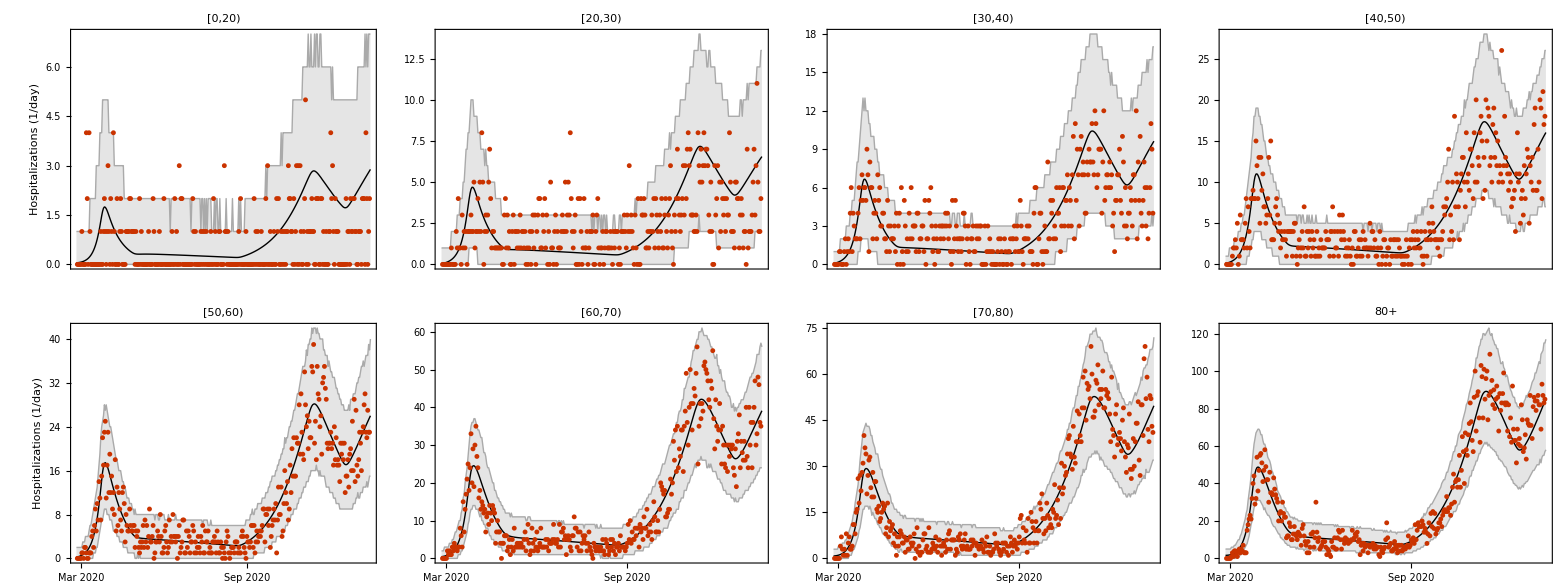

```mathematica
AspRat=0.75; ImSize=250;

DataPlot[AgeGroup_]:=DateListPlot[HospitalisationsData⟦All,AgeGroup⟧,"February 26, 2020",PlotMarkers->{Automatic,5},PlotTheme->"Web",Joined-> False,DateTicksFormat->{"MonthShort","/","YearShort"}]

PlotDataAndModel[Var_,VarSimulated_,tendplot_,onlydata_]:=Grid[Partition[Table[Show[
DateListPlot[{Median[If[k==3,Var⟦1⟧+Var⟦2⟧+Var⟦3⟧,Var⟦k⟧]],(*Quantile[Var⟦k⟧,0.025],Quantile[Var⟦k⟧,0.975],*)Quantile[If[k==3,VarSimulated⟦1⟧+VarSimulated⟦2⟧+VarSimulated⟦3⟧,VarSimulated⟦k⟧],0.025],Quantile[If[k==3,VarSimulated⟦1⟧+VarSimulated⟦2⟧+VarSimulated⟦3⟧,VarSimulated⟦k⟧],0.975]},"February 25, 2020",FrameTicks->{{Automatic,None},{If[k≥ 7,ticks,None],None}},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,If[onlydata==True,Max[Quantile[If[k==3,VarSimulated⟦1⟧+VarSimulated⟦2⟧+VarSimulated⟦3⟧,VarSimulated⟦k⟧],0.975]⟦1;;tenddata⟧],All]}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,14],FrameLabel-> {{If[k==1||k==3||k==7,"Hospitalizations (1/day)",None],None},{None,None}},Filling->{{3->{2}}(*,{5->{4}}*)},PlotStyle->{{Black,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}},PlotLabel->Style[Row[{If[k==3,"[0,20)",AgeLabelShort⟦k⟧]}],Black,14],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{42.5, Automatic}, {Automatic, Automatic}}(*,Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]*)],DataPlot[k](*,PanelLetter[k]*)],{k,Range[3,10]}],4]]

Memory

Print[Style["New hospitalizations (per day) in each age group",24,Blue,"Text"]];
Print[Style["Median trajectories and credible intervals",24,Blue,"Text"]];
Fig3=PlotDataAndModel[HospIncidence,HospIncidenceSimulated,"January 16, 2021",True]

(*Export[StringJoin["Figures//Fig1.pdf"],Fig3] 
Export[StringJoin["Figures//Fig1.eps"],Fig3]*)
(*Table[Export[StringJoin["Figures//Fig3",format⟦i⟧],Fig3],{i,1,Length[format]}];*)
```

New hospitalizations (per day) total

Median trajectories and credible intervals

({2020,2,25} | {2020,2,26} | {2020,2,27} | {2020,2,28} | {2020,2,29} | {2020,3,1} | {2020,3,2} | {2020,3,3} | {2020,3,4} | {2020,3,5} | {2020,3,6} | {2020,3,7} | {2020,3,8} | {2020,3,9} | {2020,3,10} | {2020,3,11} | {2020,3,12} | {2020,3,13} | {2020,3,14} | {2020,3,15} | {2020,3,16} | {2020,3,17} | {2020,3,18} | {2020,3,19} | {2020,3,20} | {2020,3,21} | {2020,3,22} | {2020,3,23} | {2020,3,24} | {2020,3,25} | {2020,3,26} | {2020,3,27} | {2020,3,28} | {2020,3,29} | {2020,3,30} | {2020,3,31} | {2020,4,1} | {2020,4,2} | {2020,4,3} | {2020,4,4} | {2020,4,5} | {2020,4,6} | {2020,4,7} | {2020,4,8} | {2020,4,9} | {2020,4,10} | {2020,4,11} | {2020,4,12} | {2020,4,13} | {2020,4,14} | {2020,4,15} | {2020,4,16} | {2020,4,17} | {2020,4,18} | {2020,4,19} | {2020,4,20} | {2020,4,21} | {2020,4,22} | {2020,4,23} | {2020,4,24} | {2020,4,25} | {2020,4,26} | {2020,4,27} | {2020,4,28} | {2020,4,29} | {2020,4,30} | {2020,5,1} | {2020,5,2} | {2020,5,3} | {2020,5,4} | {2020,5,5} | {2020,5,6} | {2020,5,7} | {2020,5,8} | {2020,5,9} | {2020,5,10} | {2020,5,11} | {2020,5,12} | {2020,5,13} | {2020,5,14} | {2020,5,15} | {2020,5,16} | {2020,5,17} | {2020,5,18} | {2020,5,19} | {2020,5,20} | {2020,5,21} | {2020,5,22} | {2020,5,23} | {2020,5,24} | {2020,5,25} | {2020,5,26} | {2020,5,27} | {2020,5,28} | {2020,5,29} | {2020,5,30} | {2020,5,31} | {2020,6,1} | {2020,6,2} | {2020,6,3} | {2020,6,4} | {2020,6,5} | {2020,6,6} | {2020,6,7} | {2020,6,8} | {2020,6,9} | {2020,6,10} | {2020,6,11} | {2020,6,12} | {2020,6,13} | {2020,6,14} | {2020,6,15} | {2020,6,16} | {2020,6,17} | {2020,6,18} | {2020,6,19} | {2020,6,20} | {2020,6,21} | {2020,6,22} | {2020,6,23} | {2020,6,24} | {2020,6,25} | {2020,6,26} | {2020,6,27} | {2020,6,28} | {2020,6,29} | {2020,6,30} | {2020,7,1} | {2020,7,2} | {2020,7,3} | {2020,7,4} | {2020,7,5} | {2020,7,6} | {2020,7,7} | {2020,7,8} | {2020,7,9} | {2020,7,10} | {2020,7,11} | {2020,7,12} | {2020,7,13} | {2020,7,14} | {2020,7,15} | {2020,7,16} | {2020,7,17} | {2020,7,18} | {2020,7,19} | {2020,7,20} | {2020,7,21} | {2020,7,22} | {2020,7,23} | {2020,7,24} | {2020,7,25} | {2020,7,26} | {2020,7,27} | {2020,7,28} | {2020,7,29} | {2020,7,30} | {2020,7,31} | {2020,8,1} | {2020,8,2} | {2020,8,3} | {2020,8,4} | {2020,8,5} | {2020,8,6} | {2020,8,7} | {2020,8,8} | {2020,8,9} | {2020,8,10} | {2020,8,11} | {2020,8,12} | {2020,8,13} | {2020,8,14} | {2020,8,15} | {2020,8,16} | {2020,8,17} | {2020,8,18} | {2020,8,19} | {2020,8,20} | {2020,8,21} | {2020,8,22} | {2020,8,23} | {2020,8,24} | {2020,8,25} | {2020,8,26} | {2020,8,27} | {2020,8,28} | {2020,8,29} | {2020,8,30} | {2020,8,31} | {2020,9,1} | {2020,9,2} | {2020,9,3} | {2020,9,4} | {2020,9,5} | {2020,9,6} | {2020,9,7} | {2020,9,8} | {2020,9,9} | {2020,9,10} | {2020,9,11} | {2020,9,12} | {2020,9,13} | {2020,9,14} | {2020,9,15} | {2020,9,16} | {2020,9,17} | {2020,9,18} | {2020,9,19} | {2020,9,20} | {2020,9,21} | {2020,9,22} | {2020,9,23} | {2020,9,24} | {2020,9,25} | {2020,9,26} | {2020,9,27} | {2020,9,28} | {2020,9,29} | {2020,9,30} | {2020,10,1} | {2020,10,2} | {2020,10,3} | {2020,10,4} | {2020,10,5} | {2020,10,6} | {2020,10,7} | {2020,10,8} | {2020,10,9} | {2020,10,10} | {2020,10,11} | {2020,10,12} | {2020,10,13} | {2020,10,14} | {2020,10,15} | {2020,10,16} | {2020,10,17} | {2020,10,18} | {2020,10,19} | {2020,10,20} | {2020,10,21} | {2020,10,22} | {2020,10,23} | {2020,10,24} | {2020,10,25} | {2020,10,26} | {2020,10,27} | {2020,10,28} | {2020,10,29} | {2020,10,30} | {2020,10,31} | {2020,11,1} | {2020,11,2} | {2020,11,3} | {2020,11,4} | {2020,11,5} | {2020,11,6} | {2020,11,7} | {2020,11,8} | {2020,11,9} | {2020,11,10} | {2020,11,11} | {2020,11,12} | {2020,11,13} | {2020,11,14} | {2020,11,15} | {2020,11,16} | {2020,11,17} | {2020,11,18} | {2020,11,19} | {2020,11,20} | {2020,11,21} | {2020,11,22} | {2020,11,23} | {2020,11,24} | {2020,11,25} | {2020,11,26} | {2020,11,27} | {2020,11,28} | {2020,11,29} | {2020,11,30} | {2020,12,1} | {2020,12,2} | {2020,12,3} | {2020,12,4} | {2020,12,5} | {2020,12,6} | {2020,12,7} | {2020,12,8} | {2020,12,9} | {2020,12,10} | {2020,12,11} | {2020,12,12} | {2020,12,13} | {2020,12,14} | {2020,12,15} | {2020,12,16} | {2020,12,17} | {2020,12,18} | {2020,12,19} | {2020,12,20} | {2020,12,21} | {2020,12,22} | {2020,12,23} | {2020,12,24} | {2020,12,25} | {2020,12,26} | {2020,12,27} | {2020,12,28} | {2020,12,29} | {2020,12,30} | {2020,12,31} | {2021,1,1} | {2021,1,2} | {2021,1,3} | {2021,1,4} | {2021,1,5} | {2021,1,6} | {2021,1,7} | {2021,1,8} | {2021,1,9} | {2021,1,10} | {2021,1,11} | {2021,1,12} | {2021,1,13} | {2021,1,14} | {2021,1,15} | {2021,1,16}
3.41344 | 3.60679 | 3.83803 | 4.12942 | 4.48476 | 4.92947 | 5.47397 | 6.13052 | 6.92499 | 7.87259 | 8.9897 | 10.3074 | 11.8526 | 13.6568 | 15.7464 | 18.2073 | 21.0659 | 24.3778 | 28.2368 | 32.6933 | 37.8846 | 43.836 | 50.7126 | 58.6323 | 67.7667 | 78.1565 | 89.7579 | 102.196 | 114.965 | 126.792 | 135.822 | 141.264 | 143.532 | 143.539 | 141.989 | 139.262 | 135.921 | 132.03 | 127.841 | 123.443 | 118.997 | 114.473 | 110.021 | 105.57 | 101.166 | 96.822 | 92.5953 | 88.5172 | 84.534 | 80.6672 | 76.9609 | 73.3837 | 69.9206 | 66.6245 | 63.4361 | 60.3981 | 57.5039 | 54.7291 | 52.0666 | 49.522 | 47.1301 | 44.8711 | 42.7826 | 40.8665 | 39.2865 | 37.9691 | 36.9491 | 36.1338 | 35.4827 | 34.9585 | 34.5112 | 34.1271 | 33.7893 | 33.4908 | 33.2189 | 32.9834 | 32.7579 | 32.5498 | 32.36 | 32.1826 | 32.0151 | 31.8604 | 31.7111 | 31.566 | 31.4293 | 31.3003 | 31.181 | 31.0643 | 30.9454 | 30.8264 | 30.7087 | 30.6 | 30.4906 | 30.3852 | 30.2765 | 30.1655 | 30.0559 | 29.9466 | 29.8341 | 29.7277 | 29.6236 | 29.5147 | 29.4047 | 29.2982 | 29.1917 | 29.0798 | 28.9736 | 28.8632 | 28.7527 | 28.6404 | 28.5326 | 28.4223 | 28.3133 | 28.2037 | 28.0943 | 27.9828 | 27.8729 | 27.7579 | 27.644 | 27.5328 | 27.4224 | 27.3104 | 27.1942 | 27.0813 | 26.9697 | 26.8551 | 26.7435 | 26.6268 | 26.5093 | 26.3902 | 26.2726 | 26.1568 | 26.0393 | 25.9233 | 25.8032 | 25.6869 | 25.5632 | 25.4448 | 25.3269 | 25.214 | 25.0989 | 24.9764 | 24.8502 | 24.73 | 24.6086 | 24.4848 | 24.3638 | 24.2376 | 24.121 | 24.0015 | 23.8797 | 23.7603 | 23.6407 | 23.5169 | 23.3955 | 23.2729 | 23.1528 | 23.032 | 22.9128 | 22.7904 | 22.668 | 22.5467 | 22.4277 | 22.3082 | 22.1878 | 22.0687 | 21.9495 | 21.8294 | 21.7135 | 21.5981 | 21.4835 | 21.3684 | 21.2504 | 21.1377 | 21.0345 | 20.9365 | 20.8397 | 20.7678 | 20.732 | 20.7689 | 20.8963 | 21.1454 | 21.4921 | 21.952 | 22.5078 | 23.1111 | 23.77 | 24.4835 | 25.2582 | 26.0723 | 26.9274 | 27.8278 | 28.7664 | 29.7437 | 30.7667 | 31.8429 | 32.9598 | 34.1179 | 35.3095 | 36.5541 | 37.8322 | 39.159 | 40.5376 | 41.9654 | 43.4405 | 44.9757 | 46.5584 | 48.195 | 49.893 | 51.6358 | 53.4526 | 55.3262 | 57.2485 | 59.2417 | 61.2971 | 63.4149 | 65.6133 | 67.8832 | 70.2179 | 72.6204 | 75.1022 | 77.6488 | 80.2801 | 82.9853 | 85.7674 | 88.6408 | 91.6016 | 94.6166 | 97.7445 | 100.963 | 104.259 | 107.635 | 111.112 | 114.672 | 118.334 | 122.082 | 125.937 | 129.852 | 133.867 | 137.98 | 142.21 | 146.536 | 150.971 | 155.481 | 160.087 | 164.799 | 169.616 | 174.488 | 179.456 | 184.549 | 189.724 | 194.924 | 200.192 | 205.502 | 210.886 | 216.171 | 221.485 | 226.714 | 231.833 | 236.549 | 240.693 | 244.28 | 247.054 | 248.704 | 249.526 | 249.63 | 248.939 | 247.866 | 246.331 | 244.374 | 242.153 | 239.715 | 237.112 | 234.379 | 231.501 | 228.545 | 225.474 | 222.338 | 219.108 | 215.878 | 212.599 | 209.302 | 205.98 | 202.671 | 199.374 | 196.013 | 192.689 | 189.396 | 186.094 | 182.807 | 179.516 | 176.322 | 173.098 | 169.988 | 167.006 | 164.171 | 161.645 | 159.698 | 158.353 | 157.727 | 158.092 | 159.044 | 160.441 | 162.318 | 164.491 | 166.978 | 169.557 | 172.269 | 175.123 | 178.059 | 181.128 | 184.293 | 187.507 | 190.749 | 194.093 | 197.468 | 200.82 | 204.241 | 207.751 | 211.174 | 214.6 | 218.065 | 221.559 | 224.863 | 228.231 | 231.556 | 234.989
0 | 0 | 0 | 1 | 1 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 5 | 7 | 8 | 10 | 12 | 14 | 17 | 21 | 25 | 30 | 35 | 42 | 49 | 58 | 68 | 78 | 89 | 100 | 108 | 112 | 115 | 114 | 112 | 111 | 108 | 105 | 100 | 98 | 94 | 89 | 84 | 82 | 78 | 75 | 71 | 66 | 64 | 61 | 57 | 54 | 52 | 49 | 46 | 44 | 42 | 39 | 37 | 34 | 32 | 31 | 28 | 28 | 26 | 25 | 25 | 24 | 23 | 23 | 23 | 22 | 22 | 23 | 22 | 21 | 22 | 21 | 21 | 21 | 21 | 20 | 21 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 19 | 20 | 20 | 19 | 20 | 19 | 19 | 19 | 19 | 19 | 19 | 19 | 19 | 19 | 18 | 19 | 18 | 19 | 19 | 18 | 18 | 18 | 18 | 18 | 17 | 18 | 18 | 17 | 17 | 17 | 17 | 17 | 17 | 17 | 17 | 17 | 17 | 16 | 17 | 16 | 16 | 15 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 15 | 16 | 15 | 15 | 15 | 15 | 15 | 15 | 14 | 15 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 13 | 13 | 13 | 13 | 13 | 13 | 12 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 13 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 13 | 13 | 14 | 14 | 15 | 15 | 16 | 17 | 18 | 18 | 19 | 19 | 21 | 21 | 22 | 23 | 25 | 25 | 27 | 28 | 29 | 29 | 31 | 33 | 34 | 34 | 37 | 39 | 40 | 41 | 43 | 45 | 46 | 48 | 50 | 52 | 54 | 56 | 59 | 62 | 64 | 65 | 67 | 71 | 73 | 76 | 77 | 82 | 84 | 87 | 91 | 93 | 96 | 100 | 102 | 107 | 110 | 114 | 117 | 120 | 126 | 129 | 133 | 135 | 142 | 146 | 149 | 154 | 160 | 162 | 169 | 173 | 175 | 179 | 187 | 192 | 194 | 200 | 202 | 204 | 205 | 205 | 207 | 206 | 204 | 203 | 203 | 200 | 198 | 195 | 192 | 190 | 186 | 186 | 182 | 180 | 176 | 172 | 171 | 167 | 166 | 164 | 159 | 157 | 153 | 152 | 147 | 145 | 141 | 140 | 136 | 134 | 132 | 129 | 129 | 127 | 128 | 125 | 127 | 129 | 129 | 131 | 135 | 135 | 139 | 141 | 146 | 146 | 149 | 152 | 155 | 158 | 161 | 163 | 166 | 171 | 173 | 177 | 177 | 180 | 183 | 187 | 188 | 195
8 | 8 | 8 | 9 | 9 | 10 | 11 | 12 | 13 | 14 | 16 | 17 | 19 | 22 | 25 | 28 | 31 | 36 | 40 | 46 | 52 | 58 | 67 | 76 | 87 | 99 | 112 | 127 | 144 | 157 | 166 | 172 | 175 | 175 | 174 | 169 | 164 | 164 | 157 | 150 | 148 | 142 | 137 | 131 | 126 | 121 | 117 | 110 | 106 | 103 | 99 | 94 | 89 | 85 | 81 | 79 | 75 | 72 | 70 | 67 | 63 | 60 | 58 | 56 | 53 | 52 | 51 | 50 | 49 | 48 | 48 | 47 | 47 | 46 | 46 | 46 | 46 | 45 | 45 | 44 | 44 | 44 | 44 | 44 | 44 | 44 | 43 | 43 | 43 | 43 | 43 | 43 | 43 | 43 | 43 | 42 | 42 | 42 | 42 | 42 | 42 | 42 | 41 | 42 | 40 | 41 | 41 | 40 | 40 | 41 | 40 | 40 | 40 | 39 | 40 | 39 | 40 | 39 | 39 | 38 | 38 | 39 | 38 | 39 | 39 | 38 | 38 | 38 | 37 | 37 | 37 | 37 | 37 | 37 | 37 | 37 | 36 | 36 | 36 | 37 | 37 | 35 | 36 | 36 | 35 | 35 | 35 | 35 | 35 | 35 | 35 | 35 | 34 | 34 | 34 | 34 | 34 | 33 | 34 | 33 | 33 | 33 | 33 | 33 | 33 | 32 | 32 | 32 | 32 | 31 | 31 | 31 | 31 | 31 | 31 | 31 | 30 | 30 | 31 | 31 | 32 | 31 | 32 | 33 | 33 | 34 | 34 | 36 | 36 | 37 | 38 | 39 | 41 | 42 | 43 | 45 | 45 | 46 | 48 | 50 | 51 | 53 | 56 | 57 | 58 | 60 | 62 | 64 | 67 | 68 | 70 | 72 | 74 | 77 | 79 | 80 | 84 | 87 | 89 | 92 | 96 | 99 | 101 | 104 | 107 | 111 | 113 | 118 | 121 | 126 | 128 | 132 | 138 | 140 | 145 | 148 | 155 | 159 | 163 | 168 | 172 | 178 | 182 | 189 | 194 | 198 | 204 | 210 | 217 | 221 | 226 | 234 | 240 | 245 | 251 | 260 | 264 | 269 | 277 | 283 | 287 | 291 | 294 | 295 | 295 | 296 | 298 | 296 | 294 | 289 | 289 | 285 | 283 | 280 | 275 | 274 | 270 | 265 | 264 | 256 | 254 | 249 | 249 | 243 | 239 | 234 | 232 | 228 | 223 | 220 | 214 | 212 | 206 | 204 | 203 | 198 | 196 | 195 | 192 | 190 | 192 | 192 | 194 | 197 | 201 | 202 | 206 | 208 | 211 | 215 | 216 | 221 | 224 | 229 | 234 | 238 | 240 | 244 | 248 | 254 | 257 | 262 | 264 | 270 | 276 | 278 | 283)

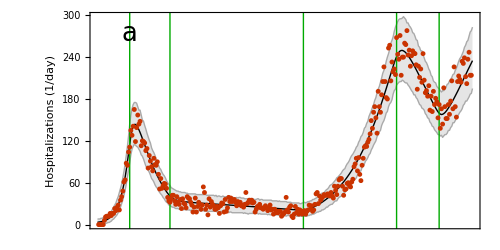

```mathematica
Print[Style["New hospitalizations (per day) total",24,Blue,"Text"]];
Print[Style["Median trajectories and credible intervals",24,Blue,"Text"]];

AspRat=0.5; ImSize=500;
tickValues=DateRange[{2020,3,1},{2022,1,1},{1,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

DataPlotAll:=DateListPlot[Total[Transpose[HospitalisationsData]],"February 26, 2020",PlotMarkers->{Automatic,5},PlotTheme->"Web",Joined-> False,DateTicksFormat->{"MonthShort","/","YearShort"}];

indexlist ={20,22,24,26,28};
TransitionDates=Table[DayPlus[{2020,02,25}, IntegerPart[Median[EstimatesData⟦All,index⟧]]],{index,indexlist}];

PlotTotalDataAndModel[Var_,VarSimulated_,tendplot_,onlydata_,plotlabel_]:=Show[DateListPlot[{Median[Total[Var]],(*Quantile[Total[Var],0.025],Quantile[Total[Var],0.975],*)Quantile[Total[VarSimulated],0.025],Quantile[Total[VarSimulated],0.975]},"February 25, 2020",FrameTicks->{{Automatic,None},{None(*ticks*),None}},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,If[onlydata==True,Max[Quantile[Total[VarSimulated],0.975]⟦1;;tenddata⟧],All]}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{"Hospitalizations (1/day)",None},{None,None}},Filling->{{3->{2}}(*,{5->{4}}*)},PlotStyle->{{Black,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}(*,{Lighter[Gray],Thin},{Lighter[Gray],Thin}*)},PlotLabel->(*Style[Row[{plotlabel}],Black,17]*)None,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},Prolog->{Join[{Directive[{Darker[Green]}]},Table[InfiniteLine[{TransitionDates⟦i⟧,0},{0,1}],{i,1,Length[TransitionDates]}]](*,Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]*)},ImagePadding->{{52.5, Automatic}, {Automatic, Automatic}}],DataPlotAll(*,PanelLetter[k]*),Graphics[Text[StyleForm["a",FontSize->26],Scaled[{0.1,0.9}]]]];

{DateRange[{2020,02,25},{2021,1,16},{1,"Day"}],Median[Total[HospIncidence]],Quantile[Total[HospIncidenceSimulated],0.025],Quantile[Total[HospIncidenceSimulated],0.975]}//MatrixForm

Fig4a=PlotTotalDataAndModel[HospIncidence,HospIncidenceSimulated,"January 16, 2021",True,"Model fit"]
```

19.5306

14.931

24.7718

({2020,2,25} | {2020,2,26} | {2020,2,27} | {2020,2,28} | {2020,2,29} | {2020,3,1} | {2020,3,2} | {2020,3,3} | {2020,3,4} | {2020,3,5} | {2020,3,6} | {2020,3,7} | {2020,3,8} | {2020,3,9} | {2020,3,10} | {2020,3,11} | {2020,3,12} | {2020,3,13} | {2020,3,14} | {2020,3,15} | {2020,3,16} | {2020,3,17} | {2020,3,18} | {2020,3,19} | {2020,3,20} | {2020,3,21} | {2020,3,22} | {2020,3,23} | {2020,3,24} | {2020,3,25} | {2020,3,26} | {2020,3,27} | {2020,3,28} | {2020,3,29} | {2020,3,30} | {2020,3,31} | {2020,4,1} | {2020,4,2} | {2020,4,3} | {2020,4,4} | {2020,4,5} | {2020,4,6} | {2020,4,7} | {2020,4,8} | {2020,4,9} | {2020,4,10} | {2020,4,11} | {2020,4,12} | {2020,4,13} | {2020,4,14} | {2020,4,15} | {2020,4,16} | {2020,4,17} | {2020,4,18} | {2020,4,19} | {2020,4,20} | {2020,4,21} | {2020,4,22} | {2020,4,23} | {2020,4,24} | {2020,4,25} | {2020,4,26} | {2020,4,27} | {2020,4,28} | {2020,4,29} | {2020,4,30} | {2020,5,1} | {2020,5,2} | {2020,5,3} | {2020,5,4} | {2020,5,5} | {2020,5,6} | {2020,5,7} | {2020,5,8} | {2020,5,9} | {2020,5,10} | {2020,5,11} | {2020,5,12} | {2020,5,13} | {2020,5,14} | {2020,5,15} | {2020,5,16} | {2020,5,17} | {2020,5,18} | {2020,5,19} | {2020,5,20} | {2020,5,21} | {2020,5,22} | {2020,5,23} | {2020,5,24} | {2020,5,25} | {2020,5,26} | {2020,5,27} | {2020,5,28} | {2020,5,29} | {2020,5,30} | {2020,5,31} | {2020,6,1} | {2020,6,2} | {2020,6,3} | {2020,6,4} | {2020,6,5} | {2020,6,6} | {2020,6,7} | {2020,6,8} | {2020,6,9} | {2020,6,10} | {2020,6,11} | {2020,6,12} | {2020,6,13} | {2020,6,14} | {2020,6,15} | {2020,6,16} | {2020,6,17} | {2020,6,18} | {2020,6,19} | {2020,6,20} | {2020,6,21} | {2020,6,22} | {2020,6,23} | {2020,6,24} | {2020,6,25} | {2020,6,26} | {2020,6,27} | {2020,6,28} | {2020,6,29} | {2020,6,30} | {2020,7,1} | {2020,7,2} | {2020,7,3} | {2020,7,4} | {2020,7,5} | {2020,7,6} | {2020,7,7} | {2020,7,8} | {2020,7,9} | {2020,7,10} | {2020,7,11} | {2020,7,12} | {2020,7,13} | {2020,7,14} | {2020,7,15} | {2020,7,16} | {2020,7,17} | {2020,7,18} | {2020,7,19} | {2020,7,20} | {2020,7,21} | {2020,7,22} | {2020,7,23} | {2020,7,24} | {2020,7,25} | {2020,7,26} | {2020,7,27} | {2020,7,28} | {2020,7,29} | {2020,7,30} | {2020,7,31} | {2020,8,1} | {2020,8,2} | {2020,8,3} | {2020,8,4} | {2020,8,5} | {2020,8,6} | {2020,8,7} | {2020,8,8} | {2020,8,9} | {2020,8,10} | {2020,8,11} | {2020,8,12} | {2020,8,13} | {2020,8,14} | {2020,8,15} | {2020,8,16} | {2020,8,17} | {2020,8,18} | {2020,8,19} | {2020,8,20} | {2020,8,21} | {2020,8,22} | {2020,8,23} | {2020,8,24} | {2020,8,25} | {2020,8,26} | {2020,8,27} | {2020,8,28} | {2020,8,29} | {2020,8,30} | {2020,8,31} | {2020,9,1} | {2020,9,2} | {2020,9,3} | {2020,9,4} | {2020,9,5} | {2020,9,6} | {2020,9,7} | {2020,9,8} | {2020,9,9} | {2020,9,10} | {2020,9,11} | {2020,9,12} | {2020,9,13} | {2020,9,14} | {2020,9,15} | {2020,9,16} | {2020,9,17} | {2020,9,18} | {2020,9,19} | {2020,9,20} | {2020,9,21} | {2020,9,22} | {2020,9,23} | {2020,9,24} | {2020,9,25} | {2020,9,26} | {2020,9,27} | {2020,9,28} | {2020,9,29} | {2020,9,30} | {2020,10,1} | {2020,10,2} | {2020,10,3} | {2020,10,4} | {2020,10,5} | {2020,10,6} | {2020,10,7} | {2020,10,8} | {2020,10,9} | {2020,10,10} | {2020,10,11} | {2020,10,12} | {2020,10,13} | {2020,10,14} | {2020,10,15} | {2020,10,16} | {2020,10,17} | {2020,10,18} | {2020,10,19} | {2020,10,20} | {2020,10,21} | {2020,10,22} | {2020,10,23} | {2020,10,24} | {2020,10,25} | {2020,10,26} | {2020,10,27} | {2020,10,28} | {2020,10,29} | {2020,10,30} | {2020,10,31} | {2020,11,1} | {2020,11,2} | {2020,11,3} | {2020,11,4} | {2020,11,5} | {2020,11,6} | {2020,11,7} | {2020,11,8} | {2020,11,9} | {2020,11,10} | {2020,11,11} | {2020,11,12} | {2020,11,13} | {2020,11,14} | {2020,11,15} | {2020,11,16} | {2020,11,17} | {2020,11,18} | {2020,11,19} | {2020,11,20} | {2020,11,21} | {2020,11,22} | {2020,11,23} | {2020,11,24} | {2020,11,25} | {2020,11,26} | {2020,11,27} | {2020,11,28} | {2020,11,29} | {2020,11,30} | {2020,12,1} | {2020,12,2} | {2020,12,3} | {2020,12,4} | {2020,12,5} | {2020,12,6} | {2020,12,7} | {2020,12,8} | {2020,12,9} | {2020,12,10} | {2020,12,11} | {2020,12,12} | {2020,12,13} | {2020,12,14} | {2020,12,15} | {2020,12,16} | {2020,12,17} | {2020,12,18} | {2020,12,19} | {2020,12,20} | {2020,12,21} | {2020,12,22} | {2020,12,23} | {2020,12,24} | {2020,12,25} | {2020,12,26} | {2020,12,27} | {2020,12,28} | {2020,12,29} | {2020,12,30} | {2020,12,31} | {2021,1,1} | {2021,1,2} | {2021,1,3} | {2021,1,4} | {2021,1,5} | {2021,1,6} | {2021,1,7} | {2021,1,8} | {2021,1,9} | {2021,1,10} | {2021,1,11} | {2021,1,12} | {2021,1,13} | {2021,1,14} | {2021,1,15} | {2021,1,16}
0.012127 | 0.0157027 | 0.019747 | 0.0243476 | 0.029666 | 0.0358169 | 0.0429274 | 0.0511562 | 0.0607255 | 0.0718134 | 0.084607 | 0.0995571 | 0.116906 | 0.136822 | 0.160093 | 0.186968 | 0.218317 | 0.254765 | 0.296501 | 0.345555 | 0.402005 | 0.467421 | 0.542854 | 0.628935 | 0.727866 | 0.84016 | 0.963835 | 1.09611 | 1.23039 | 1.35503 | 1.4595 | 1.55201 | 1.63338 | 1.71315 | 1.79221 | 1.86292 | 1.92916 | 1.99471 | 2.05674 | 2.11395 | 2.1696 | 2.2212 | 2.27143 | 2.31812 | 2.36311 | 2.40598 | 2.44723 | 2.48614 | 2.52237 | 2.55683 | 2.59091 | 2.62203 | 2.65198 | 2.67997 | 2.70655 | 2.73102 | 2.75576 | 2.77919 | 2.80148 | 2.822 | 2.84184 | 2.86141 | 2.8809 | 2.90028 | 2.92022 | 2.94131 | 2.96147 | 2.98204 | 3.00291 | 3.02388 | 3.04398 | 3.06445 | 3.08534 | 3.10589 | 3.1255 | 3.14548 | 3.16565 | 3.18563 | 3.20569 | 3.22601 | 3.24598 | 3.26603 | 3.2861 | 3.3059 | 3.32551 | 3.34529 | 3.36506 | 3.38452 | 3.40363 | 3.4228 | 3.44215 | 3.46144 | 3.48098 | 3.50041 | 3.51967 | 3.53866 | 3.55799 | 3.57686 | 3.59597 | 3.61503 | 3.63402 | 3.65294 | 3.67167 | 3.69035 | 3.70925 | 3.72807 | 3.74633 | 3.76435 | 3.78208 | 3.79975 | 3.81761 | 3.83532 | 3.85291 | 3.87035 | 3.88764 | 3.90494 | 3.92249 | 3.93997 | 3.95736 | 3.97467 | 3.99202 | 4.00916 | 4.02622 | 4.04324 | 4.06036 | 4.07739 | 4.09424 | 4.11109 | 4.12801 | 4.14481 | 4.16147 | 4.17787 | 4.19419 | 4.21065 | 4.22708 | 4.24344 | 4.25964 | 4.2757 | 4.29163 | 4.30727 | 4.32276 | 4.33851 | 4.35397 | 4.36939 | 4.38492 | 4.4005 | 4.41601 | 4.43144 | 4.44661 | 4.46185 | 4.47709 | 4.49142 | 4.50595 | 4.5204 | 4.53458 | 4.54868 | 4.56269 | 4.57663 | 4.591 | 4.60539 | 4.6198 | 4.63388 | 4.6477 | 4.66145 | 4.67511 | 4.6887 | 4.70221 | 4.71552 | 4.72874 | 4.74199 | 4.75561 | 4.76905 | 4.78246 | 4.79538 | 4.80814 | 4.82086 | 4.83379 | 4.84696 | 4.86054 | 4.87563 | 4.89189 | 4.90754 | 4.92349 | 4.94052 | 4.95827 | 4.97676 | 4.99604 | 5.01596 | 5.03702 | 5.05774 | 5.07878 | 5.101 | 5.12411 | 5.14867 | 5.17398 | 5.20019 | 5.22697 | 5.25473 | 5.28408 | 5.31387 | 5.34426 | 5.37625 | 5.40997 | 5.44583 | 5.48317 | 5.52085 | 5.55906 | 5.59868 | 5.64007 | 5.68243 | 5.7259 | 5.77085 | 5.81725 | 5.8656 | 5.91586 | 5.96699 | 6.01982 | 6.07466 | 6.13126 | 6.18981 | 6.25122 | 6.31526 | 6.38072 | 6.44759 | 6.51635 | 6.58889 | 6.66437 | 6.74061 | 6.82021 | 6.90166 | 6.98499 | 7.07272 | 7.16157 | 7.2536 | 7.34919 | 7.44669 | 7.54727 | 7.65123 | 7.75715 | 7.8665 | 7.97982 | 8.09472 | 8.21619 | 8.33936 | 8.46639 | 8.59723 | 8.7305 | 8.8648 | 9.00693 | 9.15024 | 9.29904 | 9.45482 | 9.61044 | 9.77016 | 9.93207 | 10.0962 | 10.2635 | 10.4316 | 10.6039 | 10.7768 | 10.9446 | 11.1155 | 11.2817 | 11.4391 | 11.5996 | 11.7548 | 11.9088 | 12.0558 | 12.2 | 12.3505 | 12.4987 | 12.6429 | 12.7828 | 12.919 | 13.0549 | 13.1873 | 13.3166 | 13.4449 | 13.5712 | 13.6962 | 13.8195 | 13.9389 | 14.0583 | 14.1735 | 14.289 | 14.3976 | 14.5078 | 14.6143 | 14.7161 | 14.8161 | 14.9144 | 15.0124 | 15.1097 | 15.2062 | 15.3026 | 15.4007 | 15.4998 | 15.6024 | 15.7051 | 15.8068 | 15.9102 | 16.0207 | 16.1324 | 16.2483 | 16.369 | 16.491 | 16.6137 | 16.7382 | 16.8647 | 16.9945 | 17.1266 | 17.2606 | 17.3958 | 17.536 | 17.6822 | 17.8205 | 17.9601 | 18.1041 | 18.2553 | 18.4112 | 18.5655 | 18.7267 | 18.8827 | 19.0389 | 19.2014 | 19.3716 | 19.5306
0.0183398 | 0.0235189 | 0.0293146 | 0.0357938 | 0.0432343 | 0.051722 | 0.0614623 | 0.0728477 | 0.085994 | 0.100946 | 0.118681 | 0.138928 | 0.162187 | 0.18922 | 0.220229 | 0.255767 | 0.29847 | 0.347125 | 0.403979 | 0.468321 | 0.543552 | 0.631136 | 0.729936 | 0.845254 | 0.97356 | 1.12183 | 1.2843 | 1.45955 | 1.63989 | 1.79277 | 1.92417 | 2.03354 | 2.13581 | 2.22951 | 2.31949 | 2.40555 | 2.49107 | 2.57407 | 2.64274 | 2.71539 | 2.78261 | 2.84659 | 2.90907 | 2.96606 | 3.02178 | 3.07731 | 3.12852 | 3.17671 | 3.22263 | 3.26638 | 3.30808 | 3.34781 | 3.3833 | 3.41555 | 3.44617 | 3.47523 | 3.50282 | 3.529 | 3.55501 | 3.58195 | 3.60968 | 3.63459 | 3.65885 | 3.68355 | 3.70964 | 3.73621 | 3.76272 | 3.78902 | 3.81517 | 3.84081 | 3.8658 | 3.89061 | 3.91674 | 3.94147 | 3.96615 | 3.99076 | 4.01531 | 4.03995 | 4.06588 | 4.09172 | 4.11748 | 4.14315 | 4.16873 | 4.19422 | 4.21963 | 4.24475 | 4.26851 | 4.29218 | 4.31577 | 4.33939 | 4.36433 | 4.38865 | 4.41217 | 4.43601 | 4.46021 | 4.4843 | 4.5083 | 4.5322 | 4.55599 | 4.57969 | 4.60328 | 4.62655 | 4.65015 | 4.67343 | 4.6966 | 4.71909 | 4.74128 | 4.76339 | 4.78542 | 4.80737 | 4.82923 | 4.85101 | 4.8727 | 4.8943 | 4.91583 | 4.93726 | 4.95861 | 4.98138 | 5.00425 | 5.02706 | 5.04979 | 5.07245 | 5.09503 | 5.11662 | 5.13764 | 5.15855 | 5.17935 | 5.20004 | 5.22062 | 5.24108 | 5.26187 | 5.28294 | 5.30391 | 5.32478 | 5.34555 | 5.36622 | 5.38678 | 5.40725 | 5.42762 | 5.44789 | 5.46775 | 5.48679 | 5.50573 | 5.52457 | 5.5433 | 5.56192 | 5.58044 | 5.59885 | 5.61716 | 5.63536 | 5.65346 | 5.67145 | 5.68933 | 5.70712 | 5.72479 | 5.74236 | 5.75983 | 5.77719 | 5.79445 | 5.81161 | 5.82951 | 5.84731 | 5.865 | 5.88258 | 5.90007 | 5.91744 | 5.93472 | 5.95189 | 5.96895 | 5.98591 | 6.00277 | 6.01952 | 6.03617 | 6.05272 | 6.06916 | 6.08552 | 6.10179 | 6.11797 | 6.13439 | 6.15234 | 6.17072 | 6.18962 | 6.20913 | 6.22933 | 6.25029 | 6.27239 | 6.29696 | 6.32243 | 6.34883 | 6.3762 | 6.40457 | 6.43398 | 6.46447 | 6.49607 | 6.52882 | 6.56277 | 6.59795 | 6.63383 | 6.66941 | 6.70787 | 6.74887 | 6.79131 | 6.83522 | 6.88065 | 6.92765 | 6.97477 | 7.02326 | 7.07496 | 7.129 | 7.18493 | 7.24282 | 7.30272 | 7.36471 | 7.42884 | 7.49346 | 7.55809 | 7.62501 | 7.69429 | 7.76601 | 7.84023 | 7.91702 | 7.99646 | 8.07861 | 8.16356 | 8.25297 | 8.34681 | 8.44364 | 8.54353 | 8.64656 | 8.7528 | 8.86231 | 8.97516 | 9.09144 | 9.21015 | 9.33102 | 9.45545 | 9.58242 | 9.71285 | 9.85078 | 9.9901 | 10.1333 | 10.2804 | 10.4314 | 10.5862 | 10.7446 | 10.9071 | 11.0762 | 11.2476 | 11.4253 | 11.6088 | 11.7978 | 11.987 | 12.1832 | 12.3848 | 12.5891 | 12.7987 | 13.0129 | 13.2314 | 13.4543 | 13.6811 | 13.8935 | 14.1055 | 14.3066 | 14.5158 | 14.7088 | 14.9136 | 15.1149 | 15.3059 | 15.4938 | 15.6788 | 15.8608 | 16.0373 | 16.2099 | 16.3832 | 16.5581 | 16.7274 | 16.8919 | 17.0536 | 17.2124 | 17.3682 | 17.5212 | 17.6633 | 17.7989 | 17.9317 | 18.0616 | 18.1889 | 18.3177 | 18.4543 | 18.5883 | 18.7199 | 18.849 | 18.9692 | 19.0932 | 19.2172 | 19.3394 | 19.4585 | 19.5742 | 19.6901 | 19.8148 | 19.9548 | 20.0979 | 20.2436 | 20.3918 | 20.5424 | 20.6954 | 20.8507 | 21.0083 | 21.1681 | 21.3302 | 21.4944 | 21.6608 | 21.8293 | 22.0039 | 22.1869 | 22.3732 | 22.563 | 22.7443 | 22.9331 | 23.1288 | 23.3273 | 23.5167 | 23.7082 | 23.9112 | 24.1223 | 24.3382 | 24.5679 | 24.7868
0.00790128 | 0.0103204 | 0.0130942 | 0.0162958 | 0.0200937 | 0.0244085 | 0.0294119 | 0.0352531 | 0.0420703 | 0.0500328 | 0.0592089 | 0.0701874 | 0.0827184 | 0.0972558 | 0.114403 | 0.134161 | 0.157692 | 0.184751 | 0.215959 | 0.25265 | 0.293919 | 0.342151 | 0.396868 | 0.460856 | 0.534913 | 0.618907 | 0.710916 | 0.815546 | 0.925224 | 1.01861 | 1.09673 | 1.16727 | 1.2344 | 1.29567 | 1.35294 | 1.4097 | 1.46647 | 1.51424 | 1.56262 | 1.61044 | 1.65566 | 1.69597 | 1.73439 | 1.771 | 1.80589 | 1.83911 | 1.87076 | 1.9009 | 1.92988 | 1.95913 | 1.98415 | 2.0079 | 2.03131 | 2.05377 | 2.07514 | 2.09549 | 2.11486 | 2.13329 | 2.15085 | 2.16775 | 2.18448 | 2.2004 | 2.21658 | 2.23296 | 2.25021 | 2.2679 | 2.28422 | 2.30033 | 2.31644 | 2.33251 | 2.34854 | 2.36453 | 2.38046 | 2.39634 | 2.41217 | 2.42795 | 2.44368 | 2.45936 | 2.47498 | 2.49056 | 2.50609 | 2.52136 | 2.53656 | 2.55173 | 2.56687 | 2.58198 | 2.59705 | 2.6121 | 2.6271 | 2.64208 | 2.65702 | 2.67192 | 2.68679 | 2.70163 | 2.71643 | 2.73119 | 2.74592 | 2.76062 | 2.77527 | 2.78982 | 2.80409 | 2.81824 | 2.83214 | 2.84598 | 2.85976 | 2.87348 | 2.88713 | 2.90073 | 2.91426 | 2.92773 | 2.94114 | 2.95449 | 2.96778 | 2.98101 | 2.99417 | 3.00727 | 3.02031 | 3.03329 | 3.04621 | 3.05906 | 3.07242 | 3.08601 | 3.0987 | 3.11099 | 3.12323 | 3.13541 | 3.14755 | 3.15968 | 3.17197 | 3.18421 | 3.19639 | 3.2085 | 3.22055 | 3.23254 | 3.24447 | 3.25634 | 3.26814 | 3.27996 | 3.29184 | 3.30365 | 3.3154 | 3.32709 | 3.33872 | 3.35029 | 3.36179 | 3.37323 | 3.38461 | 3.39593 | 3.40719 | 3.41838 | 3.42952 | 3.44059 | 3.45161 | 3.46256 | 3.47345 | 3.48428 | 3.49505 | 3.50576 | 3.51641 | 3.527 | 3.53753 | 3.548 | 3.55841 | 3.56876 | 3.57905 | 3.58929 | 3.59946 | 3.60957 | 3.61963 | 3.62963 | 3.63957 | 3.64945 | 3.65929 | 3.6691 | 3.67891 | 3.68875 | 3.69877 | 3.70913 | 3.72001 | 3.73152 | 3.74364 | 3.7563 | 3.76943 | 3.78304 | 3.79714 | 3.81173 | 3.82683 | 3.84247 | 3.85868 | 3.87546 | 3.89284 | 3.91085 | 3.9295 | 3.94882 | 3.96883 | 3.98955 | 4.01102 | 4.03325 | 4.05626 | 4.0801 | 4.10478 | 4.13033 | 4.15679 | 4.18419 | 4.21254 | 4.24189 | 4.27183 | 4.30149 | 4.33218 | 4.36393 | 4.39678 | 4.43076 | 4.46591 | 4.50226 | 4.53986 | 4.57875 | 4.61895 | 4.66052 | 4.70349 | 4.74791 | 4.79382 | 4.84126 | 4.89029 | 4.94094 | 4.99326 | 5.0473 | 5.10311 | 5.16075 | 5.22025 | 5.28167 | 5.34507 | 5.41049 | 5.47799 | 5.54762 | 5.61943 | 5.6931 | 5.76867 | 5.84656 | 5.92682 | 6.00951 | 6.09469 | 6.18241 | 6.27275 | 6.36574 | 6.46146 | 6.55881 | 6.65947 | 6.76468 | 6.87075 | 6.97979 | 7.09184 | 7.20754 | 7.32943 | 7.45134 | 7.57558 | 7.7028 | 7.83495 | 7.97063 | 8.10325 | 8.23576 | 8.36529 | 8.49564 | 8.61917 | 8.74309 | 8.86352 | 8.98204 | 9.0988 | 9.21383 | 9.32713 | 9.43872 | 9.54862 | 9.65681 | 9.76331 | 9.86811 | 9.97123 | 10.0727 | 10.1724 | 10.2705 | 10.367 | 10.4617 | 10.5549 | 10.6465 | 10.7364 | 10.8244 | 10.9102 | 10.9945 | 11.0804 | 11.1626 | 11.2432 | 11.3223 | 11.4 | 11.4762 | 11.5509 | 11.6269 | 11.7034 | 11.7798 | 11.8498 | 11.9232 | 12.0021 | 12.0845 | 12.1685 | 12.2538 | 12.3405 | 12.4288 | 12.5187 | 12.6104 | 12.7037 | 12.7988 | 12.8956 | 12.9943 | 13.0946 | 13.1968 | 13.3002 | 13.4038 | 13.5091 | 13.6159 | 13.7243 | 13.8343 | 13.9484 | 14.0659 | 14.185 | 14.3055 | 14.4276 | 14.5513 | 14.6807 | 14.816 | 14.945)

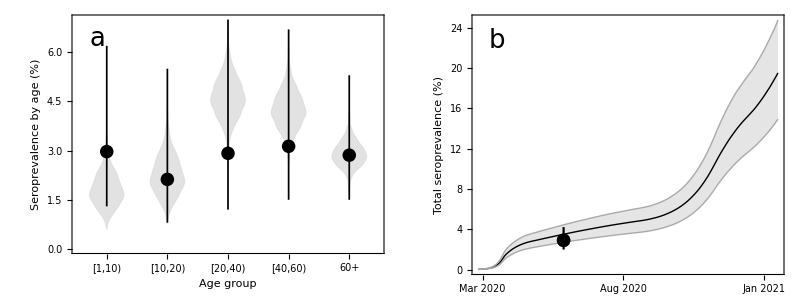

```mathematica
MeanSero=2.9;
LowMeanSero=2.0;
HighMeanSero=4.2;

SeroPosModel=100-100Total[Susceptible]/NNtot/.Demography;

Last[Median[SeroPosModel]]
Last[Quantile[SeroPosModel,0.025]]
Last[Quantile[SeroPosModel,0.975]]

PlotTotalDataAndModel[Var_,tendplot_,onlydata_,plotlabel_,color_,panel_,yaxislabel_]:=Show[DateListPlot[{100-100 Median[Total[Var]]/NNtot/.Demography,100-100 Quantile[Total[Var],0.025]/NNtot/.Demography,100-100 Quantile[Total[Var],0.975]/NNtot/.Demography},"February 25, 2020",FrameTicks->{{Automatic,None},{ticks,None}},AspectRatio->0.75,ImageSize->500,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,All}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],FrameLabel-> {{yaxislabel,None},{None,None}},Filling->{{3->{2}}(*,{5->{4}}*)},PlotStyle->{{color,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}(*,{Lighter[Gray],Thin},{Lighter[Gray],Thin}*)},(*PlotLabel->Style[Row[{plotlabel}],Black,17],*)FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}(*,Prolog->{Join[{Directive[{Darker[Green]}]},Table[InfiniteLine[{TransitionDates⟦i⟧,0},{0,1}],{i,1,Length[TransitionDates]}]],Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]}*),ImagePadding->{{44, Automatic}, {65, 7.5}}](*,PanelLetter[k]*),Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.08,0.9}]]],ErrorListPlot[{{{AbsoluteTime[{2020,05,28}],MeanSero},ErrorBar[{LowMeanSero-MeanSero,HighMeanSero-MeanSero}]}},PlotRange->All,PlotStyle->{Black,Thickness[0.0025]},PlotTheme-> "Web",Frame-> {{True,False},{True,False}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},AspectRatio->0.75,ImageSize->500,FrameStyle->Directive[Black,17],FrameLabel-> {{"Seroprevalence (%)",None},{None,None}},PlotRangePadding->None]];

fig4b=PlotTotalDataAndModel[Susceptible,"January 16, 2021",True,"Model fit",Black,"b","Total seroprevalence (%)"];

{DateRange[{2020,02,25},{2021,1,16},{1,"Day"}],100-100 Median[Total[Susceptible]]/NNtot/.Demography,100-100 Quantile[Total[Susceptible],0.025]/NNtot/.Demography,100-100 Quantile[Total[Susceptible],0.975]/NNtot/.Demography}//MatrixForm

fig4=Grid[{{fig4a,fig4b}}]

(* Table[Export[StringJoin["Figures//Fig2",format⟦i⟧],fig4],{i,1,Length[format]}]; *)
```

## Calculating average contact rate

```mathematica
Subscript[t, start]=0;
Subscript[t, end]=tenddata;
Subscript[t, step]=14;

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=40;
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

ParametersAllNoVaccination=Table[ParametersNoVaccination[i],{i,1,nSamples,stepSamples}];

AverageContactRateSampleAtTimet[sample_,tcont_]:=Sum[(Table[Total[Simplify[Simplify[ContactMatrix[tcont]/.ParametersAllNoVaccination⟦sample⟧]/.{Subscript[c, {k,l}]-> ContactDataPTBefore10Vespignani,Subscript[d, {k,l}]->ContactDataPTAfter10Vespignani }]⟦g,All⟧],{g,AgeGroups}])⟦k⟧ DemographyData10⟦k⟧/Total[DemographyData10],{k,AgeGroups}];

(*TrajectoriesContacts=Table[Transpose[{Table[t,{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],Table[AverageContactRateSampleAtTimet[i,t],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}]}],{i,1,Length[ListSamples]}]*)

TrajectoriesContacts=Table[Table[AverageContactRateSampleAtTimet[i,t],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}];

Export["MathematicaFiles//ModelFit//TrajectoriesContacts.txt",TrajectoriesContacts,"Table"]
(*TrajectoriesContacts=Import["MathematicaFiles//ModelFit//TrajectoriesContacts.txt","Table"]*)

(*CalculateContactsAgeGroups[Matrix10_]:=Table[Total[Matrix10⟦k,All⟧],{k,AgeGroups}];
CalculateAverageContactRate[Demography_,ContactsAgeGroups_]:=Sum[ContactsAgeGroups⟦k⟧ Demography⟦k⟧/Total[Demography],{k,AgeGroups}];*)
```

MathematicaFiles//ModelFit//TrajectoriesContacts.txt

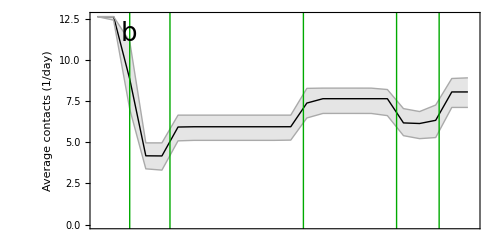

({2020,2,25} | {2020,3,10} | {2020,3,24} | {2020,4,7} | {2020,4,21} | {2020,5,5} | {2020,5,19} | {2020,6,2} | {2020,6,16} | {2020,6,30} | {2020,7,14} | {2020,7,28} | {2020,8,11} | {2020,8,25} | {2020,9,8} | {2020,9,22} | {2020,10,6} | {2020,10,20} | {2020,11,3} | {2020,11,17} | {2020,12,1} | {2020,12,15} | {2020,12,29} | {2021,1,12}
12.6132 | 12.6131 | 8.83272 | 4.17259 | 4.16434 | 5.9183 | 5.93456 | 5.93457 | 5.93457 | 5.93457 | 5.93457 | 5.93457 | 5.93604 | 7.37227 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 6.16822 | 6.13163 | 6.32492 | 8.04618 | 8.04618
12.6104 | 12.4038 | 7.01082 | 3.38157 | 3.30457 | 5.07909 | 5.10961 | 5.10961 | 5.10961 | 5.10961 | 5.10961 | 5.10968 | 5.12441 | 6.46804 | 6.74308 | 6.74339 | 6.74335 | 6.74101 | 6.6104 | 5.39424 | 5.21349 | 5.27961 | 7.10674 | 7.10673
12.6132 | 12.6132 | 11.1201 | 4.95615 | 4.95614 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 8.26374 | 8.27907 | 8.27907 | 8.27905 | 8.27747 | 8.19373 | 7.03515 | 6.85717 | 7.25202 | 8.86239 | 8.90194)

```mathematica
Fig4b=Show[DateListPlot[{Median[TrajectoriesContacts],Quantile[TrajectoriesContacts,0.025],Quantile[TrajectoriesContacts,0.975]},{"February 25, 2020",Automatic,{0,0,Subscript[t, step]}},
FrameTicks->{{Automatic,None},{None(*ticks*),None}},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,
Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],PlotRange->{{"February 25, 2020","January 16, 2021"},{0,Automatic}},
AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{"Average contacts (1/day)",None},{None,None}},Filling->{3->{2}},PlotStyle->{{Black,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},Prolog->{Join[{Directive[{Darker[Green]}]},Table[InfiniteLine[{TransitionDates⟦i⟧,0},{0,1}],{i,1,Length[TransitionDates]}]](*,Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]*)},ImagePadding->{{52.5, Automatic}, {Automatic, Automatic}}],Graphics[Text[StyleForm["b",FontSize->26],Scaled[{0.1,0.9}]]](*,PlotLabel->Style[Row[{"Model fit"}],Black,17]*)]

{DateRange[{2020,02,25},{2021,1,16},{14,"Day"}],Median[TrajectoriesContacts],Quantile[TrajectoriesContacts,0.025],Quantile[TrajectoriesContacts,0.975]}//MatrixForm
```

```mathematica
Subscript[t, start]=0;
Subscript[t, end]=tenddata;
Subscript[t, step]=14; (* 3 for contact rates *)

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=40; (* 50 for contact rates *)
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

(*ParametersAllVaccination=Table[ParametersVaccination[i],{i,1,nSamples,stepSamples}];*)
ParametersAllNoVaccination=Table[ParametersNoVaccination[i],{i,1,nSamples,stepSamples}];

solutionCrI[Intervention_,sample_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.ParametersAllNoVaccination⟦sample⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]},Method->"StiffnessSwitching"];
solutionCrIAll=Table[solutionCrI["Estimation",i],{i,1,Length[ListSamples]}];

VarSampleAtTimet[var_,sample_,tRe_]:=(Evaluate[var/.First@solutionCrIAll⟦sample⟧])/.t-> tRe;

(* DiseaseState[sample_,tRe_]:=Flatten[Table[{Subscript[S,k][t]->VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[EE,k][t]->0,Subscript[II,k][t]->0,Subscript[R,k][t]->Subscript[NN,k]-VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[H,k][t]->0,Subscript[SV,k][t]->0,Subscript[EEV,k][t]->0,Subscript[IIV,k][t]->0,Subscript[RV,k][t]->0,Subscript[P,k][t]->0},{k,AgeGroups}]]; *)

DiseaseState[sample_,tRe_]:=Flatten[Table[{Subscript[S,k][t]->VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[EE,k][t]->0,Subscript[II,k][t]->0,Subscript[R,k][t]->VarSampleAtTimet[Subscript[R,k][t]+Subscript[EE,k][t]+Subscript[II,k][t]+Subscript[H,k][t],sample,tRe],Subscript[H,k][t]->0,Subscript[SV,k][t]->VarSampleAtTimet[Subscript[SV,k][t],sample,tRe],Subscript[EEV,k][t]->0,Subscript[IIV,k][t]->0,Subscript[RV,k][t]->VarSampleAtTimet[Subscript[RV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t],sample,tRe],Subscript[P,k][t]->0,Subscript[HV,k][t]->0},{k,AgeGroups}]];

EqNumbersRe=Join[EqNumbers⟦NumAgeGroups+1;;3 NumAgeGroups⟧,EqNumbers⟦6 NumAgeGroups+1;;8 NumAgeGroups⟧];

JacobAnalyt=Table[ D[EqsList["Estimation"]⟦k,2⟧,VarsList⟦p⟧],{k,EqNumbersRe} ,{p,EqNumbersRe}];
TransmissionMatrix=ϵ Table[Coefficient[JacobAnalyt⟦k⟧⟦p⟧,ϵ],{k,1,Length[EqNumbersRe]} ,{p,1,Length[EqNumbersRe]}];
TransitionMatrix=JacobAnalyt-TransmissionMatrix;

TransmissionMatrixSampleAtTimet[sample_,tRe_]:=((TransmissionMatrix/.DiseaseState[sample,tRe])/.ParametersAllNoVaccination⟦sample⟧)/.t->tRe ;

TransitionMatrixSampleAtTimet[sample_,tRe_]:=((TransitionMatrix/.DiseaseState[sample,tRe])/.ParametersAllNoVaccination⟦sample⟧)/.t->tRe;

ReSampleAtTimet[sample_,tRe_]:=Re[Eigenvalues[-TransmissionMatrixSampleAtTimet[sample,tRe].Inverse[TransitionMatrixSampleAtTimet[sample,tRe]]]⟦1⟧];

TrajectoriesRe=Table[Table[ReSampleAtTimet[i,t],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}];

Export["MathematicaFiles//ModelFit//TrajectoriesRe.txt",TrajectoriesRe,"Table"]
(*TrajectoriesRe=Import["MathematicaFiles//ModelFit//TrajectoriesRe.txt","Table"]*)
```

MathematicaFiles//ModelFit//TrajectoriesRe.txt

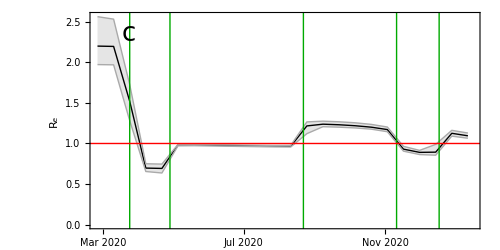

({2020,2,25} | {2020,3,10} | {2020,3,24} | {2020,4,7} | {2020,4,21} | {2020,5,5} | {2020,5,19} | {2020,6,2} | {2020,6,16} | {2020,6,30} | {2020,7,14} | {2020,7,28} | {2020,8,11} | {2020,8,25} | {2020,9,8} | {2020,9,22} | {2020,10,6} | {2020,10,20} | {2020,11,3} | {2020,11,17} | {2020,12,1} | {2020,12,15} | {2020,12,29} | {2021,1,12}
2.20073 | 2.19687 | 1.5199 | 0.696641 | 0.692465 | 0.982875 | 0.981533 | 0.978693 | 0.975806 | 0.972801 | 0.970105 | 0.96751 | 0.965782 | 1.21654 | 1.23804 | 1.23093 | 1.21885 | 1.20098 | 1.17155 | 0.930296 | 0.890611 | 0.893052 | 1.12566 | 1.09471
1.97275 | 1.96976 | 1.28203 | 0.654408 | 0.636045 | 0.971133 | 0.972777 | 0.969433 | 0.966291 | 0.963355 | 0.960627 | 0.958108 | 0.956768 | 1.121 | 1.20702 | 1.20108 | 1.19159 | 1.17643 | 1.14509 | 0.905372 | 0.863414 | 0.855573 | 1.09071 | 1.06463
2.56379 | 2.53328 | 1.72656 | 0.750238 | 0.745974 | 0.988759 | 0.987905 | 0.985571 | 0.983228 | 0.980977 | 0.978828 | 0.976419 | 0.977076 | 1.26606 | 1.27539 | 1.26768 | 1.25528 | 1.23557 | 1.20301 | 0.964894 | 0.915053 | 0.988707 | 1.1623 | 1.12889)

```mathematica
Fig4c=Show[DateListPlot[{Median[TrajectoriesRe],Quantile[TrajectoriesRe,0.025],Quantile[TrajectoriesRe,0.975]},{"February 25, 2020",Automatic,{0,0,Subscript[t, step]}},
FrameTicks->{{Automatic,None},{ticks,None}},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,
Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,17],PlotRange->{{"February 25, 2020","January 16, 2021"},{0,Automatic}},
AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{"R_e",None},{None,None}},Filling->{3->{2}},PlotStyle->{{Black,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},Prolog->{Join[{Directive[{Darker[Green]}]},Table[InfiniteLine[{TransitionDates⟦i⟧,0},{0,1}],{i,1,Length[TransitionDates]}]],{Directive[{Thick,Red}],InfiniteLine[{{0,1},{2,1}}]}(*,Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]*)},ImagePadding->{{52.5, Automatic}, {Automatic, Automatic}}(*,PlotLabel->Style[Row[{"Model fit"}],Black,17]*)],Graphics[Text[StyleForm["c",FontSize->26],Scaled[{0.1,0.9}]]]]

{DateRange[{2020,02,25},{2021,1,16},{14,"Day"}],Median[TrajectoriesRe],Quantile[TrajectoriesRe,0.025],Quantile[TrajectoriesRe,0.975]}//MatrixForm
```

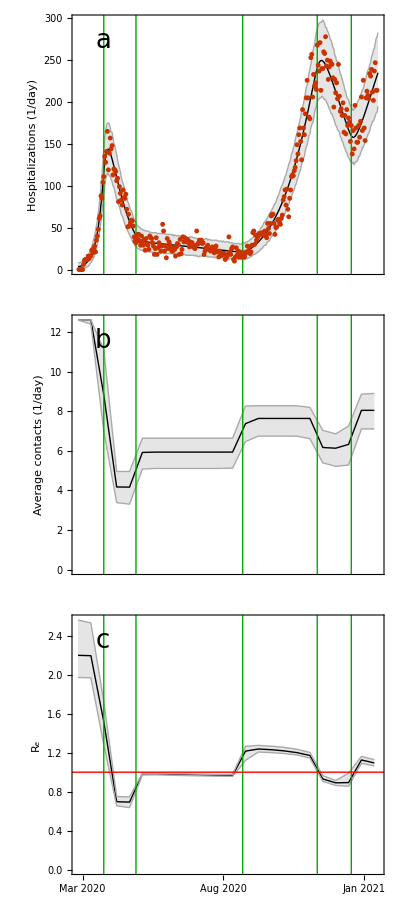

Figures//Fig3.pdf

Figures//Fig3.eps

```mathematica
Figfit=Grid[{{Fig4a},{Fig4b},{Fig4c}}]
(*Export[StringJoin["Figures//Fig3.pdf"],Figfit]
Export[StringJoin["Figures//Fig3.eps"],Figfit]*)
```